```mathematica
Clear[FinalLambda]
Clambda[n_, q_, λ_]:=(
Array[ab, {10, 10}];
C1[a_, b_]:=λ/(q^a λ^b-λ) + 1/(1-q^a λ^(b+1));
C2[a_, b_]:=-(q^a λ^b)/(q^a λ^b-λ);
FinalStep[a_,b_]:=(q^a λ^b)/(1-q^a λ^b);
ZMap[a_, b_]:=C1[a, b]*ab[a+1, b] +C2[a, b]*ab[1, 1];
init = ZMap[1, 0];
Replacing[x_]:=x/.{ab->ZMap};
Return[((1-q)/q)^n*(Nest[Replacing,init, n-2]/.{ab->FinalStep})])
Clear[p, q]
Clear[init]
Clear[C1, C2, C3,λ, n]
FinalLambda[n1_,q1_,λ1_]:=Clambda[n1, q, λ]/.{q->q1, λ->λ1}
```

```mathematica
(*Above we have the function reconstruct the analytical expression of E[Lambda_n]. Below we take the derivative (and include the k! factor) to find the distribution. Note that increasing n (set here to 4) increases the calculation runtime significantly. We also deal separately with the case where r =0. Finally, note that we use r instead of k here.*)
```

```mathematica
Limit[1/(r!)Simplify[D[FinalLambda[4,q1,λ1],{λ1,r}],Assumptions->{r>0, r∈Integers}],λ1->0]//Simplify;
```

```mathematica
(* The small cell below contains the found expressions up to n = 10*)
```

```mathematica
distr2 = If[r==0, (1-q)^2/(1-q^2), -(2 (-1+q) q^r)/(1+q)];
distr3 = If[r==0, (-1+q)^2/(1+q+q^2), -1/(2 (1+q+q^2)^2)(-1+q) (2 q^((3+r)/2)+(-√q)^r (-1+q^(3/2))^2-4 q^(2 r) (1+q) (1+q^2)+q^(r/2) (1+q^3)-2 q^r (1+q+q^2) (-1+q (-1+r)-r))];
distr4 = If[r==0, -(-1+q)^3/(1+q+q^2+q^3),((-1+q)^4 (4 q^(4+3 r) (1-q+q^2)^2 (1+q+q^2)^4+(1+√q)^4 q^((9+r)/2) (1-√q+q)^2 (1+q^2)^2 (1-√q+q-q^(3/2)+q^2)+(1+√q)^4 q^((11+r)/2) (1-√q+q)^2 (1+q^2)^2 (1-√q+q-q^(3/2)+q^2)+(-1+√q)^4 (-√q)^(-1+r) q^5 (1+√q+q)^2 (1+q^2)^2 (1+√q+q+q^(3/2)+q^2)+(-1+√q)^4 (-√q)^(-1+r) q^6 (1+√q+q)^2 (1+q^2)^2 (1+√q+q+q^(3/2)+q^2)-4 q^(4+r) (1+q) (1+q^2) (1+q+q^2)^2 (1+q+q^2+q^3+q^4)-q^(4+r) (1+q^2)^2 (1+q+q^2)^2 (1+q+q^2+q^3+q^4)+(-q)^(3+r) q (-1-q+q^3+q^4)^2 (1+q+q^2+q^3+q^4)+q^4 (1+q)^2 (1+q^2)^2 ((-√q)^r (-1+q^(3/2))^2 (2-√q+q+q^(3/2)+q^2-q^(5/2)+2 q^3)+q^(r/2) (1+q^(3/2))^2 (2+√q+q-q^(3/2)+q^2+q^(5/2)+2 q^3))-2 (-1+q) q^(4+r) (1+q) (1+q^2) (1+q+q^2)^2 (1+q+q^2+q^3+q^4) (1+r)))/(2 (1-q)^3 q^4 (1+q) (1+q^2)^2 (1+q+q^2)^2 (1+q+q^2+q^3+q^4))];
distr5 = If[r==0, (-1+q)^4/(1+q+q^2+q^3+q^4),1/(4 q^5)(1-q)^5 (((-q)^r q^5 (1+q))/((1+q^2)^2 (1-q+q^2))-(4 q^(6+2 r) (1+q) (1+q^2))/((-1+q)^4 (1+q+q^2)^3)+((-q)^(5+r) (1+q) (3-2 q+3 q^2))/((-1+q)^2 (1+q^2)^2 (1-q+q^2))-(q^(5+r) (3+12 q+12 q^2+7 q^3))/((-1+q)^4 (1+q+q^2)^2)-(4 q^(5+3 r) (1+q^2+q^4)^2 (1-q+q^2-q^3+q^4))/((-1+q)^4 (1+q) (1+q^2)^2 (1+q+q^2+q^3+q^4)^2)+(4 q^(5+3 r) (1+q^2+q^4)^2)/((-1+q)^4 (1+q) (1+q^2)^2 (1+q+q^2+q^3+q^4))+(2 (-√q)^(-1+r) q^6 (2-7 √q+16 q-27 q^(3/2)+38 q^2-44 q^(5/2)+46 q^3-44 q^(7/2)+38 q^4-27 q^(9/2)+16 q^5-7 q^(11/2)+2 q^6))/((1+√q)^4 (1-√q+q)^3 (1-√q+q-q^(3/2)+q^2)^2 (1-√q+q-q^(3/2)+q^2-q^(5/2)+q^3))+(2 q^((11+r)/2) (2+7 √q+16 q+27 q^(3/2)+38 q^2+44 q^(5/2)+46 q^3+44 q^(7/2)+38 q^4+27 q^(9/2)+16 q^5+7 q^(11/2)+2 q^6))/((-1+√q)^4 (1+√q+q)^3 (1+√q+q+q^(3/2)+q^2)^2 (1+√q+q+q^(3/2)+q^2+q^(5/2)+q^3))+(4 q^(6+2 r) (1+q) (3+7 q+16 q^2+16 q^3+18 q^4+11 q^5+5 q^6+2 q^7))/((-1+q)^4 (1+q+q^2)^3 (1+q+q^2+q^3+q^4))-(8 q^(5+4 r) (1+q) (1+q^2+q^4+q^6)^3)/((-1+q)^4 (1+q+q^2)^2 (1+q+q^2+q^3+q^4)^2 (1+q^2+q^3+q^4+q^5+q^6+q^8))-(q^(5+r) (-1+30 q+74 q^2+133 q^3+136 q^4+121 q^5+66 q^6+30 q^7+3 q^8))/((-1+q)^4 (1+q) (1+q+q^2)^2 (1+q+q^2+q^3+q^4))-(2 q^5 (-(-q^(3/2))^r (-1-q-q^2+q^(5/2)+q^(7/2)+q^(9/2))^2-q^(3 r/2) (1+q+q^2+q^(5/2)+q^(7/2)+q^(9/2))^2))/((-1+q)^4 (1+q)^2 (1+q+q^2+q^3+q^4)^2)-(2 q^5 ((-√q)^r (-1+2 √q-8 q+10 q^(3/2)-24 q^2+29 q^(5/2)-47 q^3+58 q^(7/2)-73 q^4+91 q^(9/2)-101 q^5+120 q^(11/2)-125 q^6+142 q^(13/2)-140 q^7+150 q^(15/2)-142 q^8+144 q^(17/2)-129 q^9+124 q^(19/2)-107 q^10+95 q^(21/2)-81 q^11+62 q^(23/2)-53 q^12+33 q^(25/2)-28 q^13+12 q^(27/2)-12 q^14+2 q^(29/2)-3 q^15)-q^(r/2) (1+2 √q+8 q+10 q^(3/2)+24 q^2+29 q^(5/2)+47 q^3+58 q^(7/2)+73 q^4+91 q^(9/2)+101 q^5+120 q^(11/2)+125 q^6+142 q^(13/2)+140 q^7+150 q^(15/2)+142 q^8+144 q^(17/2)+129 q^9+124 q^(19/2)+107 q^10+95 q^(21/2)+81 q^11+62 q^(23/2)+53 q^12+33 q^(25/2)+28 q^13+12 q^(27/2)+12 q^14+2 q^(29/2)+3 q^15)))/((-1+q)^4 (1+q)^2 (1+q+q^2)^2 (1+2 q+3 q^2+4 q^3+5 q^4+5 q^5+5 q^6+4 q^7+3 q^8+2 q^9+q^10))+(2 q^(5+r) (1+r))/((-1+q)^3 (1+q+q^2))-(4 q^(5+2 r) (1+q)^2 (1+q^2)^2 (1+r))/((-1+q)^3 (1+q+q^2)^2 (1+q+q^2+q^3+q^4))+(2 q^(5+r) (1-q-q^2-q^3+q^4) (1+r))/((-1+q)^3 (1+q+q^2) (1+q+q^2+q^3+q^4))-(q^5 ((-√q)^r (2+r-2 q^(3/2) (1+r)+q^3 (2+r))+q^(r/2) (2+r+2 q^(3/2) (1+r)+q^3 (2+r))))/((-1+q)^3 (1+q) (1+q+q^2)^2))];
distr6 = If[r==0, -(-1+q)^5/(1+q+q^2+q^3+q^4+q^5),1/(8 q^6)(-1+q) ((4 (-1+√q)^4 q^6 (-q^(3/2))^r (1+q+q^2)^3)/((1+q)^2 (1-√q+q-q^(3/2)+q^2)^2 (1-√q+q-q^(3/2)+q^2-q^(5/2)+q^3))+(4 (1+√q)^4 q^(6+(3 r)/2) (1+q+q^2)^3)/((1+q)^2 (1+√q+q+q^(3/2)+q^2)^2 (1+√q+q+q^(3/2)+q^2+q^(5/2)+q^3))+((-1+q)^4 (-q)^(5+r) q (1+q) (3-4 q+3 q^2))/((1-q+q^2)^2 (1+q^4))+(2 (-1+q)^2 (-q)^r q^7 (3-q-q^2+3 q^3))/((1+q^2) (1-q+q^2) (1+q^4))+(4 (-1+q)^2 q^6 (-q^2)^r (1+q^2)^3)/((1+q) (1+q^2+q^4)^2)-(16 q^(7+3 r) (1+q^2+q^4)^2)/((1+q) (1+q^2) (1+q+q^2+q^3+q^4)^2)-(8 q^(6+4 r) (1+q) (1+q^2+q^4+q^6)^3 (1-q-q^3-q^5+q^6))/((1+q+q^2)^4 (1+q^2+q^3+q^4+q^6)^2 (1+q+q^2+q^3+q^4+q^5+q^6))+(4 q^(6+2 r) (1+q+5 q^2+5 q^3+5 q^4+5 q^5+q^6+q^7))/((1+q+q^2)^4)-(8 q^(6+2 r) (1+q) (-2-3 q^2+7 q^3+9 q^5+q^6+2 q^7))/((1-q+q^2) (1+q+q^2)^4)-(16 q^(6+5 r) (1+q^2+q^4+q^6+q^8)^4)/((1+q) (1+q^2)^2 (1-q+q^2)^2 (1+q+q^2)^4 (1+q^4) (1+q^3+q^6) (1+q+q^2+q^3+q^4+q^5+q^6))+(8 q^(6+4 r) (1+q) (1+q^2)^3 (1+q^4)^3)/((1+q+q^2)^2 (1+q+q^2+q^3+q^4)^2 (1+q^2+q^3+q^4+q^5+q^6+q^8))+(2 q^(6+r) (-4-q-3 q^2+11 q^3+16 q^4+23 q^5+17 q^6+11 q^7+4 q^8))/((1+q) (1+q^2)^2 (1+q+q^2)^2)+(q^(6+r) (-11-21 q-14 q^2+77 q^3+196 q^4+451 q^5+573 q^6+758 q^7+669 q^8+643 q^9+404 q^10+285 q^11+114 q^12+51 q^13+5 q^14))/((1+q^2)^2 (1+q+q^2)^4 (1+q^3))+(4 (-√q)^r q^(13/2) (1-6 √q+24 q-73 q^(3/2)+183 q^2-395 q^(5/2)+761 q^3-1335 q^(7/2)+2163 q^4-3274 q^(9/2)+4669 q^5-6315 q^(11/2)+8147 q^6-10061 q^(13/2)+11932 q^7-13622 q^(15/2)+14987 q^8-15907 q^(17/2)+16300 q^9-16127 q^(19/2)+15408 q^10-14210 q^(21/2)+12639 q^11-10833 q^(23/2)+8930 q^12-7061 q^(25/2)+5340 q^13-3845 q^(27/2)+2620 q^14-1678 q^(29/2)+999 q^15-546 q^(31/2)+269 q^16-116 q^(33/2)+42 q^17-12 q^(35/2)+2 q^18))/((1+q)^2 (1-√q+q)^4 (1+√q+q)^2 (1-√q+q-q^(3/2)+q^2)^2 (1+q-q^(3/2)+q^2-2 q^(5/2)+2 q^3-q^(7/2)+3 q^4-q^(9/2)+2 q^5-2 q^(11/2)+q^6-q^(13/2)+q^7+q^8))-(4 q^((13+r)/2) (1+6 √q+24 q+73 q^(3/2)+183 q^2+395 q^(5/2)+761 q^3+1335 q^(7/2)+2163 q^4+3274 q^(9/2)+4669 q^5+6315 q^(11/2)+8147 q^6+10061 q^(13/2)+11932 q^7+13622 q^(15/2)+14987 q^8+15907 q^(17/2)+16300 q^9+16127 q^(19/2)+15408 q^10+14210 q^(21/2)+12639 q^11+10833 q^(23/2)+8930 q^12+7061 q^(25/2)+5340 q^13+3845 q^(27/2)+2620 q^14+1678 q^(29/2)+999 q^15+546 q^(31/2)+269 q^16+116 q^(33/2)+42 q^17+12 q^(35/2)+2 q^18))/((1+√q+q)^4 (1+2 q+q^(3/2)+2 q^2+q^(5/2)+2 q^3+q^4)^2 (1+q+q^(3/2)+q^2+2 q^(5/2)+2 q^3+q^(7/2)+3 q^4+q^(9/2)+2 q^5+2 q^(11/2)+q^6+q^(13/2)+q^7+q^8))-(4 q^6 (1+q+q^2)^2 (q^(3 r/2) (1+q^(5/2))^2 (1-√q+q^2-q^(5/2)+q^3-q^(9/2)+q^5)+(-q^(3/2))^r (-1+q^(5/2))^2 (1+√q+q^2+q^(5/2)+q^3+q^(9/2)+q^5)))/((1+q) (1+q+q^2+q^3+q^4)^2 (1+q+q^2+q^3+q^4+q^5+q^6))-(4 q^6 (-(-√q)^r (2+√q+10 q+7 q^(3/2)+24 q^2+23 q^(5/2)+34 q^3+59 q^(7/2)+25 q^4+131 q^(9/2)-26 q^5+256 q^(11/2)-144 q^6+449 q^(13/2)-348 q^7+720 q^(15/2)-641 q^8+1064 q^(17/2)-1020 q^9+1459 q^(19/2)-1460 q^10+1874 q^(21/2)-1926 q^11+2269 q^(23/2)-2367 q^12+2601 q^(25/2)-2734 q^13+2831 q^(27/2)-2978 q^14+2929 q^(29/2)-3072 q^15+2882 q^(31/2)-3001 q^16+2696 q^(33/2)-2780 q^17+2393 q^(35/2)-2438 q^18+2010 q^(37/2)-2020 q^19+1592 q^(39/2)-1571 q^20+1181 q^(41/2)-1140 q^21+813 q^(43/2)-764 q^22+512 q^(45/2)-468 q^23+289 q^(47/2)-257 q^24+142 q^(49/2)-124 q^25+57 q^(51/2)-52 q^26+16 q^(53/2)-18 q^27+2 q^(55/2)-4 q^28)+q^(r/2) (-2+√q-10 q+7 q^(3/2)-24 q^2+23 q^(5/2)-34 q^3+59 q^(7/2)-25 q^4+131 q^(9/2)+26 q^5+256 q^(11/2)+144 q^6+449 q^(13/2)+348 q^7+720 q^(15/2)+641 q^8+1064 q^(17/2)+1020 q^9+1459 q^(19/2)+1460 q^10+1874 q^(21/2)+1926 q^11+2269 q^(23/2)+2367 q^12+2601 q^(25/2)+2734 q^13+2831 q^(27/2)+2978 q^14+2929 q^(29/2)+3072 q^15+2882 q^(31/2)+3001 q^16+2696 q^(33/2)+2780 q^17+2393 q^(35/2)+2438 q^18+2010 q^(37/2)+2020 q^19+1592 q^(39/2)+1571 q^20+1181 q^(41/2)+1140 q^21+813 q^(43/2)+764 q^22+512 q^(45/2)+468 q^23+289 q^(47/2)+257 q^24+142 q^(49/2)+124 q^25+57 q^(51/2)+52 q^26+16 q^(53/2)+18 q^27+2 q^(55/2)+4 q^28)))/((1+q) (1+q+q^2)^4 (1+q+q^2+q^3+q^4)^2 (1+q+q^2+2 q^3+2 q^4+2 q^5+3 q^6+2 q^7+2 q^8+2 q^9+q^10+q^11+q^12))+(8 (-1+q) q^(6+2 r) (1+q)^2 (1+q^2)^2 (1+r))/((1-q+q^2) (1+q+q^2)^3)-(4 (-1+q) q^(6+r) (2+q+2 q^2) (1+r))/((1+q^2) (1+q+q^2))-(2 (-1+q) q^(6+r) (1+14 q+11 q^2+24 q^3+18 q^4+24 q^5+17 q^6+14 q^7+7 q^8) (1+r))/((1+q^2) (1-q+q^2) (1+q+q^2)^3)+(2 (-1+q)^2 q^(6+r) (1+q) (1+r) (2+r))/((1+q+q^2)^2)+(2 (-√q)^(-1+r) q^7 (-1-r-2 q^2 (1+r)-2 q^3 (1+r)-2 q^4 (1+r)-q^6 (1+r)+√q (2+r)+2 q^(3/2) (2+r)+q^(5/2) (2+r)+q^(7/2) (2+r)+2 q^(9/2) (2+r)+q^(11/2) (2+r)))/((1+q) (1+q+q^2)^2 (1+q+q^2+q^3+q^4))+(2 (-√q)^r q^(15/2) (-1-r-2 q^2 (1+r)-2 q^3 (1+r)-2 q^4 (1+r)-q^6 (1+r)+√q (2+r)+2 q^(3/2) (2+r)+q^(5/2) (2+r)+q^(7/2) (2+r)+2 q^(9/2) (2+r)+q^(11/2) (2+r)))/((1+q) (1+q+q^2)^2 (1+q+q^2+q^3+q^4))-(2 q^((13+r)/2) (1+r+2 q^2 (1+r)+2 q^3 (1+r)+2 q^4 (1+r)+q^6 (1+r)+√q (2+r)+2 q^(3/2) (2+r)+q^(5/2) (2+r)+q^(7/2) (2+r)+2 q^(9/2) (2+r)+q^(11/2) (2+r)))/((1+q) (1+q+q^2)^2 (1+q+q^2+q^3+q^4))+(2 q^((15+r)/2) (1+r+2 q^2 (1+r)+2 q^3 (1+r)+2 q^4 (1+r)+q^6 (1+r)+√q (2+r)+2 q^(3/2) (2+r)+q^(5/2) (2+r)+q^(7/2) (2+r)+2 q^(9/2) (2+r)+q^(11/2) (2+r)))/((1+q) (1+q+q^2)^2 (1+q+q^2+q^3+q^4))-1/((1+q+q^2)^3 (1+q+q^2+q^3+q^4))2 (-1+q) q^6 (q^(r/2) (-√q (1+r)-6 q^(3/2) (1+r)-11 q^(5/2) (1+r)-13 q^(7/2) (1+r)-13 q^(9/2) (1+r)-11 q^(11/2) (1+r)-6 q^(13/2) (1+r)-q^(15/2) (1+r)-3 (2+r)-5 q (2+r)-8 q^2 (2+r)-9 q^3 (2+r)-12 q^4 (2+r)-9 q^5 (2+r)-8 q^6 (2+r)-5 q^7 (2+r)-3 q^8 (2+r))+(-√q)^r (√q (1+r)+6 q^(3/2) (1+r)+11 q^(5/2) (1+r)+13 q^(7/2) (1+r)+13 q^(9/2) (1+r)+11 q^(11/2) (1+r)+6 q^(13/2) (1+r)+q^(15/2) (1+r)-3 (2+r)-5 q (2+r)-8 q^2 (2+r)-9 q^3 (2+r)-12 q^4 (2+r)-9 q^5 (2+r)-8 q^6 (2+r)-5 q^7 (2+r)-3 q^8 (2+r))))];
distr7 = If[r==0,(-1+q)^6/(1+q+q^2+q^3+q^4+q^5+q^6) , 1/q^7(1-q)^7 ((-(q^5 (-q^2)^(1+r) (1+q^2)^4)/(2 (-1+q)^2 (1+q) (1-q+q^2)^2 (1+q+q^2)^2 (1+q^4))+((-q)^r (1+q) (2 q^9-q^10+2 q^12-q^14+2 q^15))/(4 (-1+q)^2 (1+q^2)^3 (1-q+q^2) (1+q^4) (1-q+q^2-q^3+q^4))+((q^2)^r (1+q) (1+q^2) (q^7-9 q^8-9 q^9-27 q^10+2 q^11-14 q^12+14 q^13-7 q^14+3 q^15-q^16+q^17))/(2 (-1+q)^6 (1+q+q^2)^4 (1+q+q^2+q^3+q^4+q^5+q^6))+((q^4)^r (1+q) (1+q^2)^3 (q^8-q^9-q^11+3 q^12-4 q^13+q^14-3 q^15+3 q^16-6 q^17+3 q^18-3 q^19+q^20-4 q^21+3 q^22-q^23-q^25+q^26))/((-1+q)^6 (1-q+q^2) (1+q+q^2)^3 (1+q+q^2+q^3+q^4)^2 (1+q+q^2+q^3+q^4+q^5+q^6)^2)+((q^3)^r (1+q+q^2)^2 (2 q^8+4 q^9+5 q^10+26 q^11+10 q^12+58 q^13+35 q^14+79 q^15+61 q^16+91 q^17+61 q^18+89 q^19+33 q^20+74 q^21+6 q^22+40 q^23+q^24+12 q^25+2 q^27))/((-1+q)^6 (1+q) (1+q^2)^3 (1+q+q^2+q^3+q^4)^3 (1+q+q^2+q^3+q^4+q^5+q^6))-(q^r (4 q^7-34 q^9-195 q^10-592 q^11-1437 q^12-2810 q^13-4836 q^14-7309 q^15-10073 q^16-12610 q^17-14675 q^18-15767 q^19-15880 q^20-14831 q^21-12979 q^22-10466 q^23-7837 q^24-5313 q^25-3284 q^26-1774 q^27-849 q^28-328 q^29-107 q^30-22 q^31-4 q^32))/(4 (-1+q)^6 (1+q) (1+q^2)^3 (1+q+q^2)^3 (1+q+q^2+q^3+q^4)^2 (1+q+q^2+q^3+q^4+q^5+q^6))-((q^6)^r (1+q) (1+q^2)^3 (1+q+q^2)^3 (q^7-5 q^8+10 q^9-5 q^10-15 q^11+24 q^12+15 q^13-75 q^14+60 q^15+55 q^16-125 q^17+10 q^18+175 q^19-165 q^20-60 q^21+201 q^22-60 q^23-165 q^24+175 q^25+10 q^26-125 q^27+55 q^28+60 q^29-75 q^30+15 q^31+24 q^32-15 q^33-5 q^34+10 q^35-5 q^36+q^37))/((-1+q)^6 (1+q^4) (1-q+q^2-q^3+q^4) (1+q+q^2+q^3+q^4)^2 (1+q^3+q^6) (1+q+q^2+q^3+q^4+q^5+q^6)^2 (1+q+q^2+q^3+q^4+q^5+q^6+q^7+q^8+q^9+q^10))-(q^(-1-r) (-q^8-q^9-6 q^10-10 q^11-27 q^12-48 q^13-98 q^14-161 q^15-279 q^16-418 q^17-640 q^18-882 q^19-1216 q^20-1545 q^21-1945 q^22-2283 q^23-2645 q^24-2875 q^25-3079 q^26-3103 q^27-3079 q^28-2875 q^29-2645 q^30-2283 q^31-1945 q^32-1545 q^33-1216 q^34-882 q^35-640 q^36-418 q^37-279 q^38-161 q^39-98 q^40-48 q^41-27 q^42-10 q^43-6 q^44-q^45-q^46))/((-1+q)^6 (1+q) (1+q^2)^3 (1-q+q^2)^2 (1+q+q^2)^4 (1+q+q^2+q^3+q^4)^2 (1+q+q^2+q^3+q^4+q^5+q^6)^2)-((q^5)^r (q^7-q^8+4 q^9-6 q^10+10 q^11-20 q^12+20 q^13-49 q^14+36 q^15-99 q^16+56 q^17-172 q^18+78 q^19-262 q^20+100 q^21-355 q^22+120 q^23-433 q^24+132 q^25-478 q^26+136 q^27-478 q^28+132 q^29-433 q^30+120 q^31-355 q^32+100 q^33-262 q^34+78 q^35-172 q^36+56 q^37-99 q^38+36 q^39-49 q^40+20 q^41-20 q^42+10 q^43-6 q^44+4 q^45-q^46+q^47))/((-1+q)^6 (1+q) (1+q^2)^3 (1-q+q^2)^2 (1+q+q^2)^4 (1+q^4) (1+q^3+q^6) (1+q+q^2+q^3+q^4+q^5+q^6)^2)+(q^7 (1+q+q^2)^3 (1/q^(3/2)(-1+√q)^4 (-q^(3/2))^(1+r) (1+2 √q+3 q+4 q^(3/2)+5 q^2+5 q^(5/2)+5 q^3+4 q^(7/2)+3 q^4+2 q^(9/2)+q^5)^2 (1-√q+2 q-2 q^(3/2)+2 q^2-2 q^(5/2)+4 q^3-2 q^(7/2)+q^4+q^5-2 q^(11/2)+4 q^6-2 q^(13/2)+2 q^7-2 q^(15/2)+2 q^8-q^(17/2)+q^9)-(1+√q)^4 (q^(3/2))^r (1-2 √q+3 q-4 q^(3/2)+5 q^2-5 q^(5/2)+5 q^3-4 q^(7/2)+3 q^4-2 q^(9/2)+q^5)^2 (1+√q+2 q+2 q^(3/2)+2 q^2+2 q^(5/2)+4 q^3+2 q^(7/2)+q^4+q^5+2 q^(11/2)+4 q^6+2 q^(13/2)+2 q^7+2 q^(15/2)+2 q^8+q^(17/2)+q^9)))/(2 (-1+q)^6 (1+q)^2 (1+q+q^2+q^3+q^4)^2 (1+q^3+q^6) (1+q+q^2+q^3+q^4+q^5+q^6)^2)+(q^(15/2) (((-1+√q) (-√q)^(1+r) (1+√q+q) (1+√q+q+q^(3/2)+q^2) (1+√q+q+q^(3/2)+q^2+q^(5/2)+q^3) (2-11 √q+43 q-132 q^(3/2)+336 q^2-772 q^(5/2)+1584 q^3-3051 q^(7/2)+5448 q^4-9292 q^(9/2)+15011 q^5-23394 q^(11/2)+34978 q^6-50784 q^(13/2)+71299 q^7-97645 q^(15/2)+129993 q^8-169338 q^(17/2)+215228 q^9-268281 q^(19/2)+327147 q^10-391906 q^(21/2)+460181 q^11-531516 q^(23/2)+602597 q^12-672651 q^(25/2)+737755 q^13-797228 q^(27/2)+847046 q^14-887100 q^(29/2)+913832 q^15-928131 q^(31/2)+927334 q^16-913559 q^(33/2)+885251 q^17-845687 q^(35/2)+794346 q^18-735323 q^(37/2)+668802 q^19-599168 q^(39/2)+526852 q^20-455940 q^(41/2)+386682 q^21-322399 q^(43/2)+262851 q^22-210355 q^(45/2)+164097 q^23-125385 q^(47/2)+92948 q^24-67277 q^(49/2)+46887 q^25-31747 q^(51/2)+20419 q^26-12641 q^(53/2)+7218 q^27-3874 q^(55/2)+1745 q^28-646 q^(57/2)+41 q^29+155 q^(59/2)-221 q^30+171 q^(61/2)-127 q^31+68 q^(63/2)-39 q^32+14 q^(65/2)-6 q^33+q^(67/2)))/(√q (1-√q+q-2 q^(3/2)+2 q^2-2 q^(5/2)+3 q^3-3 q^(7/2)+3 q^4-3 q^(9/2)+3 q^5-2 q^(11/2)+2 q^6-2 q^(13/2)+q^7-q^(15/2)+q^8))+((1+√q) q^(r/2) (1-√q+q) (1-√q+q-q^(3/2)+q^2) (1-√q+q-q^(3/2)+q^2-q^(5/2)+q^3) (-2-11 √q-43 q-132 q^(3/2)-336 q^2-772 q^(5/2)-1584 q^3-3051 q^(7/2)-5448 q^4-9292 q^(9/2)-15011 q^5-23394 q^(11/2)-34978 q^6-50784 q^(13/2)-71299 q^7-97645 q^(15/2)-129993 q^8-169338 q^(17/2)-215228 q^9-268281 q^(19/2)-327147 q^10-391906 q^(21/2)-460181 q^11-531516 q^(23/2)-602597 q^12-672651 q^(25/2)-737755 q^13-797228 q^(27/2)-847046 q^14-887100 q^(29/2)-913832 q^15-928131 q^(31/2)-927334 q^16-913559 q^(33/2)-885251 q^17-845687 q^(35/2)-794346 q^18-735323 q^(37/2)-668802 q^19-599168 q^(39/2)-526852 q^20-455940 q^(41/2)-386682 q^21-322399 q^(43/2)-262851 q^22-210355 q^(45/2)-164097 q^23-125385 q^(47/2)-92948 q^24-67277 q^(49/2)-46887 q^25-31747 q^(51/2)-20419 q^26-12641 q^(53/2)-7218 q^27-3874 q^(55/2)-1745 q^28-646 q^(57/2)-41 q^29+155 q^(59/2)+221 q^30+171 q^(61/2)+127 q^31+68 q^(63/2)+39 q^32+14 q^(65/2)+6 q^33+q^(67/2)))/(1+√q+q+2 q^(3/2)+2 q^2+2 q^(5/2)+3 q^3+3 q^(7/2)+3 q^4+3 q^(9/2)+3 q^5+2 q^(11/2)+2 q^6+2 q^(13/2)+q^7+q^(15/2)+q^8)))/(2 (-1+q)^6 (1+q+q^2)^4 (1+q+q^2+q^3+q^4)^3 (1+2 q+2 q^2+2 q^3+2 q^4+2 q^5+2 q^6+q^7)^2)-((q^2)^r (1+q)^2 (1+q^2)^2 (2 q^8+q^9+2 q^10) (1+r))/((-1+q)^5 (1+q+q^2)^3 (1+q+q^2+q^3+q^4+q^5+q^6))-((q^3)^r (1+q+q^2)^4 (q^7-4 q^8+10 q^9-16 q^10+19 q^11-16 q^12+10 q^13-4 q^14+q^15) (1+r))/((-1+q)^5 (1+q^2)^2 (1+q+q^2+q^3+q^4)^2 (1+q+q^2+q^3+q^4+q^5+q^6))+(q^r (-4 q^7-8 q^8-14 q^9-13 q^10-8 q^11+8 q^12+23 q^13+46 q^14+62 q^15+76 q^16+77 q^17+74 q^18+58 q^19+41 q^20+22 q^21+10 q^22+2 q^23) (1+r))/(2 (-1+q)^5 (1+q^2)^2 (1+q+q^2)^2 (1+q+q^2+q^3+q^4) (1+q+q^2+q^3+q^4+q^5+q^6))-(q^(7+r) (1+q) (1+r) (2+r))/(2 (-1+q)^4 (1+q^2) (1+q+q^2))+(1/4 (3 (-√q)^r q^(15/2)-8 (-√q)^r q^8+12 (-√q)^r q^(17/2)-40 (-√q)^r q^9+33 (-√q)^r q^(19/2)-106 (-√q)^r q^10+74 (-√q)^r q^(21/2)-212 (-√q)^r q^11+135 (-√q)^r q^(23/2)-354 (-√q)^r q^12+216 (-√q)^r q^(25/2)-520 (-√q)^r q^13+302 (-√q)^r q^(27/2)-684 (-√q)^r q^14+381 (-√q)^r q^(29/2)-818 (-√q)^r q^15+433 (-√q)^r q^(31/2)-890 (-√q)^r q^16+454 (-√q)^r q^(33/2)-890 (-√q)^r q^17+433 (-√q)^r q^(35/2)-818 (-√q)^r q^18+381 (-√q)^r q^(37/2)-684 (-√q)^r q^19+302 (-√q)^r q^(39/2)-520 (-√q)^r q^20+216 (-√q)^r q^(41/2)-354 (-√q)^r q^21+135 (-√q)^r q^(43/2)-212 (-√q)^r q^22+74 (-√q)^r q^(45/2)-106 (-√q)^r q^23+33 (-√q)^r q^(47/2)-40 (-√q)^r q^24+12 (-√q)^r q^(49/2)-8 (-√q)^r q^25+3 (-√q)^r q^(51/2)+3 (-√q)^r q^(15/2) r-4 (-√q)^r q^8 r+12 (-√q)^r q^(17/2) r-20 (-√q)^r q^9 r+33 (-√q)^r q^(19/2) r-53 (-√q)^r q^10 r+74 (-√q)^r q^(21/2) r-106 (-√q)^r q^11 r+135 (-√q)^r q^(23/2) r-177 (-√q)^r q^12 r+216 (-√q)^r q^(25/2) r-260 (-√q)^r q^13 r+302 (-√q)^r q^(27/2) r-342 (-√q)^r q^14 r+381 (-√q)^r q^(29/2) r-409 (-√q)^r q^15 r+433 (-√q)^r q^(31/2) r-445 (-√q)^r q^16 r+454 (-√q)^r q^(33/2) r-445 (-√q)^r q^17 r+433 (-√q)^r q^(35/2) r-409 (-√q)^r q^18 r+381 (-√q)^r q^(37/2) r-342 (-√q)^r q^19 r+302 (-√q)^r q^(39/2) r-260 (-√q)^r q^20 r+216 (-√q)^r q^(41/2) r-177 (-√q)^r q^21 r+135 (-√q)^r q^(43/2) r-106 (-√q)^r q^22 r+74 (-√q)^r q^(45/2) r-53 (-√q)^r q^23 r+33 (-√q)^r q^(47/2) r-20 (-√q)^r q^24 r+12 (-√q)^r q^(49/2) r-4 (-√q)^r q^25 r+3 (-√q)^r q^(51/2) r)+1/4 (-3 q^(15/2+r/2)-8 q^(8+r/2)-12 q^(17/2+r/2)-40 q^(9+r/2)-33 q^(19/2+r/2)-106 q^(10+r/2)-74 q^(21/2+r/2)-212 q^(11+r/2)-135 q^(23/2+r/2)-354 q^(12+r/2)-216 q^(25/2+r/2)-520 q^(13+r/2)-302 q^(27/2+r/2)-684 q^(14+r/2)-381 q^(29/2+r/2)-818 q^(15+r/2)-433 q^(31/2+r/2)-890 q^(16+r/2)-454 q^(33/2+r/2)-890 q^(17+r/2)-433 q^(35/2+r/2)-818 q^(18+r/2)-381 q^(37/2+r/2)-684 q^(19+r/2)-302 q^(39/2+r/2)-520 q^(20+r/2)-216 q^(41/2+r/2)-354 q^(21+r/2)-135 q^(43/2+r/2)-212 q^(22+r/2)-74 q^(45/2+r/2)-106 q^(23+r/2)-33 q^(47/2+r/2)-40 q^(24+r/2)-12 q^(49/2+r/2)-8 q^(25+r/2)-3 q^(51/2+r/2)-3 q^(15/2+r/2) r-4 q^(8+r/2) r-12 q^(17/2+r/2) r-20 q^(9+r/2) r-33 q^(19/2+r/2) r-53 q^(10+r/2) r-74 q^(21/2+r/2) r-106 q^(11+r/2) r-135 q^(23/2+r/2) r-177 q^(12+r/2) r-216 q^(25/2+r/2) r-260 q^(13+r/2) r-302 q^(27/2+r/2) r-342 q^(14+r/2) r-381 q^(29/2+r/2) r-409 q^(15+r/2) r-433 q^(31/2+r/2) r-445 q^(16+r/2) r-454 q^(33/2+r/2) r-445 q^(17+r/2) r-433 q^(35/2+r/2) r-409 q^(18+r/2) r-381 q^(37/2+r/2) r-342 q^(19+r/2) r-302 q^(39/2+r/2) r-260 q^(20+r/2) r-216 q^(41/2+r/2) r-177 q^(21+r/2) r-135 q^(43/2+r/2) r-106 q^(22+r/2) r-74 q^(45/2+r/2) r-53 q^(23+r/2) r-33 q^(47/2+r/2) r-20 q^(24+r/2) r-12 q^(49/2+r/2) r-4 q^(25+r/2) r-3 q^(51/2+r/2) r))/((-1+q)^5 (1+q) (1+q+q^2)^3 (1+q+q^2+q^3+q^4)^2 (1+q+q^2+q^3+q^4+q^5+q^6))) -q (((q^2)^r (1+q) (1+q^2) (q^6-2 q^7+4 q^8-2 q^9+q^10))/(2 (-1+q)^6 (1+q+q^2)^4)-((-q^2)^(1+r) (1+q^2)^3 (q^6+2 q^7-2 q^8+2 q^9+q^10))/(2 (-1+q)^4 q^2 (1+q) (1-q+q^2)^2 (1+q+q^2)^2 (1+q^4))-((-q)^r q^6 (1+q) (2+6 q+6 q^2+q^3+3 q^4+5 q^5+14 q^6+7 q^7+5 q^8-q^9+6 q^10+6 q^11+4 q^12))/(4 (-1+q)^4 (1+q^2)^2 (1+q+q^2)^2 (1+q^4) (1-q+q^2-q^3+q^4))-(q^(6+r) (6+52 q+158 q^2+387 q^3+712 q^4+1145 q^5+1533 q^6+1838 q^7+1896 q^8+1762 q^9+1407 q^10+1007 q^11+598 q^12+311 q^13+120 q^14+38 q^15+4 q^16))/(4 (-1+q)^6 (1+q) (1+q^2)^2 (1+q+q^2)^2 (1+q+q^2+q^3+q^4)^2)-((q^3)^r (q^9+2 q^11+3 q^13+2 q^15+q^17))/((-1+q)^6 (1+q) (1+q^2)^3 (1+q+q^2+q^3+q^4)^2)+((q^4)^r (1+q) (1+q^2)^3 (q^7+3 q^11+3 q^15+q^19))/((-1+q)^6 (1+q+q^2) (1+q+q^2+q^3+q^4)^2 (1+q+q^2+q^3+q^4+q^5+q^6)^2)-((q^5)^r (1+q+q^2+q^3+q^4)^4 (q^6-4 q^7+10 q^8-20 q^9+35 q^10-52 q^11+68 q^12-80 q^13+85 q^14-80 q^15+68 q^16-52 q^17+35 q^18-20 q^19+10 q^20-4 q^21+q^22))/((-1+q)^6 (1+q) (1+q^2)^2 (1-q+q^2)^2 (1+q+q^2)^4 (1+q^4) (1+q^3+q^6) (1+q+q^2+q^3+q^4+q^5+q^6))+(q^(6-r) (1+q+6 q^2+10 q^3+27 q^4+48 q^5+98 q^6+161 q^7+279 q^8+418 q^9+640 q^10+882 q^11+1216 q^12+1545 q^13+1945 q^14+2283 q^15+2645 q^16+2875 q^17+3079 q^18+3103 q^19+3079 q^20+2875 q^21+2645 q^22+2283 q^23+1945 q^24+1545 q^25+1216 q^26+882 q^27+640 q^28+418 q^29+279 q^30+161 q^31+98 q^32+48 q^33+27 q^34+10 q^35+6 q^36+q^37+q^38))/((-1+q)^6 (1+q) (1+q^2)^3 (1-q+q^2)^2 (1+q+q^2)^4 (1+q+q^2+q^3+q^4)^2 (1+q+q^2+q^3+q^4+q^5+q^6)^2)+((q^6)^r (1+q) (1+q^2)^3 (q^6-2 q^7+q^8+2 q^9+q^10-8 q^11+8 q^12+4 q^13-2 q^14-16 q^15+22 q^16+4 q^17-10 q^18-20 q^19+40 q^20-4 q^21-17 q^22-14 q^23+47 q^24-14 q^25-17 q^26-4 q^27+40 q^28-20 q^29-10 q^30+4 q^31+22 q^32-16 q^33-2 q^34+4 q^35+8 q^36-8 q^37+q^38+2 q^39+q^40-2 q^41+q^42))/((-1+q)^6 (1+q^4) (1-q+q^2-q^3+q^4) (1+q+q^2+q^3+q^4)^2 (1+q^3+q^6) (1+q+q^2+q^3+q^4+q^5+q^6)^2 (1+q+q^2+q^3+q^4+q^5+q^6+q^7+q^8+q^9+q^10))+(-1/2 q^(9/2) (-q^(3/2))^(1+r) (-1-q-q^2+q^(5/2)+q^(7/2)+q^(9/2))^2 (1-3 √q+3 q-10 q^(3/2)+8 q^2-15 q^(5/2)+9 q^3-17 q^(7/2)+6 q^4-20 q^(9/2)+9 q^5-25 q^(11/2)+14 q^6-30 q^(13/2)+14 q^7-30 q^(15/2)+14 q^8-25 q^(17/2)+9 q^9-20 q^(19/2)+6 q^10-17 q^(21/2)+9 q^11-15 q^(23/2)+8 q^12-10 q^(25/2)+3 q^13-3 q^(27/2)+q^14)+1/2 q^6 (q^(3/2))^r (1+q+q^2+q^(5/2)+q^(7/2)+q^(9/2))^2 (1+3 √q+3 q+10 q^(3/2)+8 q^2+15 q^(5/2)+9 q^3+17 q^(7/2)+6 q^4+20 q^(9/2)+9 q^5+25 q^(11/2)+14 q^6+30 q^(13/2)+14 q^7+30 q^(15/2)+14 q^8+25 q^(17/2)+9 q^9+20 q^(19/2)+6 q^10+17 q^(21/2)+9 q^11+15 q^(23/2)+8 q^12+10 q^(25/2)+3 q^13+3 q^(27/2)+q^14))/((-1+q)^6 (1+q)^4 (1+q+q^2+q^3+q^4)^2 (1+q+q^2+2 q^3+2 q^4+2 q^5+3 q^6+2 q^7+2 q^8+2 q^9+q^10+q^11+q^12))+(q^6 ((1/(√q (1-q^(3/2)+q^3) (1-√q+q-q^(3/2)+q^2-q^(5/2)+q^3-q^(7/2)+q^4-q^(9/2)+q^5)))(-1+√q) (-√q)^(1+r) (1+√q+q) (1+√q+q+q^(3/2)+q^2) (1+√q+q+q^(3/2)+q^2+q^(5/2)+q^3) (4-14 √q+73 q-199 q^(3/2)+600 q^2-1374 q^(5/2)+3196 q^3-6414 q^(7/2)+12719 q^4-23015 q^(9/2)+40791 q^5-67874 q^(11/2)+110382 q^6-171257 q^(13/2)+259792 q^7-379669 q^(15/2)+543185 q^8-753486 q^(17/2)+1024655 q^9-1357012 q^(19/2)+1764190 q^10-2240723 q^(21/2)+2797035 q^11-3419047 q^(23/2)+4111598 q^12-4850366 q^(25/2)+5633664 q^13-6427406 q^(27/2)+7224577 q^14-7984348 q^(29/2)+8697737 q^15-9322303 q^(31/2)+9851867 q^16-10248454 q^(33/2)+10513482 q^17-10618852 q^(35/2)+10576868 q^18-10372544 q^(37/2)+10029735 q^19-9546727 q^(39/2)+8956608 q^20-8268111 q^(41/2)+7518853 q^21-6723120 q^(43/2)+5917321 q^22-5115876 q^(45/2)+4348801 q^23-3626245 q^(47/2)+2968535 q^24-2379217 q^(49/2)+1868164 q^25-1432313 q^(51/2)+1072634 q^26-781288 q^(53/2)+553347 q^27-378858 q^(55/2)+250327 q^28-158181 q^(57/2)+95041 q^29-53339 q^(59/2)+27355 q^30-12078 q^(61/2)+3875 q^31+8 q^(63/2)-1445 q^32+1643 q^(65/2)-1338 q^33+916 q^(67/2)-546 q^34+293 q^(69/2)-133 q^35+56 q^(71/2)-16 q^36+5 q^(73/2))-(1/((1+q^(3/2)+q^3) (1+√q+q+q^(3/2)+q^2+q^(5/2)+q^3+q^(7/2)+q^4+q^(9/2)+q^5)))(1+√q) q^(r/2) (1-√q+q) (1-√q+q-q^(3/2)+q^2) (1-√q+q-q^(3/2)+q^2-q^(5/2)+q^3) (-4-14 √q-73 q-199 q^(3/2)-600 q^2-1374 q^(5/2)-3196 q^3-6414 q^(7/2)-12719 q^4-23015 q^(9/2)-40791 q^5-67874 q^(11/2)-110382 q^6-171257 q^(13/2)-259792 q^7-379669 q^(15/2)-543185 q^8-753486 q^(17/2)-1024655 q^9-1357012 q^(19/2)-1764190 q^10-2240723 q^(21/2)-2797035 q^11-3419047 q^(23/2)-4111598 q^12-4850366 q^(25/2)-5633664 q^13-6427406 q^(27/2)-7224577 q^14-7984348 q^(29/2)-8697737 q^15-9322303 q^(31/2)-9851867 q^16-10248454 q^(33/2)-10513482 q^17-10618852 q^(35/2)-10576868 q^18-10372544 q^(37/2)-10029735 q^19-9546727 q^(39/2)-8956608 q^20-8268111 q^(41/2)-7518853 q^21-6723120 q^(43/2)-5917321 q^22-5115876 q^(45/2)-4348801 q^23-3626245 q^(47/2)-2968535 q^24-2379217 q^(49/2)-1868164 q^25-1432313 q^(51/2)-1072634 q^26-781288 q^(53/2)-553347 q^27-378858 q^(55/2)-250327 q^28-158181 q^(57/2)-95041 q^29-53339 q^(59/2)-27355 q^30-12078 q^(61/2)-3875 q^31+8 q^(63/2)+1445 q^32+1643 q^(65/2)+1338 q^33+916 q^(67/2)+546 q^34+293 q^(69/2)+133 q^35+56 q^(71/2)+16 q^36+5 q^(73/2))))/(2 (-1+q)^6 (1+2 q+2 q^2+q^3)^4 (1+2 q+4 q^2+6 q^3+8 q^4+9 q^5+10 q^6+9 q^7+8 q^8+6 q^9+4 q^10+2 q^11+q^12)^2)-(q^6 (1+q+q^2+q^3+q^4)^4 ((-q^(5/2))^r+(q^(5/2))^r+2 q^(7/2) (-(-q^(5/2))^r+(q^(5/2))^r)+q^7 ((-q^(5/2))^r+(q^(5/2))^r)))/(2 (-1+q)^6 (1+q)^4 (1+q^2)^2 (1+q+q^2)^2 (1+q+q^2+q^3+q^4+q^5+q^6)^2)+((-q)^r q^6 (1+q)^2 (1+r))/(4 (-1+q)^3 (1+q^2)^2 (1+q+q^2))-(q^(6+r) (1+5 q+6 q^2+8 q^3+6 q^4+5 q^5+q^6) (1+r))/(4 (-1+q)^5 (1+q^2) (1+q+q^2) (1+q+q^2+q^3+q^4))+(q^6 ((-√q)^r (q^(19/2) (-1846-1846 r)+q^(21/2) (-1774-1774 r)+q^(23/2) (-1549-1549 r)+q^(15/2) (-1513-1513 r)+q^(11/2) (-805-805 r)+q^(29/2) (-510-510 r)+q^(31/2) (-253-253 r)+q^(7/2) (-229-229 r)+q^(33/2) (-97-97 r)+q^(35/2) (-25-25 r)-3 √q (1+r)-85 q^(5/2) (1+r)-3 q^(37/2) (1+r)+3 (2+r)+24 q (2+r)+85 q^2 (2+r)+209 q^3 (2+r)+408 q^4 (2+r)+677 q^5 (2+r)+987 q^6 (2+r)+1297 q^7 (2+r)+1552 q^8 (2+r)+1701 q^9 (2+r)+1713 q^10 (2+r)+1585 q^11 (2+r)+1345 q^12 (2+r)+1041 q^13 (2+r)+728 q^14 (2+r)+450 q^15 (2+r)+239 q^16 (2+r)+103 q^17 (2+r)+33 q^18 (2+r)+6 q^19 (2+r)-3 q^(3/2) (7+7 r)-21 q^(13/2) (56+56 r)-6 q^(9/2) (79+79 r)-5 q^(25/2) (244+244 r)-3 q^(27/2) (283+283 r)-2 q^(17/2) (877+877 r))+q^(r/2) (3 √q (1+r)+85 q^(5/2) (1+r)+3 q^(37/2) (1+r)+3 (2+r)+24 q (2+r)+85 q^2 (2+r)+209 q^3 (2+r)+408 q^4 (2+r)+677 q^5 (2+r)+987 q^6 (2+r)+1297 q^7 (2+r)+1552 q^8 (2+r)+1701 q^9 (2+r)+1713 q^10 (2+r)+1585 q^11 (2+r)+1345 q^12 (2+r)+1041 q^13 (2+r)+728 q^14 (2+r)+450 q^15 (2+r)+239 q^16 (2+r)+103 q^17 (2+r)+33 q^18 (2+r)+6 q^19 (2+r)+3 q^(3/2) (7+7 r)+q^(35/2) (25+25 r)+21 q^(13/2) (56+56 r)+6 q^(9/2) (79+79 r)+q^(33/2) (97+97 r)+q^(7/2) (229+229 r)+5 q^(25/2) (244+244 r)+q^(31/2) (253+253 r)+3 q^(27/2) (283+283 r)+q^(29/2) (510+510 r)+q^(11/2) (805+805 r)+2 q^(17/2) (877+877 r)+q^(15/2) (1513+1513 r)+q^(23/2) (1549+1549 r)+q^(21/2) (1774+1774 r)+q^(19/2) (1846+1846 r))))/(4 (-1+q)^5 (1+q)^3 (1+q^2) (1+q+q^2)^3 (1+q+q^2+q^3+q^4) (1+q+q^2+q^3+q^4+q^5+q^6))+(q^6 (-(-√q)^r (8+6 r+r^2-2 q^(3/2) (3+4 r+r^2)+q^3 (8+6 r+r^2))-q^(r/2) (8+6 r+r^2+2 q^(3/2) (3+4 r+r^2)+q^3 (8+6 r+r^2))))/(16 (-1+q)^4 (1+q)^2 (1+q+q^2)^2)) )];
distr8 = If[r==0, -(-1+q)^7/(1+q+q^2+q^3+q^4+q^5+q^6+q^7), 1/q^8(1-q)^8 ((((-q^2)^(1+r) (1+q^2)^4 (q^8+4 q^9-8 q^10+12 q^11-10 q^12+12 q^13-8 q^14+4 q^15+q^16))/(4 (-1+q)^3 q^2 (1+q) (1-q+q^2)^2 (1+q+q^2)^2 (1+q^4)^2 (1-q+q^2-q^3+q^4))-((q^4)^r (1+q) (1+q^2)^3 (1+q^4)^3 (2 q^9+3 q^11+4 q^13-q^14+4 q^15+3 q^17+2 q^19))/((-1+q)^7 (1-q+q^2)^2 (1+q+q^2)^4 (1+q+q^2+q^3+q^4)^2 (1+q+q^2+q^3+q^4+q^5+q^6)^2)-((q^2)^r (1+q) (1+q^2) (q^8+6 q^9+17 q^10+19 q^11+14 q^12+20 q^13+14 q^14-3 q^15+30 q^16+92 q^17+142 q^18+185 q^19+230 q^20+204 q^21+150 q^22+95 q^23+53 q^24+14 q^25+5 q^26))/(4 (-1+q)^7 (1+q+q^2)^5 (1+q^4) (1+q+q^2+q^3+q^4)^2)-((q^3)^r (1+q+q^2)^2 (-2 q^8+4 q^9-8 q^10+11 q^11-4 q^12+15 q^13+7 q^14+34 q^15+11 q^16+52 q^17+18 q^18+52 q^19+21 q^20+32 q^21+23 q^22+11 q^23+10 q^24+7 q^25+2 q^27))/((-1+q)^7 (1+q) (1+q^2)^4 (1+q^4) (1+q+q^2+q^3+q^4)^3)+((-q)^r (1+q) (3 q^8+9 q^9+8 q^10-6 q^11+58 q^12-53 q^13+151 q^14-154 q^15+287 q^16-253 q^17+402 q^18-344 q^19+471 q^20-354 q^21+475 q^22-352 q^23+418 q^24-265 q^25+307 q^26-170 q^27+171 q^28-65 q^29+74 q^30-14 q^31+16 q^32+5 q^33+7 q^34))/(16 (-1+q)^3 (1+q^2)^4 (1-q+q^2)^2 (1+q+q^2)^2 (1+q^4)^2 (1-q^2+q^4) (1-q+q^2-q^3+q^4))+((q^5)^r (1+q+q^2+q^3+q^4)^4 (q^9-4 q^10+9 q^11-14 q^12+14 q^13+2 q^14-48 q^15+136 q^16-273 q^17+456 q^18-671 q^19+894 q^20-1100 q^21+1264 q^22-1370 q^23+1406 q^24-1370 q^25+1264 q^26-1100 q^27+894 q^28-671 q^29+456 q^30-273 q^31+136 q^32-48 q^33+2 q^34+14 q^35-14 q^36+9 q^37-4 q^38+q^39))/((-1+q)^7 (1+q) (1+q^2)^4 (1-q+q^2)^2 (1+q+q^2)^5 (1+q^4)^2 (1+q^3+q^6)^2 (1+q+q^2+q^3+q^4+q^5+q^6))-(q^r (-35 q^8-261 q^9-660 q^10-2160 q^11-3678 q^12-8017 q^13-9775 q^14-15506 q^15-9879 q^16-7027 q^17+23169 q^18+52191 q^19+125771 q^20+192720 q^21+311303 q^22+404447 q^23+539257 q^24+620101 q^25+721562 q^26+746001 q^27+773869 q^28+722955 q^29+673675 q^30+567640 q^31+474855 q^32+358091 q^33+266885 q^34+177465 q^35+116005 q^36+66302 q^37+36909 q^38+17347 q^39+7746 q^40+2736 q^41+836 q^42+175 q^43+9 q^44))/(16 (-1+q)^7 (1+q) (1+q^2)^4 (1-q+q^2)^2 (1+q+q^2)^4 (1+q^4) (1+q+q^2+q^3+q^4)^3)-((q^6)^r (1+q) (1+q^2)^3 (1+q+q^2)^3 (q^8-6 q^9+14 q^10-11 q^11-15 q^12+33 q^13+15 q^14-105 q^15+97 q^16+60 q^17-159 q^18-9 q^19+256 q^20-201 q^21-105 q^22+186 q^23+84 q^24-251 q^25+54 q^26+120 q^27+54 q^28-251 q^29+84 q^30+186 q^31-105 q^32-201 q^33+256 q^34-9 q^35-159 q^36+60 q^37+97 q^38-105 q^39+15 q^40+33 q^41-15 q^42-11 q^43+14 q^44-6 q^45+q^46))/((-1+q)^7 (1+q^4)^2 (1-q+q^2-q^3+q^4) (1+q+q^2+q^3+q^4)^3 (1+q^3+q^6) (1+q+q^2+q^3+q^4+q^5+q^6)^2 (1+q+q^2+q^3+q^4+q^5+q^6+q^7+q^8+q^9+q^10))-(q^(-1-r) (q^9+q^10+7 q^11+11 q^12+36 q^13+62 q^14+147 q^15+248 q^16+488 q^17+779 q^18+1344 q^19+2018 q^20+3151 q^21+4441 q^22+6381 q^23+8459 q^24+11304 q^25+14129 q^26+17685 q^27+20883 q^28+24603 q^29+27493 q^30+30582 q^31+32372 q^32+34072 q^33+34175 q^34+34072 q^35+32372 q^36+30582 q^37+27493 q^38+24603 q^39+20883 q^40+17685 q^41+14129 q^42+11304 q^43+8459 q^44+6381 q^45+4441 q^46+3151 q^47+2018 q^48+1344 q^49+779 q^50+488 q^51+248 q^52+147 q^53+62 q^54+36 q^55+11 q^56+7 q^57+q^58+q^59))/((-1+q)^7 (1+q) (1+q^2)^4 (1-q+q^2)^2 (1+q+q^2)^5 (1+q^4)^2 (1+q+q^2+q^3+q^4)^2 (1+q+q^2+q^3+q^4+q^5+q^6)^2)-((q^7)^r (q^8+6 q^10+21 q^12+56 q^14+126 q^16+252 q^18+462 q^20+786 q^22+1251 q^24+1876 q^26+2667 q^28+3612 q^30+4676 q^32+5796 q^34+6891 q^36+7872 q^38+8652 q^40+9156 q^42+9331 q^44+9156 q^46+8652 q^48+7872 q^50+6891 q^52+5796 q^54+4676 q^56+3612 q^58+2667 q^60+1876 q^62+1251 q^64+786 q^66+462 q^68+252 q^70+126 q^72+56 q^74+21 q^76+6 q^78+q^80))/((-1+q)^7 (1+q) (1+q^2)^4 (1-q+q^2)^2 (1+q+q^2)^4 (1+q^4)^2 (1-q^2+q^4) (1-q+q^2-q^3+q^4) (1+q+q^2+q^3+q^4)^2 (1+q^3+q^6) (1+q+q^2+q^3+q^4+q^5+q^6+q^7+q^8+q^9+q^10) (1+q+q^2+q^3+q^4+q^5+q^6+q^7+q^8+q^9+q^10+q^11+q^12))+(q^8 (1+q+q^2+q^3+q^4)^5 ((1+√q)^4 (q^(5/2))^r (1-q^(3/2)+q^3) (1-2 √q+3 q-3 q^(3/2)+3 q^2-3 q^(5/2)+3 q^3-2 q^(7/2)+q^4)^2-1/q^(5/2)(-1+√q)^4 (-q^(5/2))^(1+r) (1+q^(3/2)+q^3) (1+2 √q+3 q+3 q^(3/2)+3 q^2+3 q^(5/2)+3 q^3+2 q^(7/2)+q^4)^2))/(2 (-1+q)^7 (1+q)^4 (1+q^2)^2 (1+q+q^2)^4 (1+q^3+q^6) (1+q+q^2+q^3+q^4+q^5+q^6)^2)+(q^8 (1+q+q^2)^3 (1/q^(3/2)(-1+√q)^4 (-q^(3/2))^(1+r) (1+√q+q+q^(3/2)+q^2)^2 (1-√q+2 q-6 q^(3/2)+q^2-12 q^(5/2)-5 q^3-19 q^(7/2)-14 q^4-32 q^(9/2)-20 q^5-50 q^(11/2)-27 q^6-63 q^(13/2)-38 q^7-70 q^(15/2)-45 q^8-77 q^(17/2)-46 q^9-84 q^(19/2)-45 q^10-86 q^(21/2)-45 q^11-84 q^(23/2)-46 q^12-77 q^(25/2)-45 q^13-70 q^(27/2)-38 q^14-63 q^(29/2)-27 q^15-50 q^(31/2)-20 q^16-32 q^(33/2)-14 q^17-19 q^(35/2)-5 q^18-12 q^(37/2)+q^19-6 q^(39/2)+2 q^20-q^(41/2)+q^21)-(1+√q)^4 (q^(3/2))^r (1-√q+q-q^(3/2)+q^2)^2 (1+√q+2 q+6 q^(3/2)+q^2+12 q^(5/2)-5 q^3+19 q^(7/2)-14 q^4+32 q^(9/2)-20 q^5+50 q^(11/2)-27 q^6+63 q^(13/2)-38 q^7+70 q^(15/2)-45 q^8+77 q^(17/2)-46 q^9+84 q^(19/2)-45 q^10+86 q^(21/2)-45 q^11+84 q^(23/2)-46 q^12+77 q^(25/2)-45 q^13+70 q^(27/2)-38 q^14+63 q^(29/2)-27 q^15+50 q^(31/2)-20 q^16+32 q^(33/2)-14 q^17+19 q^(35/2)-5 q^18+12 q^(37/2)+q^19+6 q^(39/2)+2 q^20+q^(41/2)+q^21)))/(2 (-1+q)^7 (1+q)^4 (1+4 q+10 q^2+21 q^3+39 q^4+64 q^5+97 q^6+138 q^7+185 q^8+236 q^9+289 q^10+339 q^11+383 q^12+418 q^13+440 q^14+447 q^15+440 q^16+418 q^17+383 q^18+339 q^19+289 q^20+236 q^21+185 q^22+138 q^23+97 q^24+64 q^25+39 q^26+21 q^27+10 q^28+4 q^29+q^30))+(q^(17/2) (-(((1+√q) q^(r/2) (1-√q+q) (1-√q+q-q^(3/2)+q^2) (1-q^(3/2)+q^3) (1-√q+q-q^(3/2)+q^2-q^(5/2)+q^3) (-4-28 √q-147 q-576 q^(3/2)-1913 q^2-5566 q^(5/2)-14590 q^3-35223 q^(7/2)-79090 q^4-167475 q^(9/2)-336011 q^5-644485 q^(11/2)-1185081 q^6-2101621 q^(13/2)-3601472 q^7-5988606 q^(15/2)-9676757 q^8-15240105 q^(17/2)-23420810 q^9-35199292 q^(19/2)-51783184 q^10-74696682 q^(21/2)-105731218 q^11-147051579 q^(23/2)-201082994 q^12-270632236 q^(25/2)-358683659 q^13-468537761 q^(27/2)-603491398 q^14-767005155 q^(29/2)-962250925 q^15-1192331676 q^(31/2)-1459691823 q^16-1766426151 q^(33/2)-2113561804 q^17-2501503806 q^(35/2)-2929208405 q^18-3394816567 q^(37/2)-3894743890 q^19-4424547747 q^(39/2)-4977956433 q^20-5548000042 q^(41/2)-6125991232 q^21-6702925464 q^(43/2)-7268410766 q^22-7812314018 q^(45/2)-8323620979 q^23-8792277819 q^(47/2)-9207950541 q^24-9561989906 q^(49/2)-9846055985 q^25-10054124402 q^(51/2)-10180948512 q^26-10224028056 q^(53/2)-10181898413 q^27-10055997338 q^(55/2)-9848795526 q^28-9565520109 q^(57/2)-9212167673 q^29-8797069781 q^(59/2)-8328853289 q^30-7817856977 q^(61/2)-7274119682 q^31-6708673668 q^(63/2)-6131644368 q^32-5553452989 q^(65/2)-4983102021 q^33-4429315484 q^(67/2)-3899063974 q^34-3398658815 q^(69/2)-2932542738 q^35-2504338278 q^(71/2)-2115901275 q^36-1768308573 q^(73/2)-1461147058 q^37-1193415717 q^(75/2)-963006538 q^38-767493935 q^(77/2)-603757756 q^39-468638578 q^(79/2)-358656638 q^40-270522973 q^(81/2)-200918082 q^41-146862814 q^(83/2)-105533459 q^42-74508794 q^(85/2)-51610317 q^43-35050343 q^(87/2)-23294514 q^44-15138986 q^(89/2)-9596445 q^45-5928435 q^(91/2)-3556443 q^46-2070084 q^(93/2)-1162817 q^47-630012 q^(95/2)-326387 q^48-161755 q^(97/2)-75517 q^49-33336 q^(99/2)-13486 q^50-5074 q^(101/2)-1643 q^51-485 q^(103/2)-99 q^52-19 q^(105/2)+q^53))/((1+√q+q+q^(3/2)+q^2+q^(5/2)+q^3+q^(7/2)+q^4+q^(9/2)+q^5) (1+√q+q+q^(3/2)+q^2+q^(5/2)+q^3+q^(7/2)+q^4+q^(9/2)+q^5+q^(11/2)+q^6)))+((-1+√q) (-√q)^(1+r) (1+√q+q) (1+√q+q+q^(3/2)+q^2) (1+q^(3/2)+q^3) (1+√q+q+q^(3/2)+q^2+q^(5/2)+q^3) (-4+28 √q-147 q+576 q^(3/2)-1913 q^2+5566 q^(5/2)-14590 q^3+35223 q^(7/2)-79090 q^4+167475 q^(9/2)-336011 q^5+644485 q^(11/2)-1185081 q^6+2101621 q^(13/2)-3601472 q^7+5988606 q^(15/2)-9676757 q^8+15240105 q^(17/2)-23420810 q^9+35199292 q^(19/2)-51783184 q^10+74696682 q^(21/2)-105731218 q^11+147051579 q^(23/2)-201082994 q^12+270632236 q^(25/2)-358683659 q^13+468537761 q^(27/2)-603491398 q^14+767005155 q^(29/2)-962250925 q^15+1192331676 q^(31/2)-1459691823 q^16+1766426151 q^(33/2)-2113561804 q^17+2501503806 q^(35/2)-2929208405 q^18+3394816567 q^(37/2)-3894743890 q^19+4424547747 q^(39/2)-4977956433 q^20+5548000042 q^(41/2)-6125991232 q^21+6702925464 q^(43/2)-7268410766 q^22+7812314018 q^(45/2)-8323620979 q^23+8792277819 q^(47/2)-9207950541 q^24+9561989906 q^(49/2)-9846055985 q^25+10054124402 q^(51/2)-10180948512 q^26+10224028056 q^(53/2)-10181898413 q^27+10055997338 q^(55/2)-9848795526 q^28+9565520109 q^(57/2)-9212167673 q^29+8797069781 q^(59/2)-8328853289 q^30+7817856977 q^(61/2)-7274119682 q^31+6708673668 q^(63/2)-6131644368 q^32+5553452989 q^(65/2)-4983102021 q^33+4429315484 q^(67/2)-3899063974 q^34+3398658815 q^(69/2)-2932542738 q^35+2504338278 q^(71/2)-2115901275 q^36+1768308573 q^(73/2)-1461147058 q^37+1193415717 q^(75/2)-963006538 q^38+767493935 q^(77/2)-603757756 q^39+468638578 q^(79/2)-358656638 q^40+270522973 q^(81/2)-200918082 q^41+146862814 q^(83/2)-105533459 q^42+74508794 q^(85/2)-51610317 q^43+35050343 q^(87/2)-23294514 q^44+15138986 q^(89/2)-9596445 q^45+5928435 q^(91/2)-3556443 q^46+2070084 q^(93/2)-1162817 q^47+630012 q^(95/2)-326387 q^48+161755 q^(97/2)-75517 q^49+33336 q^(99/2)-13486 q^50+5074 q^(101/2)-1643 q^51+485 q^(103/2)-99 q^52+19 q^(105/2)+q^53))/(√q (1-√q+q-q^(3/2)+q^2-q^(5/2)+q^3-q^(7/2)+q^4-q^(9/2)+q^5) (1-√q+q-q^(3/2)+q^2-q^(5/2)+q^3-q^(7/2)+q^4-q^(9/2)+q^5-q^(11/2)+q^6))))/(2 (-1+q)^7 (1+q)^4 (1+q+q^2)^5 (1+q+q^2+q^3+q^4)^3 (1+q+2 q^2+3 q^3+3 q^4+4 q^5+5 q^6+4 q^7+5 q^8+4 q^9+3 q^10+3 q^11+2 q^12+q^13+q^14)^2)-((-q)^r q^8 (1+q)^2 (1+r))/(8 (-1+q)^2 (1+q^2)^2 (1-q+q^2) (1+q+q^2))+((q^2)^r (1+q)^2 (1+q^2)^2 (q^8+6 q^10+4 q^11+6 q^12+4 q^13+6 q^14+q^16) (1+r))/(2 (-1+q)^6 (1+q+q^2)^4 (1+q^4) (1+q+q^2+q^3+q^4))+((q^3)^r (1+q+q^2)^4 (q^8-4 q^9+10 q^10-16 q^11+19 q^12-16 q^13+10 q^14-4 q^15+q^16) (1+r))/((-1+q)^6 (1+q^2)^3 (1+q^4) (1+q+q^2+q^3+q^4)^2)+(q^r (7 q^8+64 q^9+163 q^10+463 q^11+830 q^12+1600 q^13+2317 q^14+3554 q^15+4392 q^16+5706 q^17+6181 q^18+7009 q^19+6710 q^20+6727 q^21+5680 q^22+5028 q^23+3681 q^24+2846 q^25+1744 q^26+1144 q^27+548 q^28+289 q^29+91 q^30+34 q^31+4 q^32) (1+r))/(4 (-1+q)^6 (1+q^2)^3 (1-q+q^2) (1+q+q^2)^3 (1+q^4) (1+q+q^2+q^3+q^4)^2)+(q^r (1+q) (q^8+9 q^9+13 q^10+25 q^11+22 q^12+25 q^13+13 q^14+9 q^15+q^16) (1+r) (2+r))/(8 (-1+q)^5 (1+q^2)^2 (1+q+q^2)^2 (1+q+q^2+q^3+q^4))+(q^(17/2) ((-√q)^r (q^15 (-46556-46556 r)+q^16 (-45565-45565 r)+q^14 (-45301-45301 r)+q^17 (-42452-42452 r)+q^13 (-41958-41958 r)+q^18 (-37601-37601 r)+q^12 (-36937-36937 r)+q^19 (-31600-31600 r)+q^11 (-30842-30842 r)+q^20 (-25095-25095 r)+q^21 (-18733-18733 r)+q^9 (-18013-18013 r)+q^7 (-7928-7928 r)+q^24 (-4940-4940 r)+q^6 (-4602-4602 r)+q^25 (-2611-2611 r)+q^5 (-2397-2397 r)+q^26 (-1213-1213 r)+q^4 (-1093-1093 r)+q^27 (-478-478 r)+q (-28-28 r)+q^30 (-5-5 r)-3 (1+r)+5 √q (2+r)+46 q^(3/2) (2+r)+207 q^(5/2) (2+r)+645 q^(7/2) (2+r)+1592 q^(9/2) (2+r)+3319 q^(11/2) (2+r)+6062 q^(13/2) (2+r)+9963 q^(15/2) (2+r)+15005 q^(17/2) (2+r)+20961 q^(19/2) (2+r)+27415 q^(21/2) (2+r)+33800 q^(23/2) (2+r)+39448 q^(25/2) (2+r)+43718 q^(27/2) (2+r)+46105 q^(29/2) (2+r)+46303 q^(31/2) (2+r)+44288 q^(33/2) (2+r)+40321 q^(35/2) (2+r)+34874 q^(37/2) (2+r)+28573 q^(39/2) (2+r)+22089 q^(41/2) (2+r)+16010 q^(43/2) (2+r)+10785 q^(45/2) (2+r)+6677 q^(47/2) (2+r)+3736 q^(49/2) (2+r)+1844 q^(51/2) (2+r)+777 q^(53/2) (2+r)+264 q^(55/2) (2+r)+64 q^(57/2) (2+r)+8 q^(59/2) (2+r)-4 q^29 (9+9 r)-8 q^28 (19+19 r)-2 q^2 (64+64 r)-3 q^3 (140+140 r)-9 q^8 (1382+1382 r)-3 q^23 (2802+2802 r)-2 q^22 (6526+6526 r)-3 q^10 (8107+8107 r))+q^(r/2) (3 (1+r)+5 √q (2+r)+46 q^(3/2) (2+r)+207 q^(5/2) (2+r)+645 q^(7/2) (2+r)+1592 q^(9/2) (2+r)+3319 q^(11/2) (2+r)+6062 q^(13/2) (2+r)+9963 q^(15/2) (2+r)+15005 q^(17/2) (2+r)+20961 q^(19/2) (2+r)+27415 q^(21/2) (2+r)+33800 q^(23/2) (2+r)+39448 q^(25/2) (2+r)+43718 q^(27/2) (2+r)+46105 q^(29/2) (2+r)+46303 q^(31/2) (2+r)+44288 q^(33/2) (2+r)+40321 q^(35/2) (2+r)+34874 q^(37/2) (2+r)+28573 q^(39/2) (2+r)+22089 q^(41/2) (2+r)+16010 q^(43/2) (2+r)+10785 q^(45/2) (2+r)+6677 q^(47/2) (2+r)+3736 q^(49/2) (2+r)+1844 q^(51/2) (2+r)+777 q^(53/2) (2+r)+264 q^(55/2) (2+r)+64 q^(57/2) (2+r)+8 q^(59/2) (2+r)+q^30 (5+5 r)+4 q^29 (9+9 r)+8 q^28 (19+19 r)+q (28+28 r)+2 q^2 (64+64 r)+3 q^3 (140+140 r)+q^27 (478+478 r)+q^4 (1093+1093 r)+q^26 (1213+1213 r)+9 q^8 (1382+1382 r)+q^5 (2397+2397 r)+q^25 (2611+2611 r)+3 q^23 (2802+2802 r)+q^6 (4602+4602 r)+q^24 (4940+4940 r)+2 q^22 (6526+6526 r)+q^7 (7928+7928 r)+3 q^10 (8107+8107 r)+q^9 (18013+18013 r)+q^21 (18733+18733 r)+q^20 (25095+25095 r)+q^11 (30842+30842 r)+q^19 (31600+31600 r)+q^12 (36937+36937 r)+q^18 (37601+37601 r)+q^13 (41958+41958 r)+q^17 (42452+42452 r)+q^14 (45301+45301 r)+q^16 (45565+45565 r)+q^15 (46556+46556 r))))/(4 (-1+q)^6 (1+q)^3 (1+q^2) (1+q+q^2)^4 (1+q+q^2+q^3+q^4)^2 (1+q^3+q^6) (1+q+q^2+q^3+q^4+q^5+q^6))+1/(16 (-1+q)^5 (1+q)^2 (1+q+q^2)^2 (1+q+q^2+q^3+q^4))q^(17/2) (-(-√q)^r (-3-4 r-r^2-2 q^2 (1+r) (3+r)-q^6 (1+r) (3+r)-q^3 (3+r) (2+2 r)-q^4 (3+r) (2+2 r)+√q (8+6 r+r^2)+q^(5/2) (8+6 r+r^2)+q^(7/2) (8+6 r+r^2)+q^(11/2) (8+6 r+r^2)+q^(3/2) (16+12 r+2 r^2)+q^(9/2) (16+12 r+2 r^2))-q^(r/2) (3+4 r+r^2+2 q^2 (1+r) (3+r)+q^6 (1+r) (3+r)+q^3 (3+r) (2+2 r)+q^4 (3+r) (2+2 r)+√q (8+6 r+r^2)+q^(5/2) (8+6 r+r^2)+q^(7/2) (8+6 r+r^2)+q^(11/2) (8+6 r+r^2)+q^(3/2) (16+12 r+2 r^2)+q^(9/2) (16+12 r+2 r^2)))) -q (((-q^3)^(1+r) (1+q) (1-q+q^2)^5 (q^7+3 q^8+6 q^9+7 q^10+6 q^11+3 q^12+q^13))/(2 (-1+q)^5 q^3 (1+q^2)^2 (1+q^4)^2 (1+q+q^2+q^3+q^4)^2)-((-q^2)^(1+r) (1+q^2)^3 (q^7-9 q^8+9 q^9-14 q^10+14 q^11-22 q^12+14 q^13-14 q^14+9 q^15-9 q^16+q^17))/(4 (-1+q)^5 q^2 (1+q) (1-q+q^2)^2 (1+q+q^2)^3 (1+q^4) (1-q+q^2-q^3+q^4))+((-q)^r q^7 (1+q) (-5+43 q-69 q^2+169 q^3-202 q^4+329 q^5-321 q^6+453 q^7-417 q^8+550 q^9-452 q^10+550 q^11-397 q^12+425 q^13-261 q^14+261 q^15-114 q^16+101 q^17-9 q^18+15 q^19+15 q^20))/(16 (-1+q)^5 (1+q^2)^4 (1-q+q^2)^2 (1+q+q^2)^2 (1-q^2+q^4) (1-q+q^2-q^3+q^4))+((q^2)^r (1+q) (1+q^2) (q^7+10 q^8+41 q^9+103 q^10+189 q^11+302 q^12+389 q^13+426 q^14+409 q^15+334 q^16+225 q^17+131 q^18+61 q^19+18 q^20+5 q^21))/(4 (-1+q)^7 (1+q+q^2)^5 (1+q+q^2+q^3+q^4)^2)+((q^5)^r (1+q+q^2+q^3+q^4)^4 (q^8-4 q^9+10 q^10-20 q^11+35 q^12-52 q^13+68 q^14-80 q^15+85 q^16-80 q^17+68 q^18-52 q^19+35 q^20-20 q^21+10 q^22-4 q^23+q^24))/((-1+q)^7 (1+q) (1+q^2) (1-q+q^2)^2 (1+q+q^2)^5 (1+q^3+q^6)^2 (1+q+q^2+q^3+q^4+q^5+q^6))+(q^(7+r) (-5+162 q+667 q^2+2312 q^3+5368 q^4+11498 q^5+20158 q^6+33010 q^7+47254 q^8+63736 q^9+77091 q^10+88258 q^11+91658 q^12+90162 q^13+80543 q^14+68112 q^15+51886 q^16+37242 q^17+23606 q^18+13978 q^19+6960 q^20+3184 q^21+1079 q^22+314 q^23+31 q^24))/(16 (-1+q)^7 (1+q) (1+q^2)^2 (1-q+q^2)^2 (1+q+q^2)^4 (1+q+q^2+q^3+q^4)^2)-((q^3)^r (q^7-q^8+5 q^9-q^10+9 q^11+2 q^12+10 q^13+10 q^14+5 q^15+17 q^16+3 q^17+17 q^18+5 q^19+10 q^20+10 q^21+2 q^22+9 q^23-q^24+5 q^25-q^26+q^27))/(2 (-1+q)^7 (1+q) (1+q^2)^4 (1+q+q^2+q^3+q^4)^3)-((q^4)^r (1+q) (1+q^2)^3 (q^10+2 q^12+q^13+5 q^14+7 q^16+3 q^17+9 q^18+9 q^20+3 q^21+7 q^22+5 q^24+q^25+2 q^26+q^28))/((-1+q)^7 (1-q+q^2)^2 (1+q+q^2)^4 (1+q+q^2+q^3+q^4)^2 (1+q+q^2+q^3+q^4+q^5+q^6)^2)-((q^6)^r (1+q) (1+q^2)^3 (1-q+q^2)^5 (q^7+3 q^8+q^9-8 q^10-9 q^11+13 q^12+31 q^13-50 q^15-30 q^16+54 q^17+72 q^18-21 q^19-87 q^20-21 q^21+72 q^22+54 q^23-30 q^24-50 q^25+31 q^27+13 q^28-9 q^29-8 q^30+q^31+3 q^32+q^33))/((-1+q)^7 (1+q^4) (1-q+q^2-q^3+q^4) (1+q+q^2+q^3+q^4)^2 (1+q^3+q^6) (1+q+q^2+q^3+q^4+q^5+q^6)^2 (1+q+q^2+q^3+q^4+q^5+q^6+q^7+q^8+q^9+q^10))-(q^(7-r) (1+q+7 q^2+11 q^3+36 q^4+62 q^5+147 q^6+248 q^7+488 q^8+779 q^9+1344 q^10+2018 q^11+3151 q^12+4441 q^13+6381 q^14+8459 q^15+11304 q^16+14129 q^17+17685 q^18+20883 q^19+24603 q^20+27493 q^21+30582 q^22+32372 q^23+34072 q^24+34175 q^25+34072 q^26+32372 q^27+30582 q^28+27493 q^29+24603 q^30+20883 q^31+17685 q^32+14129 q^33+11304 q^34+8459 q^35+6381 q^36+4441 q^37+3151 q^38+2018 q^39+1344 q^40+779 q^41+488 q^42+248 q^43+147 q^44+62 q^45+36 q^46+11 q^47+7 q^48+q^49+q^50))/((-1+q)^7 (1+q) (1+q^2)^4 (1-q+q^2)^2 (1+q+q^2)^5 (1+q^4)^2 (1+q+q^2+q^3+q^4)^2 (1+q+q^2+q^3+q^4+q^5+q^6)^2)-((q^7)^r (-q^7-6 q^9-21 q^11-56 q^13-126 q^15-252 q^17-462 q^19-786 q^21-1251 q^23-1876 q^25-2667 q^27-3612 q^29-4676 q^31-5796 q^33-6891 q^35-7872 q^37-8652 q^39-9156 q^41-9331 q^43-9156 q^45-8652 q^47-7872 q^49-6891 q^51-5796 q^53-4676 q^55-3612 q^57-2667 q^59-1876 q^61-1251 q^63-786 q^65-462 q^67-252 q^69-126 q^71-56 q^73-21 q^75-6 q^77-q^79))/((-1+q)^7 (1+q) (1+q^2)^4 (1-q+q^2)^2 (1+q+q^2)^4 (1+q^4)^2 (1-q^2+q^4) (1-q+q^2-q^3+q^4) (1+q+q^2+q^3+q^4)^2 (1+q^3+q^6) (1+q+q^2+q^3+q^4+q^5+q^6+q^7+q^8+q^9+q^10) (1+q+q^2+q^3+q^4+q^5+q^6+q^7+q^8+q^9+q^10+q^11+q^12))+((1+q+q^2+q^3+q^4)^4 (-1/2 q^(9/2) (-q^(5/2))^(1+r) (-1-√q-q+q^(7/2)+q^4+q^(9/2))^2 (1-2 √q+3 q-q^(3/2)-q^2+q^(5/2)+2 q^3-3 q^(7/2)+2 q^4+q^(9/2)-q^5-q^(11/2)+3 q^6-2 q^(13/2)+q^7)+1/2 q^7 (q^(5/2))^r (1-√q+q+q^(7/2)-q^4+q^(9/2))^2 (1+2 √q+3 q+q^(3/2)-q^2-q^(5/2)+2 q^3+3 q^(7/2)+2 q^4-q^(9/2)-q^5+q^(11/2)+3 q^6+2 q^(13/2)+q^7)))/((-1+q)^7 (1+q)^3 (1+q^2)^2 (1+q+q^2)^4 (1+q^3+q^6) (1+q+q^2+q^3+q^4+q^5+q^6)^2)+(q^7 (1/q^(3/2)(-q^(3/2))^(1+r) (-1-q-q^2+q^(5/2)+q^(7/2)+q^(9/2))^2 (1-3 √q+5 q-13 q^(3/2)+16 q^2-25 q^(5/2)+26 q^3-39 q^(7/2)+34 q^4-53 q^(9/2)+47 q^5-71 q^(11/2)+61 q^6-93 q^(13/2)+77 q^7-115 q^(15/2)+94 q^8-132 q^(17/2)+103 q^9-145 q^(19/2)+110 q^10-153 q^(21/2)+116 q^11-158 q^(23/2)+116 q^12-153 q^(25/2)+110 q^13-145 q^(27/2)+103 q^14-132 q^(29/2)+94 q^15-115 q^(31/2)+77 q^16-93 q^(33/2)+61 q^17-71 q^(35/2)+47 q^18-53 q^(37/2)+34 q^19-39 q^(39/2)+26 q^20-25 q^(41/2)+16 q^21-13 q^(43/2)+5 q^22-3 q^(45/2)+q^23)-(q^(3/2))^r (1+q+q^2+q^(5/2)+q^(7/2)+q^(9/2))^2 (1+3 √q+5 q+13 q^(3/2)+16 q^2+25 q^(5/2)+26 q^3+39 q^(7/2)+34 q^4+53 q^(9/2)+47 q^5+71 q^(11/2)+61 q^6+93 q^(13/2)+77 q^7+115 q^(15/2)+94 q^8+132 q^(17/2)+103 q^9+145 q^(19/2)+110 q^10+153 q^(21/2)+116 q^11+158 q^(23/2)+116 q^12+153 q^(25/2)+110 q^13+145 q^(27/2)+103 q^14+132 q^(29/2)+94 q^15+115 q^(31/2)+77 q^16+93 q^(33/2)+61 q^17+71 q^(35/2)+47 q^18+53 q^(37/2)+34 q^19+39 q^(39/2)+26 q^20+25 q^(41/2)+16 q^21+13 q^(43/2)+5 q^22+3 q^(45/2)+q^23)))/(2 (-1+q)^7 (1+q)^3 (1+4 q+10 q^2+21 q^3+39 q^4+64 q^5+97 q^6+138 q^7+185 q^8+236 q^9+289 q^10+339 q^11+383 q^12+418 q^13+440 q^14+447 q^15+440 q^16+418 q^17+383 q^18+339 q^19+289 q^20+236 q^21+185 q^22+138 q^23+97 q^24+64 q^25+39 q^26+21 q^27+10 q^28+4 q^29+q^30))+(q^7 (-(((-1+√q) (-√q)^(1+r) (1+√q+q) (1+√q+q+q^(3/2)+q^2) (1+q^(3/2)+q^3) (1+√q+q+q^(3/2)+q^2+q^(5/2)+q^3) (2-12 √q+74 q-277 q^(3/2)+974 q^2-2788 q^(5/2)+7500 q^3-18004 q^(7/2)+40987 q^4-86646 q^(9/2)+175276 q^5-336171 q^(11/2)+621463 q^6-1102768 q^(13/2)+1896790 q^7-3156630 q^(15/2)+5114450 q^8-8061675 q^(17/2)+12414177 q^9-18671881 q^(19/2)+27511433 q^10-39711463 q^(21/2)+56277041 q^11-78312857 q^(23/2)+107183640 q^12-144315185 q^(25/2)+191396036 q^13-250086730 q^(27/2)+322271065 q^14-409657722 q^(29/2)+514094252 q^15-637052245 q^(31/2)+780022628 q^16-943884642 q^(33/2)+1129405723 q^17-1336503494 q^(35/2)+1564875257 q^18-1813169301 q^(37/2)+2079765914 q^19-2361877629 q^(39/2)+2656495157 q^20-2959434910 q^(41/2)+3266449803 q^21-3572237294 q^(43/2)+3871698195 q^22-4158911328 q^(45/2)+4428506737 q^23-4674605827 q^(47/2)+4892261702 q^24-5076359520 q^(49/2)+5223068582 q^25-5328697909 q^(51/2)+5391104384 q^26-5408503645 q^(53/2)+5380785900 q^27-5308291638 q^(55/2)+5192999952 q^28-5037290172 q^(57/2)+4844984581 q^29-4620127631 q^(59/2)+4367882182 q^30-4093365562 q^(61/2)+3802412455 q^31-3500508998 q^(63/2)+3193444461 q^32-2886379840 q^(65/2)+2584413124 q^33-2291808251 q^(67/2)+2012495392 q^34-1749471385 q^(69/2)+1505249353 q^35-1281425327 q^(71/2)+1079082911 q^36-898506478 q^(73/2)+739538974 q^37-601411974 q^(75/2)+483050473 q^38-382985726 q^(77/2)+299600546 q^39-231092432 q^(79/2)+175656038 q^40-131470216 q^(81/2)+96819727 q^41-70088230 q^(83/2)+49826951 q^42-34744341 q^(85/2)+23733539 q^43-15856366 q^(87/2)+10343196 q^44-6573188 q^(89/2)+4059366 q^45-2428563 q^(91/2)+1401743 q^46-776704 q^(93/2)+410063 q^47-204307 q^(95/2)+94419 q^48-39396 q^(97/2)+13902 q^49-3405 q^(99/2)-184 q^50+943 q^(101/2)-774 q^51+458 q^(103/2)-213 q^52+85 q^(105/2)-24 q^53+6 q^(107/2)))/(√q (1-√q+q-q^(3/2)+q^2-q^(5/2)+q^3-q^(7/2)+q^4-q^(9/2)+q^5) (1-√q+q-q^(3/2)+q^2-q^(5/2)+q^3-q^(7/2)+q^4-q^(9/2)+q^5-q^(11/2)+q^6)))+((1+√q) q^(r/2) (1-√q+q) (1-√q+q-q^(3/2)+q^2) (1-q^(3/2)+q^3) (1-√q+q-q^(3/2)+q^2-q^(5/2)+q^3) (-2-12 √q-74 q-277 q^(3/2)-974 q^2-2788 q^(5/2)-7500 q^3-18004 q^(7/2)-40987 q^4-86646 q^(9/2)-175276 q^5-336171 q^(11/2)-621463 q^6-1102768 q^(13/2)-1896790 q^7-3156630 q^(15/2)-5114450 q^8-8061675 q^(17/2)-12414177 q^9-18671881 q^(19/2)-27511433 q^10-39711463 q^(21/2)-56277041 q^11-78312857 q^(23/2)-107183640 q^12-144315185 q^(25/2)-191396036 q^13-250086730 q^(27/2)-322271065 q^14-409657722 q^(29/2)-514094252 q^15-637052245 q^(31/2)-780022628 q^16-943884642 q^(33/2)-1129405723 q^17-1336503494 q^(35/2)-1564875257 q^18-1813169301 q^(37/2)-2079765914 q^19-2361877629 q^(39/2)-2656495157 q^20-2959434910 q^(41/2)-3266449803 q^21-3572237294 q^(43/2)-3871698195 q^22-4158911328 q^(45/2)-4428506737 q^23-4674605827 q^(47/2)-4892261702 q^24-5076359520 q^(49/2)-5223068582 q^25-5328697909 q^(51/2)-5391104384 q^26-5408503645 q^(53/2)-5380785900 q^27-5308291638 q^(55/2)-5192999952 q^28-5037290172 q^(57/2)-4844984581 q^29-4620127631 q^(59/2)-4367882182 q^30-4093365562 q^(61/2)-3802412455 q^31-3500508998 q^(63/2)-3193444461 q^32-2886379840 q^(65/2)-2584413124 q^33-2291808251 q^(67/2)-2012495392 q^34-1749471385 q^(69/2)-1505249353 q^35-1281425327 q^(71/2)-1079082911 q^36-898506478 q^(73/2)-739538974 q^37-601411974 q^(75/2)-483050473 q^38-382985726 q^(77/2)-299600546 q^39-231092432 q^(79/2)-175656038 q^40-131470216 q^(81/2)-96819727 q^41-70088230 q^(83/2)-49826951 q^42-34744341 q^(85/2)-23733539 q^43-15856366 q^(87/2)-10343196 q^44-6573188 q^(89/2)-4059366 q^45-2428563 q^(91/2)-1401743 q^46-776704 q^(93/2)-410063 q^47-204307 q^(95/2)-94419 q^48-39396 q^(97/2)-13902 q^49-3405 q^(99/2)+184 q^50+943 q^(101/2)+774 q^51+458 q^(103/2)+213 q^52+85 q^(105/2)+24 q^53+6 q^(107/2)))/((1+√q+q+q^(3/2)+q^2+q^(5/2)+q^3+q^(7/2)+q^4+q^(9/2)+q^5) (1+√q+q+q^(3/2)+q^2+q^(5/2)+q^3+q^(7/2)+q^4+q^(9/2)+q^5+q^(11/2)+q^6))))/(2 (-1+q)^7 (1+q+q^2)^5 (1+2 q+2 q^2+2 q^3+2 q^4+q^5)^3 (1+q+2 q^2+3 q^3+3 q^4+4 q^5+5 q^6+4 q^7+5 q^8+4 q^9+3 q^10+3 q^11+2 q^12+q^13+q^14)^2)-(q^7 (q^2)^r (1+q)^2 (1+q^2)^4 (1+r))/(2 (-1+q)^6 (1+q+q^2)^4 (1+q+q^2+q^3+q^4))-((-q)^r q^7 (1+q)^2 (5-2 q+8 q^2-2 q^3+5 q^4) (1+r))/(8 (-1+q)^4 (1+q^2)^3 (1-q+q^2) (1+q+q^2))-(q^(7+r) (3+13 q+25 q^2+40 q^3+59 q^4+71 q^5+78 q^6+74 q^7+65 q^8+46 q^9+31 q^10+16 q^11+6 q^12) (1+r))/(4 (-1+q)^6 (1+q^2) (1-q+q^2) (1+q+q^2)^3 (1+q+q^2+q^3+q^4))+(q^(7+r) (1+q) (1+r) (2+r))/(8 (-1+q)^5 (1+q+q^2)^2)+(q^7 (q^(r/2) (q^(31/2) (-31385-31385 r)+q^(27/2) (-28942-28942 r)+q^(25/2) (-25758-25758 r)+q^(37/2) (-24333-24333 r)+q^(23/2) (-21737-21737 r)+q^(39/2) (-20107-20107 r)+q^(21/2) (-17329-17329 r)+q^(15/2) (-5839-5839 r)+q^(13/2) (-3425-3425 r)+q^(49/2) (-2693-2693 r)+q^(11/2) (-1799-1799 r)+q^(51/2) (-1330-1330 r)+q^(9/2) (-826-826 r)+q^(53/2) (-559-559 r)+q^(7/2) (-319-319 r)+q^(55/2) (-189-189 r)+q^(5/2) (-99-99 r)+q^(57/2) (-45-45 r)+q^(59/2) (-5-5 r)+2 (2+r)+q (2+r)-31 q^2 (2+r)-164 q^3 (2+r)-509 q^4 (2+r)-1229 q^5 (2+r)-2498 q^6 (2+r)-4462 q^7 (2+r)-7191 q^8 (2+r)-10656 q^9 (2+r)-14675 q^10 (2+r)-18964 q^11 (2+r)-23126 q^12 (2+r)-26730 q^13 (2+r)-29362 q^14 (2+r)-30717 q^15 (2+r)-30616 q^16 (2+r)-29088 q^17 (2+r)-26315 q^18 (2+r)-22633 q^19 (2+r)-18452 q^20 (2+r)-14205 q^21 (2+r)-10263 q^22 (2+r)-6910 q^23 (2+r)-4289 q^24 (2+r)-2423 q^25 (2+r)-1223 q^26 (2+r)-536 q^27 (2+r)-196 q^28 (2+r)-56 q^29 (2+r)-10 q^30 (2+r)-√q (3+3 r)-q^(3/2) (23+23 r)-17 q^(17/2) (533+533 r)-53 q^(29/2) (583+583 r)-16 q^(19/2) (811+811 r)-5 q^(47/2) (961+961 r)-18 q^(35/2) (1549+1549 r)-5 q^(43/2) (2285+2285 r)-3 q^(45/2) (2579+2579 r)-8 q^(33/2) (3792+3792 r)-4 q^(41/2) (3915+3915 r))-(-√q)^r (q^(31/2) (-31385-31385 r)+q^(27/2) (-28942-28942 r)+q^(25/2) (-25758-25758 r)+q^(37/2) (-24333-24333 r)+q^(23/2) (-21737-21737 r)+q^(39/2) (-20107-20107 r)+q^(21/2) (-17329-17329 r)+q^(15/2) (-5839-5839 r)+q^(13/2) (-3425-3425 r)+q^(49/2) (-2693-2693 r)+q^(11/2) (-1799-1799 r)+q^(51/2) (-1330-1330 r)+q^(9/2) (-826-826 r)+q^(53/2) (-559-559 r)+q^(7/2) (-319-319 r)+q^(55/2) (-189-189 r)+q^(5/2) (-99-99 r)+q^(57/2) (-45-45 r)+q^(59/2) (-5-5 r)-2 (2+r)-q (2+r)+31 q^2 (2+r)+164 q^3 (2+r)+509 q^4 (2+r)+1229 q^5 (2+r)+2498 q^6 (2+r)+4462 q^7 (2+r)+7191 q^8 (2+r)+10656 q^9 (2+r)+14675 q^10 (2+r)+18964 q^11 (2+r)+23126 q^12 (2+r)+26730 q^13 (2+r)+29362 q^14 (2+r)+30717 q^15 (2+r)+30616 q^16 (2+r)+29088 q^17 (2+r)+26315 q^18 (2+r)+22633 q^19 (2+r)+18452 q^20 (2+r)+14205 q^21 (2+r)+10263 q^22 (2+r)+6910 q^23 (2+r)+4289 q^24 (2+r)+2423 q^25 (2+r)+1223 q^26 (2+r)+536 q^27 (2+r)+196 q^28 (2+r)+56 q^29 (2+r)+10 q^30 (2+r)-√q (3+3 r)-q^(3/2) (23+23 r)-17 q^(17/2) (533+533 r)-53 q^(29/2) (583+583 r)-16 q^(19/2) (811+811 r)-5 q^(47/2) (961+961 r)-18 q^(35/2) (1549+1549 r)-5 q^(43/2) (2285+2285 r)-3 q^(45/2) (2579+2579 r)-8 q^(33/2) (3792+3792 r)-4 q^(41/2) (3915+3915 r))))/(4 (-1+q)^6 (1+q)^2 (1+q^2) (1+q+q^2)^4 (1+q+q^2+q^3+q^4)^2 (1+q^3+q^6) (1+q+q^2+q^3+q^4+q^5+q^6))+1/(16 (-1+q)^5 (1+q) (1+q+q^2)^3 (1+q+q^2+q^3+q^4))q^7 ((-√q)^r (-√q (1+r) (3+r)-15 q^(5/2) (1+r) (3+r)-q^(15/2) (1+r) (3+r)-2 q^(13/2) (3+r) (4+4 r)-3 q^(11/2) (3+r) (5+5 r)-q^(3/2) (3+r) (8+8 r)-q^(7/2) (3+r) (17+17 r)-q^(9/2) (3+r) (17+17 r)+4 (8+6 r+r^2)+3 q^3 (32+24 r+4 r^2)+q^8 (32+24 r+4 r^2)+q (56+42 r+7 r^2)+q^7 (56+42 r+7 r^2)+q^2 (80+60 r+10 r^2)+q^6 (80+60 r+10 r^2)+q^5 (96+72 r+12 r^2)+q^4 (128+96 r+16 r^2))+q^(r/2) (√q (1+r) (3+r)+15 q^(5/2) (1+r) (3+r)+q^(15/2) (1+r) (3+r)+2 q^(13/2) (3+r) (4+4 r)+3 q^(11/2) (3+r) (5+5 r)+q^(3/2) (3+r) (8+8 r)+q^(7/2) (3+r) (17+17 r)+q^(9/2) (3+r) (17+17 r)+4 (8+6 r+r^2)+3 q^3 (32+24 r+4 r^2)+q^8 (32+24 r+4 r^2)+q (56+42 r+7 r^2)+q^7 (56+42 r+7 r^2)+q^2 (80+60 r+10 r^2)+q^6 (80+60 r+10 r^2)+q^5 (96+72 r+12 r^2)+q^4 (128+96 r+16 r^2)))) )];
distr9 = If[r==0,(-1+q)^8/(1+q+q^2+q^3+q^4+q^5+q^6+q^7+q^8) ,  1/q^9(1-q)^9 ((-(q^6 (-q^3)^(1+r) (1+q) (1-q+q^2)^6 (1+q+q^2)^4)/(2 (-1+q)^4 (1+q^2)^3 (1+q^4)^2 (1-q+q^2-q^3+q^4) (1+q+q^2+q^3+q^4)^2)+((-q^2)^(1+r) (1+q^2)^4 (2 q^9-9 q^10+7 q^11-6 q^12+7 q^13-12 q^14+7 q^15-6 q^16+7 q^17-9 q^18+2 q^19))/(4 (-1+q)^4 q^2 (1+q) (1-q+q^2)^2 (1+q+q^2)^3 (1+q^4) (1-q^2+q^4) (1-q+q^2-q^3+q^4))+((q^3)^r (1+q+q^2)^2 (q^9-15 q^10+31 q^11-90 q^12+112 q^13-189 q^14+184 q^15-246 q^16+316 q^17-388 q^18+658 q^19-650 q^20+1012 q^21-751 q^22+984 q^23-502 q^24+574 q^25-152 q^26+200 q^27-22 q^28+84 q^29-49 q^30+60 q^31-38 q^32+19 q^33-7 q^34+q^35))/(2 (-1+q)^8 (1+q) (1+q^2)^4 (1+q+q^2+q^3+q^4)^4 (1+q^3+q^6))-((q^2)^r (1+q) (1+q^2) (6 q^9+23 q^10+77 q^11+173 q^12+392 q^13+608 q^14+1133 q^15+1505 q^16+2279 q^17+2665 q^18+3588 q^19+3668 q^20+4349 q^21+4088 q^22+4273 q^23+3548 q^24+3420 q^25+2509 q^26+2115 q^27+1405 q^28+1041 q^29+568 q^30+368 q^31+169 q^32+73 q^33+27 q^34+6 q^35))/(4 (-1+q)^8 (1-q+q^2)^2 (1+q+q^2)^6 (1+q+q^2+q^3+q^4)^2 (1+q^3+q^6))-((q^5)^r (1+q+q^2+q^3+q^4)^4 (2 q^11-9 q^12+26 q^13-60 q^14+122 q^15-218 q^16+353 q^17-527 q^18+736 q^19-962 q^20+1189 q^21-1396 q^22+1564 q^23-1670 q^24+1707 q^25-1670 q^26+1564 q^27-1396 q^28+1189 q^29-962 q^30+736 q^31-527 q^32+353 q^33-218 q^34+122 q^35-60 q^36+26 q^37-9 q^38+2 q^39))/((-1+q)^8 (1+q) (1+q^2)^3 (1-q+q^2)^2 (1+q+q^2)^6 (1+q^4)^2 (1+q^3+q^6)^2 (1+q+q^2+q^3+q^4+q^5+q^6))-((-q)^r (1+q) (-5 q^9+29 q^10-91 q^11+238 q^12-508 q^13+983 q^14-1663 q^15+2618 q^16-3784 q^17+5232 q^18-6771 q^19+8452 q^20-10006 q^21+11525 q^22-12675 q^23+13632 q^24-14057 q^25+14192 q^26-13717 q^27+12980 q^28-11743 q^29+10395 q^30-8734 q^31+7148 q^32-5489 q^33+4074 q^34-2778 q^35+1822 q^36-1055 q^37+569 q^38-240 q^39+94 q^40-17 q^41+q^42+5 q^43))/(16 (-1+q)^4 (1+q^2)^4 (1-q+q^2)^3 (1+q+q^2)^2 (1+q^4)^2 (1-q^2+q^4) (1-q+q^2-q^3+q^4) (1-q+q^2-q^3+q^4-q^5+q^6))+((q^6)^r (1+q) (1+q^2)^3 (1-q+q^2)^5 (1+q+q^2)^3 (q^10+q^11-5 q^12-6 q^13+15 q^14+20 q^15-32 q^16-47 q^17+54 q^18+84 q^19-77 q^20-123 q^21+93 q^22+151 q^23-95 q^24-166 q^25+72 q^26+168 q^27-28 q^28-169 q^29-28 q^30+168 q^31+72 q^32-166 q^33-95 q^34+151 q^35+93 q^36-123 q^37-77 q^38+84 q^39+54 q^40-47 q^41-32 q^42+20 q^43+15 q^44-6 q^45-5 q^46+q^47+q^48))/((-1+q)^8 (1+q^4) (1-q+q^2-q^3+q^4) (1+q+q^2+q^3+q^4)^3 (1+q^3+q^6)^2 (1+q+q^2+q^3+q^4+q^5+q^6)^2 (1+q+q^2+q^3+q^4+q^5+q^6+q^7+q^8+q^9+q^10)^2)+((q^4)^r (1+q) (1+q^2)^3 (2 q^10+10 q^11+30 q^12+74 q^13+159 q^14+326 q^15+594 q^16+1034 q^17+1673 q^18+2630 q^19+3882 q^20+5573 q^21+7621 q^22+10156 q^23+12973 q^24+16180 q^25+19438 q^26+22801 q^27+25852 q^28+28658 q^29+30745 q^30+32260 q^31+32784 q^32+32616 q^33+31409 q^34+29630 q^35+27000 q^36+24137 q^37+20786 q^38+17576 q^39+14241 q^40+11362 q^41+8621 q^42+6457 q^43+4554 q^44+3184 q^45+2055 q^46+1328 q^47+776 q^48+456 q^49+229 q^50+120 q^51+50 q^52+22 q^53+6 q^54+2 q^55))/((-1+q)^8 (1-q+q^2)^3 (1+q+q^2)^6 (1+q+q^2+q^3+q^4)^3 (1+q^3+q^6) (1+q+q^2+q^3+q^4+q^5+q^6)^3)-(q^r (-5 q^9+176 q^10+1133 q^11+5418 q^12+18753 q^13+55835 q^14+142986 q^15+330259 q^16+691748 q^17+1339884 q^18+2409835 q^19+4065259 q^20+6448366 q^21+9670435 q^22+13724750 q^23+18480819 q^24+23588259 q^25+28525090 q^26+32541078 q^27+34806356 q^28+34418234 q^29+30642416 q^30+22937595 q^31+11210392 q^32-4239907 q^33-22559268 q^34-42547589 q^35-62634228 q^36-81220613 q^37-96729932 q^38-107964607 q^39-114105924 q^40-114949393 q^41-110763984 q^42-102353672 q^43-90792230 q^44-77371070 q^45-63318216 q^46-49746861 q^47-37468201 q^48-27020044 q^49-18608643 q^50-12211418 q^51-7604107 q^52-4476773 q^53-2475260 q^54-1277710 q^55-608709 q^56-264892 q^57-102939 q^58-35001 q^59-9836 q^60-2155 q^61-290 q^62-11 q^63))/(16 (-1+q)^8 (1+q) (1+q^2)^3 (1-q+q^2)^3 (1+q+q^2)^6 (1+q+q^2+q^3+q^4)^3 (1+q^3+q^6) (1+q+q^2+q^3+q^4+q^5+q^6)^2)-(q^(-1-r) (-q^10-2 q^11-9 q^12-22 q^13-61 q^14-138 q^15-317 q^16-652 q^17-1320 q^18-2492 q^19-4580 q^20-8002 q^21-13594 q^22-22178 q^23-35204 q^24-54014 q^25-80745 q^26-117162 q^27-165893 q^28-228680 q^29-308031 q^30-404834 q^31-520531 q^32-654093 q^33-804920 q^34-969231 q^35-1143836 q^36-1322103 q^37-1498638 q^38-1664877 q^39-1814648 q^40-1939353 q^41-2034092 q^42-2092446 q^43-2112765 q^44-2092446 q^45-2034092 q^46-1939353 q^47-1814648 q^48-1664877 q^49-1498638 q^50-1322103 q^51-1143836 q^52-969231 q^53-804920 q^54-654093 q^55-520531 q^56-404834 q^57-308031 q^58-228680 q^59-165893 q^60-117162 q^61-80745 q^62-54014 q^63-35204 q^64-22178 q^65-13594 q^66-8002 q^67-4580 q^68-2492 q^69-1320 q^70-652 q^71-317 q^72-138 q^73-61 q^74-22 q^75-9 q^76-2 q^77-q^78))/((-1+q)^8 (1+q) (1+q^2)^4 (1-q+q^2)^2 (1+q+q^2)^6 (1+q^4)^2 (1+q+q^2+q^3+q^4)^3 (1+q^3+q^6)^2 (1+q+q^2+q^3+q^4+q^5+q^6)^2)+((-√q)^r q^(19/2) (-2+13 √q-86 q+361 q^(3/2)-1404 q^2+4539 q^(5/2)-13606 q^3+36833 q^(7/2)-93653 q^4+222714 q^(9/2)-503389 q^5+1083565 q^(11/2)-2237482 q^6+4447492 q^(13/2)-8540510 q^7+15898137 q^(15/2)-28744734 q^8+50629136 q^(17/2)-86975881 q^9+146086195 q^(19/2)-240100642 q^10+386908107 q^(21/2)-611682519 q^11+950257335 q^(23/2)-1451356718 q^12+2182169132 q^(25/2)-3231246765 q^13+4717164996 q^(27/2)-6791757901 q^14+9652846585 q^(29/2)-13546962226 q^15+18787139752 q^(31/2)-25753521775 q^16+34917141247 q^(33/2)-46835806415 q^17+62184668663 q^(35/2)-81743618937 q^18+106435330242 q^(37/2)-137299165395 q^19+175537413517 q^(39/2)-222469582968 q^20+279587856904 q^(41/2)-348484816586 q^21+430919856917 q^(43/2)-528713037841 q^22+643825417663 q^(45/2)-778211998439 q^23+933920660819 q^(47/2)-1112898099739 q^24+1317114176299 q^(49/2)-1548316264199 q^25+1808188147710 q^(51/2)-2098050130533 q^26+2419063772392 q^(53/2)-2771877167070 q^27+3156888427153 q^(55/2)-3573837380561 q^28+4022141384959 q^(57/2)-4500435996893 q^29+5006996095100 q^(59/2)-5539228597222 q^30+6094189806092 q^(61/2)-6668032874764 q^31+7256628767764 q^(63/2)-7854969967705 q^32+8457897684480 q^(65/2)-9059461496845 q^33+9653749869484 q^(67/2)-10234203417979 q^34+10794539982516 q^(69/2)-11328017469691 q^35+11828439329495 q^(71/2)-12289361944384 q^36+12705161986736 q^(73/2)-13070183491026 q^37+13379845738609 q^(75/2)-13629726696058 q^38+13816689088251 q^(77/2)-13937899832150 q^39+13991952875472 q^(79/2)-13977828379111 q^40+13895993518527 q^(81/2)-13747310033051 q^41+13534098085202 q^(83/2)-13259005810486 q^42+12926025923482 q^(85/2)-12539345406899 q^43+12104309198655 q^(87/2)-11626271526776 q^44+11111505101422 q^(89/2)-10566077339497 q^45+9996706543595 q^(91/2)-9409686082623 q^46+8811690790587 q^(93/2)-8208770047337 q^47+7607108029464 q^(95/2)-7012102798925 q^48+6429083264553 q^(97/2)-5862486286024 q^49+5316531616477 q^(99/2)-4794503263936 q^50+4299381745679 q^(101/2)-3833230174996 q^51+3397781346219 q^(103/2)-2993923844167 q^52+2622240208707 q^(105/2)-2282584280603 q^53+1974566243915 q^(107/2)-1697209720377 q^54+1449379959872 q^(109/2)-1229507955558 q^55+1035959373126 q^(111/2)-866813056858 q^56+720170232818 q^(113/2)-593975929870 q^57+486270239994 q^(115/2)-395043011953 q^58+318431154936 q^(117/2)-254599079668 q^59+201887877262 q^(119/2)-158716034199 q^60+123687582213 q^(121/2)-95509345164 q^61+73065731763 q^(123/2)-55350046637 q^62+41513499416 q^(125/2)-30808906865 q^63+22620832925 q^(127/2)-16420391291 q^64+11782388891 q^(129/2)-8350030223 q^65+5843709915 q^(131/2)-4034358715 q^66+2747300212 q^(133/2)-1842883650 q^67+1217722776 q^(135/2)-791215356 q^68+505598867 q^(137/2)-317000029 q^69+195098193 q^(139/2)-117481127 q^70+69285175 q^(141/2)-39830894 q^71+22365871 q^(143/2)-12179740 q^72+6458019 q^(145/2)-3296275 q^73+1632319 q^(147/2)-769197 q^74+350424 q^(149/2)-148961 q^75+61105 q^(151/2)-22522 q^76+8057 q^(153/2)-2375 q^77+705 q^(155/2)-132 q^78+30 q^(157/2)))/(2 (-1+√q)^7 (1+√q)^8 (1+q)^4 (1-√q+q)^6 (1+√q+q)^5 (1+q^2)^2 (1-√q+q-q^(3/2)+q^2)^4 (1+√q+q+q^(3/2)+q^2)^3 (1-q^(3/2)+q^3)^2 (1+q^(3/2)+q^3) (1-√q+q-q^(3/2)+q^2-q^(5/2)+q^3)^3 (1+√q+q+q^(3/2)+q^2+q^(5/2)+q^3)^2 (1+√q-q^(3/2)-q^2-q^(5/2)+q^(7/2)+q^4) (1-√q+q-q^(3/2)+q^2-q^(5/2)+q^3-q^(7/2)+q^4-q^(9/2)+q^5)^2 (1+√q+q+q^(3/2)+q^2+q^(5/2)+q^3+q^(7/2)+q^4+q^(9/2)+q^5) (1-√q+q-q^(3/2)+q^2-q^(5/2)+q^3-q^(7/2)+q^4-q^(9/2)+q^5-q^(11/2)+q^6))-(q^(19/2+r/2) (2+13 √q+86 q+361 q^(3/2)+1404 q^2+4539 q^(5/2)+13606 q^3+36833 q^(7/2)+93653 q^4+222714 q^(9/2)+503389 q^5+1083565 q^(11/2)+2237482 q^6+4447492 q^(13/2)+8540510 q^7+15898137 q^(15/2)+28744734 q^8+50629136 q^(17/2)+86975881 q^9+146086195 q^(19/2)+240100642 q^10+386908107 q^(21/2)+611682519 q^11+950257335 q^(23/2)+1451356718 q^12+2182169132 q^(25/2)+3231246765 q^13+4717164996 q^(27/2)+6791757901 q^14+9652846585 q^(29/2)+13546962226 q^15+18787139752 q^(31/2)+25753521775 q^16+34917141247 q^(33/2)+46835806415 q^17+62184668663 q^(35/2)+81743618937 q^18+106435330242 q^(37/2)+137299165395 q^19+175537413517 q^(39/2)+222469582968 q^20+279587856904 q^(41/2)+348484816586 q^21+430919856917 q^(43/2)+528713037841 q^22+643825417663 q^(45/2)+778211998439 q^23+933920660819 q^(47/2)+1112898099739 q^24+1317114176299 q^(49/2)+1548316264199 q^25+1808188147710 q^(51/2)+2098050130533 q^26+2419063772392 q^(53/2)+2771877167070 q^27+3156888427153 q^(55/2)+3573837380561 q^28+4022141384959 q^(57/2)+4500435996893 q^29+5006996095100 q^(59/2)+5539228597222 q^30+6094189806092 q^(61/2)+6668032874764 q^31+7256628767764 q^(63/2)+7854969967705 q^32+8457897684480 q^(65/2)+9059461496845 q^33+9653749869484 q^(67/2)+10234203417979 q^34+10794539982516 q^(69/2)+11328017469691 q^35+11828439329495 q^(71/2)+12289361944384 q^36+12705161986736 q^(73/2)+13070183491026 q^37+13379845738609 q^(75/2)+13629726696058 q^38+13816689088251 q^(77/2)+13937899832150 q^39+13991952875472 q^(79/2)+13977828379111 q^40+13895993518527 q^(81/2)+13747310033051 q^41+13534098085202 q^(83/2)+13259005810486 q^42+12926025923482 q^(85/2)+12539345406899 q^43+12104309198655 q^(87/2)+11626271526776 q^44+11111505101422 q^(89/2)+10566077339497 q^45+9996706543595 q^(91/2)+9409686082623 q^46+8811690790587 q^(93/2)+8208770047337 q^47+7607108029464 q^(95/2)+7012102798925 q^48+6429083264553 q^(97/2)+5862486286024 q^49+5316531616477 q^(99/2)+4794503263936 q^50+4299381745679 q^(101/2)+3833230174996 q^51+3397781346219 q^(103/2)+2993923844167 q^52+2622240208707 q^(105/2)+2282584280603 q^53+1974566243915 q^(107/2)+1697209720377 q^54+1449379959872 q^(109/2)+1229507955558 q^55+1035959373126 q^(111/2)+866813056858 q^56+720170232818 q^(113/2)+593975929870 q^57+486270239994 q^(115/2)+395043011953 q^58+318431154936 q^(117/2)+254599079668 q^59+201887877262 q^(119/2)+158716034199 q^60+123687582213 q^(121/2)+95509345164 q^61+73065731763 q^(123/2)+55350046637 q^62+41513499416 q^(125/2)+30808906865 q^63+22620832925 q^(127/2)+16420391291 q^64+11782388891 q^(129/2)+8350030223 q^65+5843709915 q^(131/2)+4034358715 q^66+2747300212 q^(133/2)+1842883650 q^67+1217722776 q^(135/2)+791215356 q^68+505598867 q^(137/2)+317000029 q^69+195098193 q^(139/2)+117481127 q^70+69285175 q^(141/2)+39830894 q^71+22365871 q^(143/2)+12179740 q^72+6458019 q^(145/2)+3296275 q^73+1632319 q^(147/2)+769197 q^74+350424 q^(149/2)+148961 q^75+61105 q^(151/2)+22522 q^76+8057 q^(153/2)+2375 q^77+705 q^(155/2)+132 q^78+30 q^(157/2)))/(2 (-1+√q)^8 (1+√q)^7 (1+q)^4 (1-√q+q)^5 (1+√q+q)^6 (1+q^2)^2 (1-√q+q-q^(3/2)+q^2)^3 (1+√q+q+q^(3/2)+q^2)^4 (1-q^(3/2)+q^3) (1+q^(3/2)+q^3)^2 (1-√q+q-q^(3/2)+q^2-q^(5/2)+q^3)^2 (1+√q+q+q^(3/2)+q^2+q^(5/2)+q^3)^3 (1-√q+q^(3/2)-q^2+q^(5/2)-q^(7/2)+q^4) (1-√q+q-q^(3/2)+q^2-q^(5/2)+q^3-q^(7/2)+q^4-q^(9/2)+q^5) (1+√q+q+q^(3/2)+q^2+q^(5/2)+q^3+q^(7/2)+q^4+q^(9/2)+q^5)^2 (1+√q+q+q^(3/2)+q^2+q^(5/2)+q^3+q^(7/2)+q^4+q^(9/2)+q^5+q^(11/2)+q^6))-((q^8)^r (1+q) (1+q^2)^5 (q^9+7 q^13+28 q^17+84 q^21+203 q^25+413 q^29+728 q^33+1128 q^37+1554 q^41+1918 q^45+2128 q^49+2128 q^53+1918 q^57+1554 q^61+1128 q^65+728 q^69+413 q^73+203 q^77+84 q^81+28 q^85+7 q^89+q^93))/((-1+q)^8 (1-q+q^2)^2 (1+q+q^2)^6 (1+q+q^2+q^3+q^4)^3 (1+q^3+q^6)^2 (1-q+q^2-q^3+q^4-q^5+q^6) (1+q+q^2+q^3+q^4+q^5+q^6)^2 (1-q+q^4-q^7+q^8) (1-q+q^3-q^4+q^5-q^7+q^8) (1+q+q^2+q^3+q^4+q^5+q^6+q^7+q^8+q^9+q^10) (1+q+q^2+q^3+q^4+q^5+q^6+q^7+q^8+q^9+q^10+q^11+q^12))-((q^7)^r (q^9-q^10+6 q^11-8 q^12+20 q^13-36 q^14+49 q^15-119 q^16+98 q^17-321 q^18+169 q^19-748 q^20+260 q^21-1560 q^22+358 q^23-2977 q^24+432 q^25-5273 q^26+432 q^27-8752 q^28+294 q^29-13706 q^30-49 q^31-20361 q^32-656 q^33-28817 q^34-1573 q^35-38988 q^36-2813 q^37-50557 q^38-4336 q^39-62961 q^40-6044 q^41-75421 q^42-7791 q^43-87017 q^44-9408 q^45-96793 q^46-10728 q^47-103877 q^48-11596 q^49-107601 q^50-11899 q^51-107601 q^52-11596 q^53-103877 q^54-10728 q^55-96793 q^56-9408 q^57-87017 q^58-7791 q^59-75421 q^60-6044 q^61-62961 q^62-4336 q^63-50557 q^64-2813 q^65-38988 q^66-1573 q^67-28817 q^68-656 q^69-20361 q^70-49 q^71-13706 q^72+294 q^73-8752 q^74+432 q^75-5273 q^76+432 q^77-2977 q^78+358 q^79-1560 q^80+260 q^81-748 q^82+169 q^83-321 q^84+98 q^85-119 q^86+49 q^87-36 q^88+20 q^89-8 q^90+6 q^91-q^92+q^93))/((-1+q)^8 (1+q) (1+q^2)^4 (1-q+q^2)^3 (1+q+q^2)^6 (1+q^4)^2 (1-q^2+q^4) (1-q+q^2-q^3+q^4) (1+q+q^2+q^3+q^4)^2 (1+q^3+q^6)^2 (1+q+q^2+q^3+q^4+q^5+q^6+q^7+q^8+q^9+q^10) (1+q+q^2+q^3+q^4+q^5+q^6+q^7+q^8+q^9+q^10+q^11+q^12))+(q^(19/2) (1+q+q^2+q^3+q^4)^5 (1/q^(5/2)(-q^(5/2))^(1+r) (-1+q^(3/2))^4 (1+√q+q+2 q^(3/2)+2 q^2+2 q^(5/2)+3 q^3+2 q^(7/2)+2 q^4+2 q^(9/2)+q^5+q^(11/2)+q^6)^2 (1-√q+3 q-3 q^(3/2)+5 q^2-5 q^(5/2)+7 q^3-7 q^(7/2)+10 q^4-8 q^(9/2)+9 q^5-6 q^(11/2)+8 q^6-6 q^(13/2)+8 q^7-6 q^(15/2)+8 q^8-6 q^(17/2)+9 q^9-8 q^(19/2)+10 q^10-7 q^(21/2)+7 q^11-5 q^(23/2)+5 q^12-3 q^(25/2)+3 q^13-q^(27/2)+q^14)+(q^(5/2))^r (1+q^(3/2))^4 (1-√q+q-2 q^(3/2)+2 q^2-2 q^(5/2)+3 q^3-2 q^(7/2)+2 q^4-2 q^(9/2)+q^5-q^(11/2)+q^6)^2 (1+√q+3 q+3 q^(3/2)+5 q^2+5 q^(5/2)+7 q^3+7 q^(7/2)+10 q^4+8 q^(9/2)+9 q^5+6 q^(11/2)+8 q^6+6 q^(13/2)+8 q^7+6 q^(15/2)+8 q^8+6 q^(17/2)+9 q^9+8 q^(19/2)+10 q^10+7 q^(21/2)+7 q^11+5 q^(23/2)+5 q^12+3 q^(25/2)+3 q^13+q^(27/2)+q^14)))/(2 (-1+q)^8 (1+q)^4 (1+q^2)^2 (1+q+q^2)^6 (1+q^3+q^6)^2 (1+q+q^2+q^3+q^4+q^5+q^6)^2 (1+q+q^2+q^3+q^4+q^5+q^6+q^7+q^8+q^9+q^10))+1/(2 (-1+q)^8 (1+q)^4)q^9 (1+q+q^2)^3 (-(((-1+√q)^4 (-q^(3/2))^(1+r) (1-7 √q+26 q-75 q^(3/2)+180 q^2-377 q^(5/2)+710 q^3-1223 q^(7/2)+1955 q^4-2937 q^(9/2)+4177 q^5-5667 q^(11/2)+7378 q^6-9259 q^(13/2)+11243 q^7-13247 q^(15/2)+15177 q^8-16940 q^(17/2)+18434 q^9-19572 q^(19/2)+20287 q^10-20532 q^(21/2)+20287 q^11-19572 q^(23/2)+18434 q^12-16940 q^(25/2)+15177 q^13-13247 q^(27/2)+11243 q^14-9259 q^(29/2)+7378 q^15-5667 q^(31/2)+4177 q^16-2937 q^(33/2)+1955 q^17-1223 q^(35/2)+710 q^18-377 q^(37/2)+180 q^19-75 q^(39/2)+26 q^20-7 q^(41/2)+q^21))/(q^(3/2) (1-√q+q-q^(3/2)+q^2)^3 (1-q^(3/2)+q^3)^2 (1-3 √q+6 q-10 q^(3/2)+15 q^2-21 q^(5/2)+28 q^3-35 q^(7/2)+42 q^4-49 q^(9/2)+56 q^5-62 q^(11/2)+67 q^6-70 q^(13/2)+71 q^7-70 q^(15/2)+67 q^8-62 q^(17/2)+56 q^9-49 q^(19/2)+42 q^10-35 q^(21/2)+28 q^11-21 q^(23/2)+15 q^12-10 q^(25/2)+6 q^13-3 q^(27/2)+q^14)))+((1+√q)^4 (q^(3/2))^r (1+7 √q+26 q+75 q^(3/2)+180 q^2+377 q^(5/2)+710 q^3+1223 q^(7/2)+1955 q^4+2937 q^(9/2)+4177 q^5+5667 q^(11/2)+7378 q^6+9259 q^(13/2)+11243 q^7+13247 q^(15/2)+15177 q^8+16940 q^(17/2)+18434 q^9+19572 q^(19/2)+20287 q^10+20532 q^(21/2)+20287 q^11+19572 q^(23/2)+18434 q^12+16940 q^(25/2)+15177 q^13+13247 q^(27/2)+11243 q^14+9259 q^(29/2)+7378 q^15+5667 q^(31/2)+4177 q^16+2937 q^(33/2)+1955 q^17+1223 q^(35/2)+710 q^18+377 q^(37/2)+180 q^19+75 q^(39/2)+26 q^20+7 q^(41/2)+q^21))/((1+√q+q+q^(3/2)+q^2)^3 (1+q^(3/2)+q^3)^2 (1+3 √q+6 q+10 q^(3/2)+15 q^2+21 q^(5/2)+28 q^3+35 q^(7/2)+42 q^4+49 q^(9/2)+56 q^5+62 q^(11/2)+67 q^6+70 q^(13/2)+71 q^7+70 q^(15/2)+67 q^8+62 q^(17/2)+56 q^9+49 q^(19/2)+42 q^10+35 q^(21/2)+28 q^11+21 q^(23/2)+15 q^12+10 q^(25/2)+6 q^13+3 q^(27/2)+q^14)))+((-q)^r (1+q)^2 (5 q^9-4 q^10+14 q^11-12 q^12+22 q^13-12 q^14+14 q^15-4 q^16+5 q^17) (1+r))/(16 (-1+q)^3 (1+q^2)^3 (1-q+q^2)^2 (1+q+q^2) (1+q^4))-((q^3)^r (1+q+q^2)^4 (2 q^10-9 q^11+26 q^12-50 q^13+74 q^14-83 q^15+74 q^16-50 q^17+26 q^18-9 q^19+2 q^20) (1+r))/((-1+q)^7 (1+q^2)^2 (1+q+q^2+q^3+q^4)^3 (1+q^3+q^6))+((q^2)^r (1+q)^2 (1+q^2)^2 (q^10-2 q^11-q^12-3 q^13-3 q^14-9 q^15-9 q^17-3 q^18-3 q^19-q^20-2 q^21+q^22) (1+r))/(2 (-1+q)^7 (1-q+q^2) (1+q+q^2)^5 (1+q+q^2+q^3+q^4) (1+q^3+q^6))-((q^4)^r (1+q)^2 (1+q^2)^6 (q^9+6 q^13+15 q^17+20 q^21+15 q^25+6 q^29+q^33) (1+r))/((-1+q)^7 (1-q+q^2)^2 (1+q+q^2)^5 (1+q+q^2+q^3+q^4)^2 (1+q^3+q^6) (1+q+q^2+q^3+q^4+q^5+q^6)^2)+(q^r (17 q^9-113 q^10-844 q^11-3555 q^12-10485 q^13-26034 q^14-55471 q^15-106364 q^16-185493 q^17-299960 q^18-452190 q^19-642322 q^20-862261 q^21-1100783 q^22-1338690 q^23-1557049 q^24-1732982 q^25-1850380 q^26-1894758 q^27-1863256 q^28-1757438 q^29-1590733 q^30-1378494 q^31-1143299 q^32-904237 q^33-681058 q^34-485742 q^35-327296 q^36-206421 q^37-121376 q^38-65479 q^39-32202 q^40-13941 q^41-5271 q^42-1576 q^43-365 q^44-31 q^45) (1+r))/(16 (-1+q)^7 (1+q^2)^2 (1-q+q^2)^2 (1+q+q^2)^5 (1+q+q^2+q^3+q^4)^2 (1+q^3+q^6) (1+q+q^2+q^3+q^4+q^5+q^6))+(q^r (1+q) (2 q^9+11 q^10+15 q^11+21 q^12+27 q^13+35 q^14+38 q^15+39 q^16+35 q^17+29 q^18+23 q^19+15 q^20+6 q^21) (1+r) (2+r))/(8 (-1+q)^6 (1+q^2) (1-q+q^2) (1+q+q^2)^4 (1+q+q^2+q^3+q^4))-(q^(9+r) (1+q)^2 (1+r) (2+r) (3+r))/(24 (-1+q)^5 (1+q+q^2)^3)+(-2 (-√q)^r q^(19/2)+8 (-√q)^r q^10-15 (-√q)^r q^(21/2)+64 (-√q)^r q^11-46 (-√q)^r q^(23/2)+246 (-√q)^r q^12-20 (-√q)^r q^(25/2)+530 (-√q)^r q^13+480 (-√q)^r q^(27/2)+232 (-√q)^r q^14+2785 (-√q)^r q^(29/2)-3320 (-√q)^r q^15+10157 (-√q)^r q^(31/2)-17176 (-√q)^r q^16+29313 (-√q)^r q^(33/2)-56242 (-√q)^r q^17+72360 (-√q)^r q^(35/2)-147512 (-√q)^r q^18+158807 (-√q)^r q^(37/2)-334220 (-√q)^r q^19+317141 (-√q)^r q^(39/2)-678722 (-√q)^r q^20+585308 (-√q)^r q^(41/2)-1262778 (-√q)^r q^21+1009510 (-√q)^r q^(43/2)-2184098 (-√q)^r q^22+1640899 (-√q)^r q^(45/2)-3548470 (-√q)^r q^23+2530161 (-√q)^r q^(47/2)-5457646 (-√q)^r q^24+3720323 (-√q)^r q^(49/2)-7993998 (-√q)^r q^25+5238679 (-√q)^r q^(51/2)-11203836 (-√q)^r q^26+7088936 (-√q)^r q^(53/2)-15081874 (-√q)^r q^27+9244944 (-√q)^r q^(55/2)-19559582 (-√q)^r q^28+11647186 (-√q)^r q^(57/2)-24499770 (-√q)^r q^29+14203071 (-√q)^r q^(59/2)-29699170 (-√q)^r q^30+16791359 (-√q)^r q^(61/2)-34899680 (-√q)^r q^31+19270707 (-√q)^r q^(63/2)-39807654 (-√q)^r q^32+21491501 (-√q)^r q^(65/2)-44119426 (-√q)^r q^33+23309810 (-√q)^r q^(67/2)-47550294 (-√q)^r q^34+24601680 (-√q)^r q^(69/2)-49863352 (-√q)^r q^35+25276100 (-√q)^r q^(71/2)-50894458 (-√q)^r q^36+25284736 (-√q)^r q^(73/2)-50569974 (-√q)^r q^37+24627224 (-√q)^r q^(75/2)-48914746 (-√q)^r q^38+23351165 (-√q)^r q^(77/2)-46049220 (-√q)^r q^39+21546929 (-√q)^r q^(79/2)-42176180 (-√q)^r q^40+19337873 (-√q)^r q^(81/2)-37558972 (-√q)^r q^41+16867495 (-√q)^r q^(83/2)-32494170 (-√q)^r q^42+14285104 (-√q)^r q^(85/2)-27282380 (-√q)^r q^43+11731940 (-√q)^r q^(87/2)-22200778 (-√q)^r q^44+9329306 (-√q)^r q^(89/2)-17480610 (-√q)^r q^45+7170061 (-√q)^r q^(91/2)-13292016 (-√q)^r q^46+5314111 (-√q)^r q^(93/2)-9737344 (-√q)^r q^47+3788141 (-√q)^r q^(95/2)-6852808 (-√q)^r q^48+2589051 (-√q)^r q^(97/2)-4617320 (-√q)^r q^49+1690200 (-√q)^r q^(99/2)-2966310 (-√q)^r q^50+1049190 (-√q)^r q^(101/2)-1807928 (-√q)^r q^51+615915 (-√q)^r q^(103/2)-1039034 (-√q)^r q^52+339671 (-√q)^r q^(105/2)-558818 (-√q)^r q^53+174554 (-√q)^r q^(107/2)-278572 (-√q)^r q^54+82743 (-√q)^r q^(109/2)-127120 (-√q)^r q^55+35719 (-√q)^r q^(111/2)-52214 (-√q)^r q^56+13813 (-√q)^r q^(113/2)-18848 (-√q)^r q^57+4684 (-√q)^r q^(115/2)-5764 (-√q)^r q^58+1354 (-√q)^r q^(117/2)-1404 (-√q)^r q^59+320 (-√q)^r q^(119/2)-242 (-√q)^r q^60+57 (-√q)^r q^(121/2)-22 (-√q)^r q^61+6 (-√q)^r q^(123/2)-2 (-√q)^r q^(19/2) r+4 (-√q)^r q^10 r-15 (-√q)^r q^(21/2) r+32 (-√q)^r q^11 r-46 (-√q)^r q^(23/2) r+123 (-√q)^r q^12 r-20 (-√q)^r q^(25/2) r+265 (-√q)^r q^13 r+480 (-√q)^r q^(27/2) r+116 (-√q)^r q^14 r+2785 (-√q)^r q^(29/2) r-1660 (-√q)^r q^15 r+10157 (-√q)^r q^(31/2) r-8588 (-√q)^r q^16 r+29313 (-√q)^r q^(33/2) r-28121 (-√q)^r q^17 r+72360 (-√q)^r q^(35/2) r-73756 (-√q)^r q^18 r+158807 (-√q)^r q^(37/2) r-167110 (-√q)^r q^19 r+317141 (-√q)^r q^(39/2) r-339361 (-√q)^r q^20 r+585308 (-√q)^r q^(41/2) r-631389 (-√q)^r q^21 r+1009510 (-√q)^r q^(43/2) r-1092049 (-√q)^r q^22 r+1640899 (-√q)^r q^(45/2) r-1774235 (-√q)^r q^23 r+2530161 (-√q)^r q^(47/2) r-2728823 (-√q)^r q^24 r+3720323 (-√q)^r q^(49/2) r-3996999 (-√q)^r q^25 r+5238679 (-√q)^r q^(51/2) r-5601918 (-√q)^r q^26 r+7088936 (-√q)^r q^(53/2) r-7540937 (-√q)^r q^27 r+9244944 (-√q)^r q^(55/2) r-9779791 (-√q)^r q^28 r+11647186 (-√q)^r q^(57/2) r-12249885 (-√q)^r q^29 r+14203071 (-√q)^r q^(59/2) r-14849585 (-√q)^r q^30 r+16791359 (-√q)^r q^(61/2) r-17449840 (-√q)^r q^31 r+19270707 (-√q)^r q^(63/2) r-19903827 (-√q)^r q^32 r+21491501 (-√q)^r q^(65/2) r-22059713 (-√q)^r q^33 r+23309810 (-√q)^r q^(67/2) r-23775147 (-√q)^r q^34 r+24601680 (-√q)^r q^(69/2) r-24931676 (-√q)^r q^35 r+25276100 (-√q)^r q^(71/2) r-25447229 (-√q)^r q^36 r+25284736 (-√q)^r q^(73/2) r-25284987 (-√q)^r q^37 r+24627224 (-√q)^r q^(75/2) r-24457373 (-√q)^r q^38 r+23351165 (-√q)^r q^(77/2) r-23024610 (-√q)^r q^39 r+21546929 (-√q)^r q^(79/2) r-21088090 (-√q)^r q^40 r+19337873 (-√q)^r q^(81/2) r-18779486 (-√q)^r q^41 r+16867495 (-√q)^r q^(83/2) r-16247085 (-√q)^r q^42 r+14285104 (-√q)^r q^(85/2) r-13641190 (-√q)^r q^43 r+11731940 (-√q)^r q^(87/2) r-11100389 (-√q)^r q^44 r+9329306 (-√q)^r q^(89/2) r-8740305 (-√q)^r q^45 r+7170061 (-√q)^r q^(91/2) r-6646008 (-√q)^r q^46 r+5314111 (-√q)^r q^(93/2) r-4868672 (-√q)^r q^47 r+3788141 (-√q)^r q^(95/2) r-3426404 (-√q)^r q^48 r+2589051 (-√q)^r q^(97/2) r-2308660 (-√q)^r q^49 r+1690200 (-√q)^r q^(99/2) r-1483155 (-√q)^r q^50 r+1049190 (-√q)^r q^(101/2) r-903964 (-√q)^r q^51 r+615915 (-√q)^r q^(103/2) r-519517 (-√q)^r q^52 r+339671 (-√q)^r q^(105/2) r-279409 (-√q)^r q^53 r+174554 (-√q)^r q^(107/2) r-139286 (-√q)^r q^54 r+82743 (-√q)^r q^(109/2) r-63560 (-√q)^r q^55 r+35719 (-√q)^r q^(111/2) r-26107 (-√q)^r q^56 r+13813 (-√q)^r q^(113/2) r-9424 (-√q)^r q^57 r+4684 (-√q)^r q^(115/2) r-2882 (-√q)^r q^58 r+1354 (-√q)^r q^(117/2) r-702 (-√q)^r q^59 r+320 (-√q)^r q^(119/2) r-121 (-√q)^r q^60 r+57 (-√q)^r q^(121/2) r-11 (-√q)^r q^61 r+6 (-√q)^r q^(123/2) r)/(4 (-1+q)^7 (1+q)^3 (1+q^2) (1+q+q^2)^5 (1+q+q^2+q^3+q^4)^3 (1+q^3+q^6) (1+q+q^2+q^3+q^4+q^5+q^6)^2 (1+q+q^2+q^3+q^4+q^5+q^6+q^7+q^8+q^9+q^10))+(2 q^(19/2+r/2)+8 q^(10+r/2)+15 q^(21/2+r/2)+64 q^(11+r/2)+46 q^(23/2+r/2)+246 q^(12+r/2)+20 q^(25/2+r/2)+530 q^(13+r/2)-480 q^(27/2+r/2)+232 q^(14+r/2)-2785 q^(29/2+r/2)-3320 q^(15+r/2)-10157 q^(31/2+r/2)-17176 q^(16+r/2)-29313 q^(33/2+r/2)-56242 q^(17+r/2)-72360 q^(35/2+r/2)-147512 q^(18+r/2)-158807 q^(37/2+r/2)-334220 q^(19+r/2)-317141 q^(39/2+r/2)-678722 q^(20+r/2)-585308 q^(41/2+r/2)-1262778 q^(21+r/2)-1009510 q^(43/2+r/2)-2184098 q^(22+r/2)-1640899 q^(45/2+r/2)-3548470 q^(23+r/2)-2530161 q^(47/2+r/2)-5457646 q^(24+r/2)-3720323 q^(49/2+r/2)-7993998 q^(25+r/2)-5238679 q^(51/2+r/2)-11203836 q^(26+r/2)-7088936 q^(53/2+r/2)-15081874 q^(27+r/2)-9244944 q^(55/2+r/2)-19559582 q^(28+r/2)-11647186 q^(57/2+r/2)-24499770 q^(29+r/2)-14203071 q^(59/2+r/2)-29699170 q^(30+r/2)-16791359 q^(61/2+r/2)-34899680 q^(31+r/2)-19270707 q^(63/2+r/2)-39807654 q^(32+r/2)-21491501 q^(65/2+r/2)-44119426 q^(33+r/2)-23309810 q^(67/2+r/2)-47550294 q^(34+r/2)-24601680 q^(69/2+r/2)-49863352 q^(35+r/2)-25276100 q^(71/2+r/2)-50894458 q^(36+r/2)-25284736 q^(73/2+r/2)-50569974 q^(37+r/2)-24627224 q^(75/2+r/2)-48914746 q^(38+r/2)-23351165 q^(77/2+r/2)-46049220 q^(39+r/2)-21546929 q^(79/2+r/2)-42176180 q^(40+r/2)-19337873 q^(81/2+r/2)-37558972 q^(41+r/2)-16867495 q^(83/2+r/2)-32494170 q^(42+r/2)-14285104 q^(85/2+r/2)-27282380 q^(43+r/2)-11731940 q^(87/2+r/2)-22200778 q^(44+r/2)-9329306 q^(89/2+r/2)-17480610 q^(45+r/2)-7170061 q^(91/2+r/2)-13292016 q^(46+r/2)-5314111 q^(93/2+r/2)-9737344 q^(47+r/2)-3788141 q^(95/2+r/2)-6852808 q^(48+r/2)-2589051 q^(97/2+r/2)-4617320 q^(49+r/2)-1690200 q^(99/2+r/2)-2966310 q^(50+r/2)-1049190 q^(101/2+r/2)-1807928 q^(51+r/2)-615915 q^(103/2+r/2)-1039034 q^(52+r/2)-339671 q^(105/2+r/2)-558818 q^(53+r/2)-174554 q^(107/2+r/2)-278572 q^(54+r/2)-82743 q^(109/2+r/2)-127120 q^(55+r/2)-35719 q^(111/2+r/2)-52214 q^(56+r/2)-13813 q^(113/2+r/2)-18848 q^(57+r/2)-4684 q^(115/2+r/2)-5764 q^(58+r/2)-1354 q^(117/2+r/2)-1404 q^(59+r/2)-320 q^(119/2+r/2)-242 q^(60+r/2)-57 q^(121/2+r/2)-22 q^(61+r/2)-6 q^(123/2+r/2)+2 q^(19/2+r/2) r+4 q^(10+r/2) r+15 q^(21/2+r/2) r+32 q^(11+r/2) r+46 q^(23/2+r/2) r+123 q^(12+r/2) r+20 q^(25/2+r/2) r+265 q^(13+r/2) r-480 q^(27/2+r/2) r+116 q^(14+r/2) r-2785 q^(29/2+r/2) r-1660 q^(15+r/2) r-10157 q^(31/2+r/2) r-8588 q^(16+r/2) r-29313 q^(33/2+r/2) r-28121 q^(17+r/2) r-72360 q^(35/2+r/2) r-73756 q^(18+r/2) r-158807 q^(37/2+r/2) r-167110 q^(19+r/2) r-317141 q^(39/2+r/2) r-339361 q^(20+r/2) r-585308 q^(41/2+r/2) r-631389 q^(21+r/2) r-1009510 q^(43/2+r/2) r-1092049 q^(22+r/2) r-1640899 q^(45/2+r/2) r-1774235 q^(23+r/2) r-2530161 q^(47/2+r/2) r-2728823 q^(24+r/2) r-3720323 q^(49/2+r/2) r-3996999 q^(25+r/2) r-5238679 q^(51/2+r/2) r-5601918 q^(26+r/2) r-7088936 q^(53/2+r/2) r-7540937 q^(27+r/2) r-9244944 q^(55/2+r/2) r-9779791 q^(28+r/2) r-11647186 q^(57/2+r/2) r-12249885 q^(29+r/2) r-14203071 q^(59/2+r/2) r-14849585 q^(30+r/2) r-16791359 q^(61/2+r/2) r-17449840 q^(31+r/2) r-19270707 q^(63/2+r/2) r-19903827 q^(32+r/2) r-21491501 q^(65/2+r/2) r-22059713 q^(33+r/2) r-23309810 q^(67/2+r/2) r-23775147 q^(34+r/2) r-24601680 q^(69/2+r/2) r-24931676 q^(35+r/2) r-25276100 q^(71/2+r/2) r-25447229 q^(36+r/2) r-25284736 q^(73/2+r/2) r-25284987 q^(37+r/2) r-24627224 q^(75/2+r/2) r-24457373 q^(38+r/2) r-23351165 q^(77/2+r/2) r-23024610 q^(39+r/2) r-21546929 q^(79/2+r/2) r-21088090 q^(40+r/2) r-19337873 q^(81/2+r/2) r-18779486 q^(41+r/2) r-16867495 q^(83/2+r/2) r-16247085 q^(42+r/2) r-14285104 q^(85/2+r/2) r-13641190 q^(43+r/2) r-11731940 q^(87/2+r/2) r-11100389 q^(44+r/2) r-9329306 q^(89/2+r/2) r-8740305 q^(45+r/2) r-7170061 q^(91/2+r/2) r-6646008 q^(46+r/2) r-5314111 q^(93/2+r/2) r-4868672 q^(47+r/2) r-3788141 q^(95/2+r/2) r-3426404 q^(48+r/2) r-2589051 q^(97/2+r/2) r-2308660 q^(49+r/2) r-1690200 q^(99/2+r/2) r-1483155 q^(50+r/2) r-1049190 q^(101/2+r/2) r-903964 q^(51+r/2) r-615915 q^(103/2+r/2) r-519517 q^(52+r/2) r-339671 q^(105/2+r/2) r-279409 q^(53+r/2) r-174554 q^(107/2+r/2) r-139286 q^(54+r/2) r-82743 q^(109/2+r/2) r-63560 q^(55+r/2) r-35719 q^(111/2+r/2) r-26107 q^(56+r/2) r-13813 q^(113/2+r/2) r-9424 q^(57+r/2) r-4684 q^(115/2+r/2) r-2882 q^(58+r/2) r-1354 q^(117/2+r/2) r-702 q^(59+r/2) r-320 q^(119/2+r/2) r-121 q^(60+r/2) r-57 q^(121/2+r/2) r-11 q^(61+r/2) r-6 q^(123/2+r/2) r)/(4 (-1+q)^7 (1+q)^3 (1+q^2) (1+q+q^2)^5 (1+q+q^2+q^3+q^4)^3 (1+q^3+q^6) (1+q+q^2+q^3+q^4+q^5+q^6)^2 (1+q+q^2+q^3+q^4+q^5+q^6+q^7+q^8+q^9+q^10))+(1/16 (-12 (-√q)^r q^(19/2)+40 (-√q)^r q^10-36 (-√q)^r q^(21/2)+168 (-√q)^r q^11-81 (-√q)^r q^(23/2)+352 (-√q)^r q^12-171 (-√q)^r q^(25/2)+592 (-√q)^r q^13-279 (-√q)^r q^(27/2)+904 (-√q)^r q^14-399 (-√q)^r q^(29/2)+1224 (-√q)^r q^15-507 (-√q)^r q^(31/2)+1456 (-√q)^r q^16-588 (-√q)^r q^(33/2)+1600 (-√q)^r q^17-606 (-√q)^r q^(35/2)+1600 (-√q)^r q^18-588 (-√q)^r q^(37/2)+1456 (-√q)^r q^19-507 (-√q)^r q^(39/2)+1224 (-√q)^r q^20-399 (-√q)^r q^(41/2)+904 (-√q)^r q^21-279 (-√q)^r q^(43/2)+592 (-√q)^r q^22-171 (-√q)^r q^(45/2)+352 (-√q)^r q^23-81 (-√q)^r q^(47/2)+168 (-√q)^r q^24-36 (-√q)^r q^(49/2)+40 (-√q)^r q^25-12 (-√q)^r q^(51/2)-16 (-√q)^r q^(19/2) r+30 (-√q)^r q^10 r-48 (-√q)^r q^(21/2) r+126 (-√q)^r q^11 r-108 (-√q)^r q^(23/2) r+264 (-√q)^r q^12 r-228 (-√q)^r q^(25/2) r+444 (-√q)^r q^13 r-372 (-√q)^r q^(27/2) r+678 (-√q)^r q^14 r-532 (-√q)^r q^(29/2) r+918 (-√q)^r q^15 r-676 (-√q)^r q^(31/2) r+1092 (-√q)^r q^16 r-784 (-√q)^r q^(33/2) r+1200 (-√q)^r q^17 r-808 (-√q)^r q^(35/2) r+1200 (-√q)^r q^18 r-784 (-√q)^r q^(37/2) r+1092 (-√q)^r q^19 r-676 (-√q)^r q^(39/2) r+918 (-√q)^r q^20 r-532 (-√q)^r q^(41/2) r+678 (-√q)^r q^21 r-372 (-√q)^r q^(43/2) r+444 (-√q)^r q^22 r-228 (-√q)^r q^(45/2) r+264 (-√q)^r q^23 r-108 (-√q)^r q^(47/2) r+126 (-√q)^r q^24 r-48 (-√q)^r q^(49/2) r+30 (-√q)^r q^25 r-16 (-√q)^r q^(51/2) r-4 (-√q)^r q^(19/2) r^2+5 (-√q)^r q^10 r^2-12 (-√q)^r q^(21/2) r^2+21 (-√q)^r q^11 r^2-27 (-√q)^r q^(23/2) r^2+44 (-√q)^r q^12 r^2-57 (-√q)^r q^(25/2) r^2+74 (-√q)^r q^13 r^2-93 (-√q)^r q^(27/2) r^2+113 (-√q)^r q^14 r^2-133 (-√q)^r q^(29/2) r^2+153 (-√q)^r q^15 r^2-169 (-√q)^r q^(31/2) r^2+182 (-√q)^r q^16 r^2-196 (-√q)^r q^(33/2) r^2+200 (-√q)^r q^17 r^2-202 (-√q)^r q^(35/2) r^2+200 (-√q)^r q^18 r^2-196 (-√q)^r q^(37/2) r^2+182 (-√q)^r q^19 r^2-169 (-√q)^r q^(39/2) r^2+153 (-√q)^r q^20 r^2-133 (-√q)^r q^(41/2) r^2+113 (-√q)^r q^21 r^2-93 (-√q)^r q^(43/2) r^2+74 (-√q)^r q^22 r^2-57 (-√q)^r q^(45/2) r^2+44 (-√q)^r q^23 r^2-27 (-√q)^r q^(47/2) r^2+21 (-√q)^r q^24 r^2-12 (-√q)^r q^(49/2) r^2+5 (-√q)^r q^25 r^2-4 (-√q)^r q^(51/2) r^2)+1/16 (12 q^(19/2+r/2)+40 q^(10+r/2)+36 q^(21/2+r/2)+168 q^(11+r/2)+81 q^(23/2+r/2)+352 q^(12+r/2)+171 q^(25/2+r/2)+592 q^(13+r/2)+279 q^(27/2+r/2)+904 q^(14+r/2)+399 q^(29/2+r/2)+1224 q^(15+r/2)+507 q^(31/2+r/2)+1456 q^(16+r/2)+588 q^(33/2+r/2)+1600 q^(17+r/2)+606 q^(35/2+r/2)+1600 q^(18+r/2)+588 q^(37/2+r/2)+1456 q^(19+r/2)+507 q^(39/2+r/2)+1224 q^(20+r/2)+399 q^(41/2+r/2)+904 q^(21+r/2)+279 q^(43/2+r/2)+592 q^(22+r/2)+171 q^(45/2+r/2)+352 q^(23+r/2)+81 q^(47/2+r/2)+168 q^(24+r/2)+36 q^(49/2+r/2)+40 q^(25+r/2)+12 q^(51/2+r/2)+16 q^(19/2+r/2) r+30 q^(10+r/2) r+48 q^(21/2+r/2) r+126 q^(11+r/2) r+108 q^(23/2+r/2) r+264 q^(12+r/2) r+228 q^(25/2+r/2) r+444 q^(13+r/2) r+372 q^(27/2+r/2) r+678 q^(14+r/2) r+532 q^(29/2+r/2) r+918 q^(15+r/2) r+676 q^(31/2+r/2) r+1092 q^(16+r/2) r+784 q^(33/2+r/2) r+1200 q^(17+r/2) r+808 q^(35/2+r/2) r+1200 q^(18+r/2) r+784 q^(37/2+r/2) r+1092 q^(19+r/2) r+676 q^(39/2+r/2) r+918 q^(20+r/2) r+532 q^(41/2+r/2) r+678 q^(21+r/2) r+372 q^(43/2+r/2) r+444 q^(22+r/2) r+228 q^(45/2+r/2) r+264 q^(23+r/2) r+108 q^(47/2+r/2) r+126 q^(24+r/2) r+48 q^(49/2+r/2) r+30 q^(25+r/2) r+16 q^(51/2+r/2) r+4 q^(19/2+r/2) r^2+5 q^(10+r/2) r^2+12 q^(21/2+r/2) r^2+21 q^(11+r/2) r^2+27 q^(23/2+r/2) r^2+44 q^(12+r/2) r^2+57 q^(25/2+r/2) r^2+74 q^(13+r/2) r^2+93 q^(27/2+r/2) r^2+113 q^(14+r/2) r^2+133 q^(29/2+r/2) r^2+153 q^(15+r/2) r^2+169 q^(31/2+r/2) r^2+182 q^(16+r/2) r^2+196 q^(33/2+r/2) r^2+200 q^(17+r/2) r^2+202 q^(35/2+r/2) r^2+200 q^(18+r/2) r^2+196 q^(37/2+r/2) r^2+182 q^(19+r/2) r^2+169 q^(39/2+r/2) r^2+153 q^(20+r/2) r^2+133 q^(41/2+r/2) r^2+113 q^(21+r/2) r^2+93 q^(43/2+r/2) r^2+74 q^(22+r/2) r^2+57 q^(45/2+r/2) r^2+44 q^(23+r/2) r^2+27 q^(47/2+r/2) r^2+21 q^(24+r/2) r^2+12 q^(49/2+r/2) r^2+5 q^(25+r/2) r^2+4 q^(51/2+r/2) r^2))/((-1+q)^6 (1+q)^2 (1+q+q^2)^2 (1+q+q^2+q^3+q^4)^2 (1+q+q^2+q^3+q^4+q^5+q^6)))-q (-(((-q^3)^(1+r) (1+q) (1-q+q^2)^5 (1+q+q^2)^3 (q^8+2 q^10-2 q^11+2 q^12+q^14))/(2 (-1+q)^6 q^3 (1+q^2)^3 (1+q^4)^2 (1-q+q^2-q^3+q^4) (1+q+q^2+q^3+q^4)^2))+(q^7 (-q^2)^(1+r) (1+q^2)^3 (3-18 q+22 q^2-26 q^3+34 q^4-56 q^5+49 q^6-48 q^7+49 q^8-56 q^9+34 q^10-26 q^11+22 q^12-18 q^13+3 q^14))/(4 (-1+q)^6 (1+q) (1-q+q^2)^2 (1+q+q^2)^4 (1+q^4) (1-q^2+q^4) (1-q+q^2-q^3+q^4))-(q^8 (q^2)^r (1+q) (1+q^2) (-4+3 q+13 q^2+83 q^3+147 q^4+371 q^5+534 q^6+869 q^7+1063 q^8+1350 q^9+1358 q^10+1422 q^11+1203 q^12+1025 q^13+710 q^14+503 q^15+263 q^16+143 q^17+57 q^18+15 q^19+4 q^20))/(4 (-1+q)^8 (1-q+q^2)^2 (1+q+q^2)^6 (1+q+q^2+q^3+q^4)^2)+((q^3)^r (1+q+q^2)^2 (q^8-2 q^9+2 q^10+10 q^11-34 q^12+76 q^13-114 q^14+148 q^15-155 q^16+148 q^17-114 q^18+76 q^19-34 q^20+10 q^21+2 q^22-2 q^23+q^24))/(2 (-1+q)^8 (1+q) (1+q^2)^4 (1+q+q^2+q^3+q^4)^3)+((q^6)^r (1+q) (1+q^2)^3 (1-q+q^2)^5 (1+q+q^2)^3 (q^9-5 q^11+15 q^13-30 q^15+45 q^17-51 q^19+45 q^21-30 q^23+15 q^25-5 q^27+q^29))/((-1+q)^8 (1+q^4) (1+q+q^2+q^3+q^4) (1+q^3+q^6) (1+q+q^2+q^3+q^4+q^5+q^6)^2 (1+q+q^2+q^3+q^4+q^5+q^6+q^7+q^8+q^9+q^10)^2)-((q^4)^r (1+q) (1+q^2)^3 (q^13-q^14-q^15-5 q^16-q^17-11 q^18-8 q^19-23 q^20-13 q^21-32 q^22-19 q^23-40 q^24-22 q^25-40 q^26-19 q^27-32 q^28-13 q^29-23 q^30-8 q^31-11 q^32-q^33-5 q^34-q^35-q^36+q^37))/((-1+q)^8 (1-q+q^2)^2 (1+q+q^2)^4 (1+q+q^2+q^3+q^4)^3 (1+q+q^2+q^3+q^4+q^5+q^6)^3)+((-q)^r q^8 (1+q) (15+75 q+28 q^2+386 q^3+52 q^4+1072 q^5+28 q^6+2337 q^7-146 q^8+4205 q^9-477 q^10+6537 q^11-991 q^12+9087 q^13-1614 q^14+11359 q^15-2111 q^16+12869 q^17-2484 q^18+13350 q^19-2556 q^20+12537 q^21-2283 q^22+10771 q^23-1870 q^24+8387 q^25-1275 q^26+5829 q^27-761 q^28+3617 q^29-394 q^30+1901 q^31-148 q^32+816 q^33-60 q^34+266 q^35-12 q^36+39 q^37+3 q^38))/(16 (-1+q)^6 (1+q^2)^4 (1-q+q^2)^2 (1+q+q^2)^2 (1+q^4)^2 (1-q^2+q^4) (1+q+q^2+q^3+q^4)^2 (1-q+q^2-q^3+q^4-q^5+q^6))-(q^(8+r) (-15-86 q-151 q^2+64 q^3+1724 q^4+7262 q^5+21862 q^6+53300 q^7+113750 q^8+217090 q^9+379761 q^10+614134 q^11+928746 q^12+1319062 q^13+1770758 q^14+2251866 q^15+2723263 q^16+3135116 q^17+3443830 q^18+3610148 q^19+3616238 q^20+3459188 q^21+3161275 q^22+2756186 q^23+2291622 q^24+1812646 q^25+1362218 q^26+968886 q^27+650493 q^28+409738 q^29+240982 q^30+130980 q^31+65214 q^32+29174 q^33+11500 q^34+3832 q^35+1013 q^36+186 q^37+13 q^38))/(16 (-1+q)^8 (1+q) (1+q^2)^3 (1-q+q^2)^2 (1+q+q^2)^4 (1+q+q^2+q^3+q^4)^2 (1+q+q^2+q^3+q^4+q^5+q^6)^2)-((q^7)^r (1+q+q^2+q^3+q^4+q^5+q^6)^6 (q^8-6 q^9+21 q^10-56 q^11+126 q^12-252 q^13+462 q^14-786 q^15+1251 q^16-1876 q^17+2667 q^18-3612 q^19+4676 q^20-5796 q^21+6891 q^22-7872 q^23+8652 q^24-9156 q^25+9331 q^26-9156 q^27+8652 q^28-7872 q^29+6891 q^30-5796 q^31+4676 q^32-3612 q^33+2667 q^34-1876 q^35+1251 q^36-786 q^37+462 q^38-252 q^39+126 q^40-56 q^41+21 q^42-6 q^43+q^44))/((-1+q)^8 (1+q) (1+q^2)^4 (1-q+q^2)^2 (1+q+q^2)^4 (1+q^4)^2 (1-q^2+q^4) (1-q+q^2-q^3+q^4) (1+q+q^2+q^3+q^4)^2 (1+q^3+q^6) (1+q+q^2+q^3+q^4+q^5+q^6+q^7+q^8+q^9+q^10) (1+q+q^2+q^3+q^4+q^5+q^6+q^7+q^8+q^9+q^10+q^11+q^12))-((q^5)^r (q^11+6 q^13+21 q^15+q^16+55 q^17+4 q^18+119 q^19+10 q^20+221 q^21+20 q^22+361 q^23+35 q^24+527 q^25+52 q^26+695 q^27+68 q^28+833 q^29+80 q^30+911 q^31+85 q^32+911 q^33+80 q^34+833 q^35+68 q^36+695 q^37+52 q^38+527 q^39+35 q^40+361 q^41+20 q^42+221 q^43+10 q^44+119 q^45+4 q^46+55 q^47+q^48+21 q^49+6 q^51+q^53))/((-1+q)^8 (1+q) (1+q^2)^3 (1-q+q^2)^2 (1+q+q^2)^6 (1+q^4)^2 (1+q^3+q^6)^2 (1+q+q^2+q^3+q^4+q^5+q^6))+(q^(8-r) (1+2 q+9 q^2+22 q^3+61 q^4+138 q^5+317 q^6+652 q^7+1320 q^8+2492 q^9+4580 q^10+8002 q^11+13594 q^12+22178 q^13+35204 q^14+54014 q^15+80745 q^16+117162 q^17+165893 q^18+228680 q^19+308031 q^20+404834 q^21+520531 q^22+654093 q^23+804920 q^24+969231 q^25+1143836 q^26+1322103 q^27+1498638 q^28+1664877 q^29+1814648 q^30+1939353 q^31+2034092 q^32+2092446 q^33+2112765 q^34+2092446 q^35+2034092 q^36+1939353 q^37+1814648 q^38+1664877 q^39+1498638 q^40+1322103 q^41+1143836 q^42+969231 q^43+804920 q^44+654093 q^45+520531 q^46+404834 q^47+308031 q^48+228680 q^49+165893 q^50+117162 q^51+80745 q^52+54014 q^53+35204 q^54+22178 q^55+13594 q^56+8002 q^57+4580 q^58+2492 q^59+1320 q^60+652 q^61+317 q^62+138 q^63+61 q^64+22 q^65+9 q^66+2 q^67+q^68))/((-1+q)^8 (1+q) (1+q^2)^4 (1-q+q^2)^2 (1+q+q^2)^6 (1+q^4)^2 (1+q+q^2+q^3+q^4)^3 (1+q^3+q^6)^2 (1+q+q^2+q^3+q^4+q^5+q^6)^2)-((-√q)^r q^8 (-3+7 √q-53 q+109 q^(3/2)-423 q^2+746 q^(5/2)-2007 q^3+2811 q^(7/2)-5440 q^4+3585 q^(9/2)+12 q^5-29590 q^(11/2)+91603 q^6-267353 q^(13/2)+611677 q^7-1367352 q^(15/2)+2755613 q^8-5431524 q^(17/2)+10081155 q^9-18320918 q^(19/2)+31967031 q^10-54703187 q^(21/2)+90816752 q^11-148123746 q^(23/2)+235863661 q^12-369579432 q^(25/2)+567715959 q^13-859399860 q^(27/2)+1279078522 q^14-1878416512 q^(29/2)+2718023190 q^15-3884958367 q^(31/2)+5480209368 q^16-7643551976 q^(33/2)+10534941057 q^17-14368679103 q^(35/2)+19386280628 q^18-25902040922 q^(37/2)+34264248271 q^19-44914315452 q^(39/2)+58332495099 q^20-75112750840 q^(41/2)+95888458746 q^21-121425186555 q^(43/2)+152521340274 q^22-190121036347 q^(45/2)+235184390063 q^23-288822759503 q^(47/2)+352133478044 q^24-426359959277 q^(49/2)+512686231694 q^25-612424732267 q^(51/2)+726767037266 q^26-857002610112 q^(53/2)+1004223606833 q^27-1169578300019 q^(55/2)+1353929669589 q^28-1558147572879 q^(57/2)+1782722844288 q^29-2028102366464 q^(59/2)+2294262383700 q^30-2581090285080 q^(61/2)+2887922564421 q^31-3213976214860 q^(63/2)+3557858035518 q^32-3918046982749 q^(65/2)+4292382184710 q^33-4678595403902 q^(67/2)+5073785116476 q^34-5474995524392 q^(69/2)+5878683425638 q^35-6281337188956 q^(71/2)+6678942019980 q^36-7067629270218 q^(73/2)+7443144314263 q^37-7801513848660 q^(75/2)+8138519192417 q^38-8450367186056 q^(77/2)+8733170570759 q^39-8983607010103 q^(79/2)+9198407507365 q^40-9374988130845 q^(81/2)+9510947321105 q^41-9604656167335 q^(83/2)+9654765951179 q^42-9660745203824 q^(85/2)+9622399840134 q^43-9540348492131 q^(87/2)+9415558904734 q^44-9249756855094 q^(89/2)+9044983843561 q^45-8803938862738 q^(91/2)+8529563538606 q^46-8225319693085 q^(93/2)+7894808708144 q^47-7541990871922 q^(95/2)+7170845658764 q^48-6785540993602 q^(97/2)+6390140284727 q^49-5988730845908 q^(99/2)+5585181919036 q^50-5183241568718 q^(101/2)+4786347740345 q^51-4397702123384 q^(103/2)+4020133753418 q^52-3656156864369 q^(105/2)+3307883957591 q^53-2977072829914 q^(107/2)+2665083697252 q^54-2372918698229 q^(109/2)+2101215840412 q^55-1850282602414 q^(111/2)+1620118348127 q^56-1410442379102 q^(113/2)+1220736115607 q^57-1050265183078 q^(115/2)+898133063010 q^58-763296531809 q^(117/2)+644623518063 q^59-540901370940 q^(119/2)+450893129921 q^60-373338546326 q^(121/2)+307004657161 q^61-250680056275 q^(123/2)+203217345235 q^62-163521701631 q^(125/2)+130584272759 q^63-103466501400 q^(127/2)+81324707556 q^64-63391838212 q^(129/2)+48994289582 q^65-37532733162 q^(131/2)+28492667369 q^66-21425767173 q^(133/2)+15955773750 q^67-11761477633 q^(135/2)+8579440043 q^68-6189322591 q^(137/2)+4414676199 q^69-3110941844 q^(139/2)+2165227528 q^70-1486975810 q^(141/2)+1007342316 q^71-672287342 q^(143/2)+441911877 q^72-285590412 q^(145/2)+181431337 q^73-113016007 q^(147/2)+69029538 q^74-41186400 q^(149/2)+24013376 q^75-13599491 q^(151/2)+7488614 q^76-3968019 q^(153/2)+2027592 q^77-978913 q^(155/2)+448105 q^78-184891 q^(157/2)+68366 q^79-17931 q^(159/2)+1335 q^80+3702 q^(161/2)-3257 q^81+2346 q^(163/2)-1190 q^82+619 q^(165/2)-228 q^83+95 q^(167/2)-21 q^84+7 q^(169/2)))/(2 (-1+√q)^7 (1+√q)^8 (1+q)^6 (1-√q+q)^6 (1+√q+q)^5 (1+q^2)^3 (1-q+q^2)^2 (1-√q+q-q^(3/2)+q^2)^3 (1+√q+q+q^(3/2)+q^2)^2 (1-√q+q-q^(3/2)+q^2-q^(5/2)+q^3)^3 (1+√q+q+q^(3/2)+q^2+q^(5/2)+q^3)^2 (1-√q+q-2 q^(3/2)+2 q^2-2 q^(5/2)+3 q^3-3 q^(7/2)+3 q^4-3 q^(9/2)+3 q^5-2 q^(11/2)+2 q^6-2 q^(13/2)+q^7-q^(15/2)+q^8)^2 (1+√q+q+2 q^(3/2)+2 q^2+2 q^(5/2)+3 q^3+3 q^(7/2)+3 q^4+3 q^(9/2)+3 q^5+2 q^(11/2)+2 q^6+2 q^(13/2)+q^7+q^(15/2)+q^8) (1-q^(3/2)-q^(5/2)+q^3+q^4-q^(9/2)+q^5-q^(11/2)+q^6+q^7-q^(15/2)-q^(17/2)+q^10))-(q^(8+r/2) (3+7 √q+53 q+109 q^(3/2)+423 q^2+746 q^(5/2)+2007 q^3+2811 q^(7/2)+5440 q^4+3585 q^(9/2)-12 q^5-29590 q^(11/2)-91603 q^6-267353 q^(13/2)-611677 q^7-1367352 q^(15/2)-2755613 q^8-5431524 q^(17/2)-10081155 q^9-18320918 q^(19/2)-31967031 q^10-54703187 q^(21/2)-90816752 q^11-148123746 q^(23/2)-235863661 q^12-369579432 q^(25/2)-567715959 q^13-859399860 q^(27/2)-1279078522 q^14-1878416512 q^(29/2)-2718023190 q^15-3884958367 q^(31/2)-5480209368 q^16-7643551976 q^(33/2)-10534941057 q^17-14368679103 q^(35/2)-19386280628 q^18-25902040922 q^(37/2)-34264248271 q^19-44914315452 q^(39/2)-58332495099 q^20-75112750840 q^(41/2)-95888458746 q^21-121425186555 q^(43/2)-152521340274 q^22-190121036347 q^(45/2)-235184390063 q^23-288822759503 q^(47/2)-352133478044 q^24-426359959277 q^(49/2)-512686231694 q^25-612424732267 q^(51/2)-726767037266 q^26-857002610112 q^(53/2)-1004223606833 q^27-1169578300019 q^(55/2)-1353929669589 q^28-1558147572879 q^(57/2)-1782722844288 q^29-2028102366464 q^(59/2)-2294262383700 q^30-2581090285080 q^(61/2)-2887922564421 q^31-3213976214860 q^(63/2)-3557858035518 q^32-3918046982749 q^(65/2)-4292382184710 q^33-4678595403902 q^(67/2)-5073785116476 q^34-5474995524392 q^(69/2)-5878683425638 q^35-6281337188956 q^(71/2)-6678942019980 q^36-7067629270218 q^(73/2)-7443144314263 q^37-7801513848660 q^(75/2)-8138519192417 q^38-8450367186056 q^(77/2)-8733170570759 q^39-8983607010103 q^(79/2)-9198407507365 q^40-9374988130845 q^(81/2)-9510947321105 q^41-9604656167335 q^(83/2)-9654765951179 q^42-9660745203824 q^(85/2)-9622399840134 q^43-9540348492131 q^(87/2)-9415558904734 q^44-9249756855094 q^(89/2)-9044983843561 q^45-8803938862738 q^(91/2)-8529563538606 q^46-8225319693085 q^(93/2)-7894808708144 q^47-7541990871922 q^(95/2)-7170845658764 q^48-6785540993602 q^(97/2)-6390140284727 q^49-5988730845908 q^(99/2)-5585181919036 q^50-5183241568718 q^(101/2)-4786347740345 q^51-4397702123384 q^(103/2)-4020133753418 q^52-3656156864369 q^(105/2)-3307883957591 q^53-2977072829914 q^(107/2)-2665083697252 q^54-2372918698229 q^(109/2)-2101215840412 q^55-1850282602414 q^(111/2)-1620118348127 q^56-1410442379102 q^(113/2)-1220736115607 q^57-1050265183078 q^(115/2)-898133063010 q^58-763296531809 q^(117/2)-644623518063 q^59-540901370940 q^(119/2)-450893129921 q^60-373338546326 q^(121/2)-307004657161 q^61-250680056275 q^(123/2)-203217345235 q^62-163521701631 q^(125/2)-130584272759 q^63-103466501400 q^(127/2)-81324707556 q^64-63391838212 q^(129/2)-48994289582 q^65-37532733162 q^(131/2)-28492667369 q^66-21425767173 q^(133/2)-15955773750 q^67-11761477633 q^(135/2)-8579440043 q^68-6189322591 q^(137/2)-4414676199 q^69-3110941844 q^(139/2)-2165227528 q^70-1486975810 q^(141/2)-1007342316 q^71-672287342 q^(143/2)-441911877 q^72-285590412 q^(145/2)-181431337 q^73-113016007 q^(147/2)-69029538 q^74-41186400 q^(149/2)-24013376 q^75-13599491 q^(151/2)-7488614 q^76-3968019 q^(153/2)-2027592 q^77-978913 q^(155/2)-448105 q^78-184891 q^(157/2)-68366 q^79-17931 q^(159/2)-1335 q^80+3702 q^(161/2)+3257 q^81+2346 q^(163/2)+1190 q^82+619 q^(165/2)+228 q^83+95 q^(167/2)+21 q^84+7 q^(169/2)))/(2 (-1+√q)^8 (1+√q)^7 (1+q)^6 (1-√q+q)^5 (1+√q+q)^6 (1+q^2)^3 (1-q+q^2)^2 (1-√q+q-q^(3/2)+q^2)^2 (1+√q+q+q^(3/2)+q^2)^3 (1-√q+q-q^(3/2)+q^2-q^(5/2)+q^3)^2 (1+√q+q+q^(3/2)+q^2+q^(5/2)+q^3)^3 (1-√q+q-2 q^(3/2)+2 q^2-2 q^(5/2)+3 q^3-3 q^(7/2)+3 q^4-3 q^(9/2)+3 q^5-2 q^(11/2)+2 q^6-2 q^(13/2)+q^7-q^(15/2)+q^8) (1+√q+q+2 q^(3/2)+2 q^2+2 q^(5/2)+3 q^3+3 q^(7/2)+3 q^4+3 q^(9/2)+3 q^5+2 q^(11/2)+2 q^6+2 q^(13/2)+q^7+q^(15/2)+q^8)^2 (1+q^(3/2)+q^(5/2)+q^3+q^4+q^(9/2)+q^5+q^(11/2)+q^6+q^7+q^(15/2)+q^(17/2)+q^10))+((q^8)^r (1+q) (1+q^2)^5 (q^8+7 q^12+28 q^16+84 q^20+203 q^24+413 q^28+728 q^32+1128 q^36+1554 q^40+1918 q^44+2128 q^48+2128 q^52+1918 q^56+1554 q^60+1128 q^64+728 q^68+413 q^72+203 q^76+84 q^80+28 q^84+7 q^88+q^92))/((-1+q)^8 (1-q+q^2)^2 (1+q+q^2)^6 (1-q^2+q^4) (1-q+q^2-q^3+q^4) (1+q+q^2+q^3+q^4)^3 (1+q^3+q^6)^2 (1-q+q^2-q^3+q^4-q^5+q^6) (1+q+q^2+q^3+q^4+q^5+q^6)^2 (1-q+q^3-q^4+q^5-q^7+q^8) (1+q+q^2+q^3+q^4+q^5+q^6+q^7+q^8+q^9+q^10) (1+q+q^2+q^3+q^4+q^5+q^6+q^7+q^8+q^9+q^10+q^11+q^12))+1/(2 (-1+q)^8 (1+q)^6 (1+q^2)^3 (1+q+q^2)^4)q^(17/2) (1+q+q^2+q^3+q^4)^4 (-(((-q^(5/2))^(1+r) (-1+q^(3/2))^2 (1-6 √q+15 q-32 q^(3/2)+53 q^2-82 q^(5/2)+115 q^3-154 q^(7/2)+193 q^4-233 q^(9/2)+267 q^5-296 q^(11/2)+312 q^6-320 q^(13/2)+312 q^7-296 q^(15/2)+267 q^8-233 q^(17/2)+193 q^9-154 q^(19/2)+115 q^10-82 q^(21/2)+53 q^11-32 q^(23/2)+15 q^12-6 q^(25/2)+q^13))/(q^(5/2) (1-√q+q-q^(3/2)+q^2-q^(5/2)+q^3)^2 (1-√q+q-2 q^(3/2)+2 q^2-2 q^(5/2)+3 q^3-3 q^(7/2)+3 q^4-3 q^(9/2)+3 q^5-2 q^(11/2)+2 q^6-2 q^(13/2)+q^7-q^(15/2)+q^8)))-((q^(5/2))^r (1+q^(3/2))^2 (1+6 √q+15 q+32 q^(3/2)+53 q^2+82 q^(5/2)+115 q^3+154 q^(7/2)+193 q^4+233 q^(9/2)+267 q^5+296 q^(11/2)+312 q^6+320 q^(13/2)+312 q^7+296 q^(15/2)+267 q^8+233 q^(17/2)+193 q^9+154 q^(19/2)+115 q^10+82 q^(21/2)+53 q^11+32 q^(23/2)+15 q^12+6 q^(25/2)+q^13))/((1+√q+q+q^(3/2)+q^2+q^(5/2)+q^3)^2 (1+√q+q+2 q^(3/2)+2 q^2+2 q^(5/2)+3 q^3+3 q^(7/2)+3 q^4+3 q^(9/2)+3 q^5+2 q^(11/2)+2 q^6+2 q^(13/2)+q^7+q^(15/2)+q^8)))+1/(2 (-1+q)^8 (1+q)^6 (1+q^2)^2 (1+q+q^2+q^3+q^4)^2)q^(17/2) (1+q+q^2)^2 (((-1+√q) (-q^(3/2))^(1+r) (-1+2 √q-15 q+30 q^(3/2)-85 q^2+169 q^(5/2)-345 q^3+617 q^(7/2)-1073 q^4+1752 q^(9/2)-2763 q^5+4165 q^(11/2)-6082 q^6+8574 q^(13/2)-11772 q^7+15676 q^(15/2)-20384 q^8+25817 q^(17/2)-31980 q^9+38710 q^(19/2)-45880 q^10+53246 q^(21/2)-60574 q^11+67559 q^(23/2)-73924 q^12+79369 q^(25/2)-83655 q^13+86546 q^(27/2)-87916 q^14+87690 q^(29/2)-85864 q^15+82557 q^(31/2)-77881 q^16+72120 q^(33/2)-65485 q^17+58322 q^(35/2)-50872 q^18+43474 q^(37/2)-36328 q^19+29694 q^(39/2)-23669 q^20+18422 q^(41/2)-13918 q^21+10244 q^(43/2)-7268 q^22+5004 q^(45/2)-3289 q^23+2079 q^(47/2)-1228 q^24+689 q^(49/2)-343 q^25+159 q^(51/2)-47 q^26+11 q^(53/2)+14 q^27-7 q^(55/2)+10 q^28-3 q^(57/2)+2 q^29))/(q^(3/2) (1-q^(3/2)+q^3) (1-√q+q-q^(3/2)+q^2-q^(5/2)+q^3) (1-√q+q-q^(3/2)+q^2-q^(5/2)+q^3-q^(7/2)+q^4-q^(9/2)+q^5) (1-√q+q-q^(3/2)+q^2-q^(5/2)+q^3-q^(7/2)+q^4-q^(9/2)+q^5-q^(11/2)+q^6))-((1+√q) (q^(3/2))^r (-1-2 √q-15 q-30 q^(3/2)-85 q^2-169 q^(5/2)-345 q^3-617 q^(7/2)-1073 q^4-1752 q^(9/2)-2763 q^5-4165 q^(11/2)-6082 q^6-8574 q^(13/2)-11772 q^7-15676 q^(15/2)-20384 q^8-25817 q^(17/2)-31980 q^9-38710 q^(19/2)-45880 q^10-53246 q^(21/2)-60574 q^11-67559 q^(23/2)-73924 q^12-79369 q^(25/2)-83655 q^13-86546 q^(27/2)-87916 q^14-87690 q^(29/2)-85864 q^15-82557 q^(31/2)-77881 q^16-72120 q^(33/2)-65485 q^17-58322 q^(35/2)-50872 q^18-43474 q^(37/2)-36328 q^19-29694 q^(39/2)-23669 q^20-18422 q^(41/2)-13918 q^21-10244 q^(43/2)-7268 q^22-5004 q^(45/2)-3289 q^23-2079 q^(47/2)-1228 q^24-689 q^(49/2)-343 q^25-159 q^(51/2)-47 q^26-11 q^(53/2)+14 q^27+7 q^(55/2)+10 q^28+3 q^(57/2)+2 q^29))/((1+q^(3/2)+q^3) (1+√q+q+q^(3/2)+q^2+q^(5/2)+q^3) (1+√q+q+q^(3/2)+q^2+q^(5/2)+q^3+q^(7/2)+q^4+q^(9/2)+q^5) (1+√q+q+q^(3/2)+q^2+q^(5/2)+q^3+q^(7/2)+q^4+q^(9/2)+q^5+q^(11/2)+q^6)))-(q^8 (1+q+q^2+q^3+q^4+q^5+q^6)^6 ((-q^(7/2))^r+(q^(7/2))^r+2 q^(9/2) (-(-q^(7/2))^r+(q^(7/2))^r)+q^9 ((-q^(7/2))^r+(q^(7/2))^r)))/(2 (-1+q)^8 (1+q)^6 (1+q^2)^2 (1-q+q^2)^2 (1+q+q^2)^6 (1+q+q^2+q^3+q^4)^2 (1+q^3+q^6)^2)+(q^8 (q^2)^r (1+q)^2 (1+q^2)^4 (2+q+2 q^2+q^3+2 q^4) (1+r))/(2 (-1+q)^7 (1-q+q^2) (1+q+q^2)^5 (1+q+q^2+q^3+q^4))+((-q)^r q^8 (1+q)^2 (3+9 q+7 q^2+21 q^3+15 q^4+28 q^5+18 q^6+28 q^7+15 q^8+21 q^9+7 q^10+9 q^11+3 q^12) (1+r))/(8 (-1+q)^5 (1+q^2)^3 (1-q+q^2) (1+q+q^2) (1+q^4) (1+q+q^2+q^3+q^4))+(q^(8+r) (-1+15 q+49 q^2+139 q^3+276 q^4+491 q^5+742 q^6+1041 q^7+1300 q^8+1520 q^9+1613 q^10+1607 q^11+1459 q^12+1239 q^13+949 q^14+674 q^15+420 q^16+235 q^17+106 q^18+39 q^19+8 q^20) (1+r))/(4 (-1+q)^7 (1+q^2)^2 (1-q+q^2) (1+q+q^2)^3 (1+q+q^2+q^3+q^4) (1+q+q^2+q^3+q^4+q^5+q^6))-(q^(8+r) (1+q) (3+2 q+3 q^2) (1+r) (2+r))/(8 (-1+q)^6 (1+q^2) (1+q+q^2)^2)+(-18 (-√q)^r q^8+2 (-√q)^r q^(17/2)-226 (-√q)^r q^9+23 (-√q)^r q^(19/2)-1398 (-√q)^r q^10+170 (-√q)^r q^(21/2)-5936 (-√q)^r q^11+876 (-√q)^r q^(23/2)-19714 (-√q)^r q^12+3439 (-√q)^r q^(25/2)-54858 (-√q)^r q^13+10982 (-√q)^r q^(27/2)-133208 (-√q)^r q^14+29888 (-√q)^r q^(29/2)-289900 (-√q)^r q^15+71531 (-√q)^r q^(31/2)-576044 (-√q)^r q^16+153974 (-√q)^r q^(33/2)-1059264 (-√q)^r q^17+303048 (-√q)^r q^(35/2)-1820846 (-√q)^r q^18+552213 (-√q)^r q^(37/2)-2948772 (-√q)^r q^19+940587 (-√q)^r q^(39/2)-4526472 (-√q)^r q^20+1508963 (-√q)^r q^(41/2)-6618266 (-√q)^r q^21+2293844 (-√q)^r q^(43/2)-9253294 (-√q)^r q^22+3320253 (-√q)^r q^(45/2)-12410542 (-√q)^r q^23+4594274 (-√q)^r q^(47/2)-16007762 (-√q)^r q^24+6096778 (-√q)^r q^(49/2)-19897090 (-√q)^r q^25+7779498 (-√q)^r q^(51/2)-23869116 (-√q)^r q^26+9564742 (-√q)^r q^(53/2)-27666198 (-√q)^r q^27+11349109 (-√q)^r q^(55/2)-31004234 (-√q)^r q^28+13011423 (-√q)^r q^(57/2)-33600770 (-√q)^r q^29+14423960 (-√q)^r q^(59/2)-35206008 (-√q)^r q^30+15465938 (-√q)^r q^(61/2)-35632786 (-√q)^r q^31+16037265 (-√q)^r q^(63/2)-34781178 (-√q)^r q^32+16070999 (-√q)^r q^(65/2)-32654052 (-√q)^r q^33+15542377 (-√q)^r q^(67/2)-29361046 (-√q)^r q^34+14473314 (-√q)^r q^(69/2)-25109990 (-√q)^r q^35+12931262 (-√q)^r q^(71/2)-20186594 (-√q)^r q^36+11022750 (-√q)^r q^(73/2)-14925022 (-√q)^r q^37+8882065 (-√q)^r q^(75/2)-9673230 (-√q)^r q^38+6656969 (-√q)^r q^(77/2)-4757640 (-√q)^r q^39+4493061 (-√q)^r q^(79/2)-451840 (-√q)^r q^40+2519216 (-√q)^r q^(81/2)+3046890 (-√q)^r q^41+835686 (-√q)^r q^(83/2)+5630596 (-√q)^r q^42-493449 (-√q)^r q^(85/2)+7282270 (-√q)^r q^43-1443071 (-√q)^r q^(87/2)+8066694 (-√q)^r q^44-2024794 (-√q)^r q^(89/2)+8112750 (-√q)^r q^45-2280714 (-√q)^r q^(91/2)+7590254 (-√q)^r q^46-2274150 (-√q)^r q^(93/2)+6685132 (-√q)^r q^47-2079144 (-√q)^r q^(95/2)+5576426 (-√q)^r q^48-1770143 (-√q)^r q^(97/2)+4418126 (-√q)^r q^49-1413460 (-√q)^r q^(99/2)+3327568 (-√q)^r q^50-1061349 (-√q)^r q^(101/2)+2381028 (-√q)^r q^51-749273 (-√q)^r q^(103/2)+1615734 (-√q)^r q^52-496103 (-√q)^r q^(105/2)+1036738 (-√q)^r q^53-306698 (-√q)^r q^(107/2)+626406 (-√q)^r q^54-175848 (-√q)^r q^(109/2)+354400 (-√q)^r q^55-92629 (-√q)^r q^(111/2)+186344 (-√q)^r q^56-44238 (-√q)^r q^(113/2)+90136 (-√q)^r q^57-18800 (-√q)^r q^(115/2)+39540 (-√q)^r q^58-6917 (-√q)^r q^(117/2)+15404 (-√q)^r q^59-2112 (-√q)^r q^(119/2)+5158 (-√q)^r q^60-498 (-√q)^r q^(121/2)+1404 (-√q)^r q^61-79 (-√q)^r q^(123/2)+278 (-√q)^r q^62-6 (-√q)^r q^(125/2)+30 (-√q)^r q^63-9 (-√q)^r q^8 r+2 (-√q)^r q^(17/2) r-113 (-√q)^r q^9 r+23 (-√q)^r q^(19/2) r-699 (-√q)^r q^10 r+170 (-√q)^r q^(21/2) r-2968 (-√q)^r q^11 r+876 (-√q)^r q^(23/2) r-9857 (-√q)^r q^12 r+3439 (-√q)^r q^(25/2) r-27429 (-√q)^r q^13 r+10982 (-√q)^r q^(27/2) r-66604 (-√q)^r q^14 r+29888 (-√q)^r q^(29/2) r-144950 (-√q)^r q^15 r+71531 (-√q)^r q^(31/2) r-288022 (-√q)^r q^16 r+153974 (-√q)^r q^(33/2) r-529632 (-√q)^r q^17 r+303048 (-√q)^r q^(35/2) r-910423 (-√q)^r q^18 r+552213 (-√q)^r q^(37/2) r-1474386 (-√q)^r q^19 r+940587 (-√q)^r q^(39/2) r-2263236 (-√q)^r q^20 r+1508963 (-√q)^r q^(41/2) r-3309133 (-√q)^r q^21 r+2293844 (-√q)^r q^(43/2) r-4626647 (-√q)^r q^22 r+3320253 (-√q)^r q^(45/2) r-6205271 (-√q)^r q^23 r+4594274 (-√q)^r q^(47/2) r-8003881 (-√q)^r q^24 r+6096778 (-√q)^r q^(49/2) r-9948545 (-√q)^r q^25 r+7779498 (-√q)^r q^(51/2) r-11934558 (-√q)^r q^26 r+9564742 (-√q)^r q^(53/2) r-13833099 (-√q)^r q^27 r+11349109 (-√q)^r q^(55/2) r-15502117 (-√q)^r q^28 r+13011423 (-√q)^r q^(57/2) r-16800385 (-√q)^r q^29 r+14423960 (-√q)^r q^(59/2) r-17603004 (-√q)^r q^30 r+15465938 (-√q)^r q^(61/2) r-17816393 (-√q)^r q^31 r+16037265 (-√q)^r q^(63/2) r-17390589 (-√q)^r q^32 r+16070999 (-√q)^r q^(65/2) r-16327026 (-√q)^r q^33 r+15542377 (-√q)^r q^(67/2) r-14680523 (-√q)^r q^34 r+14473314 (-√q)^r q^(69/2) r-12554995 (-√q)^r q^35 r+12931262 (-√q)^r q^(71/2) r-10093297 (-√q)^r q^36 r+11022750 (-√q)^r q^(73/2) r-7462511 (-√q)^r q^37 r+8882065 (-√q)^r q^(75/2) r-4836615 (-√q)^r q^38 r+6656969 (-√q)^r q^(77/2) r-2378820 (-√q)^r q^39 r+4493061 (-√q)^r q^(79/2) r-225920 (-√q)^r q^40 r+2519216 (-√q)^r q^(81/2) r+1523445 (-√q)^r q^41 r+835686 (-√q)^r q^(83/2) r+2815298 (-√q)^r q^42 r-493449 (-√q)^r q^(85/2) r+3641135 (-√q)^r q^43 r-1443071 (-√q)^r q^(87/2) r+4033347 (-√q)^r q^44 r-2024794 (-√q)^r q^(89/2) r+4056375 (-√q)^r q^45 r-2280714 (-√q)^r q^(91/2) r+3795127 (-√q)^r q^46 r-2274150 (-√q)^r q^(93/2) r+3342566 (-√q)^r q^47 r-2079144 (-√q)^r q^(95/2) r+2788213 (-√q)^r q^48 r-1770143 (-√q)^r q^(97/2) r+2209063 (-√q)^r q^49 r-1413460 (-√q)^r q^(99/2) r+1663784 (-√q)^r q^50 r-1061349 (-√q)^r q^(101/2) r+1190514 (-√q)^r q^51 r-749273 (-√q)^r q^(103/2) r+807867 (-√q)^r q^52 r-496103 (-√q)^r q^(105/2) r+518369 (-√q)^r q^53 r-306698 (-√q)^r q^(107/2) r+313203 (-√q)^r q^54 r-175848 (-√q)^r q^(109/2) r+177200 (-√q)^r q^55 r-92629 (-√q)^r q^(111/2) r+93172 (-√q)^r q^56 r-44238 (-√q)^r q^(113/2) r+45068 (-√q)^r q^57 r-18800 (-√q)^r q^(115/2) r+19770 (-√q)^r q^58 r-6917 (-√q)^r q^(117/2) r+7702 (-√q)^r q^59 r-2112 (-√q)^r q^(119/2) r+2579 (-√q)^r q^60 r-498 (-√q)^r q^(121/2) r+702 (-√q)^r q^61 r-79 (-√q)^r q^(123/2) r+139 (-√q)^r q^62 r-6 (-√q)^r q^(125/2) r+15 (-√q)^r q^63 r)/(4 (-1+q)^7 (1+q)^5 (1+q^2)^2 (1-q+q^2) (1+q+q^2)^5 (1+q+q^2+q^3+q^4)^2 (1+q+q^2+q^3+q^4+q^5+q^6)^2 (1+q+q^2+2 q^3+2 q^4+2 q^5+3 q^6+3 q^7+3 q^8+3 q^9+3 q^10+2 q^11+2 q^12+2 q^13+q^14+q^15+q^16))+(-18 q^(8+r/2)-2 q^(17/2+r/2)-226 q^(9+r/2)-23 q^(19/2+r/2)-1398 q^(10+r/2)-170 q^(21/2+r/2)-5936 q^(11+r/2)-876 q^(23/2+r/2)-19714 q^(12+r/2)-3439 q^(25/2+r/2)-54858 q^(13+r/2)-10982 q^(27/2+r/2)-133208 q^(14+r/2)-29888 q^(29/2+r/2)-289900 q^(15+r/2)-71531 q^(31/2+r/2)-576044 q^(16+r/2)-153974 q^(33/2+r/2)-1059264 q^(17+r/2)-303048 q^(35/2+r/2)-1820846 q^(18+r/2)-552213 q^(37/2+r/2)-2948772 q^(19+r/2)-940587 q^(39/2+r/2)-4526472 q^(20+r/2)-1508963 q^(41/2+r/2)-6618266 q^(21+r/2)-2293844 q^(43/2+r/2)-9253294 q^(22+r/2)-3320253 q^(45/2+r/2)-12410542 q^(23+r/2)-4594274 q^(47/2+r/2)-16007762 q^(24+r/2)-6096778 q^(49/2+r/2)-19897090 q^(25+r/2)-7779498 q^(51/2+r/2)-23869116 q^(26+r/2)-9564742 q^(53/2+r/2)-27666198 q^(27+r/2)-11349109 q^(55/2+r/2)-31004234 q^(28+r/2)-13011423 q^(57/2+r/2)-33600770 q^(29+r/2)-14423960 q^(59/2+r/2)-35206008 q^(30+r/2)-15465938 q^(61/2+r/2)-35632786 q^(31+r/2)-16037265 q^(63/2+r/2)-34781178 q^(32+r/2)-16070999 q^(65/2+r/2)-32654052 q^(33+r/2)-15542377 q^(67/2+r/2)-29361046 q^(34+r/2)-14473314 q^(69/2+r/2)-25109990 q^(35+r/2)-12931262 q^(71/2+r/2)-20186594 q^(36+r/2)-11022750 q^(73/2+r/2)-14925022 q^(37+r/2)-8882065 q^(75/2+r/2)-9673230 q^(38+r/2)-6656969 q^(77/2+r/2)-4757640 q^(39+r/2)-4493061 q^(79/2+r/2)-451840 q^(40+r/2)-2519216 q^(81/2+r/2)+3046890 q^(41+r/2)-835686 q^(83/2+r/2)+5630596 q^(42+r/2)+493449 q^(85/2+r/2)+7282270 q^(43+r/2)+1443071 q^(87/2+r/2)+8066694 q^(44+r/2)+2024794 q^(89/2+r/2)+8112750 q^(45+r/2)+2280714 q^(91/2+r/2)+7590254 q^(46+r/2)+2274150 q^(93/2+r/2)+6685132 q^(47+r/2)+2079144 q^(95/2+r/2)+5576426 q^(48+r/2)+1770143 q^(97/2+r/2)+4418126 q^(49+r/2)+1413460 q^(99/2+r/2)+3327568 q^(50+r/2)+1061349 q^(101/2+r/2)+2381028 q^(51+r/2)+749273 q^(103/2+r/2)+1615734 q^(52+r/2)+496103 q^(105/2+r/2)+1036738 q^(53+r/2)+306698 q^(107/2+r/2)+626406 q^(54+r/2)+175848 q^(109/2+r/2)+354400 q^(55+r/2)+92629 q^(111/2+r/2)+186344 q^(56+r/2)+44238 q^(113/2+r/2)+90136 q^(57+r/2)+18800 q^(115/2+r/2)+39540 q^(58+r/2)+6917 q^(117/2+r/2)+15404 q^(59+r/2)+2112 q^(119/2+r/2)+5158 q^(60+r/2)+498 q^(121/2+r/2)+1404 q^(61+r/2)+79 q^(123/2+r/2)+278 q^(62+r/2)+6 q^(125/2+r/2)+30 q^(63+r/2)-9 q^(8+r/2) r-2 q^(17/2+r/2) r-113 q^(9+r/2) r-23 q^(19/2+r/2) r-699 q^(10+r/2) r-170 q^(21/2+r/2) r-2968 q^(11+r/2) r-876 q^(23/2+r/2) r-9857 q^(12+r/2) r-3439 q^(25/2+r/2) r-27429 q^(13+r/2) r-10982 q^(27/2+r/2) r-66604 q^(14+r/2) r-29888 q^(29/2+r/2) r-144950 q^(15+r/2) r-71531 q^(31/2+r/2) r-288022 q^(16+r/2) r-153974 q^(33/2+r/2) r-529632 q^(17+r/2) r-303048 q^(35/2+r/2) r-910423 q^(18+r/2) r-552213 q^(37/2+r/2) r-1474386 q^(19+r/2) r-940587 q^(39/2+r/2) r-2263236 q^(20+r/2) r-1508963 q^(41/2+r/2) r-3309133 q^(21+r/2) r-2293844 q^(43/2+r/2) r-4626647 q^(22+r/2) r-3320253 q^(45/2+r/2) r-6205271 q^(23+r/2) r-4594274 q^(47/2+r/2) r-8003881 q^(24+r/2) r-6096778 q^(49/2+r/2) r-9948545 q^(25+r/2) r-7779498 q^(51/2+r/2) r-11934558 q^(26+r/2) r-9564742 q^(53/2+r/2) r-13833099 q^(27+r/2) r-11349109 q^(55/2+r/2) r-15502117 q^(28+r/2) r-13011423 q^(57/2+r/2) r-16800385 q^(29+r/2) r-14423960 q^(59/2+r/2) r-17603004 q^(30+r/2) r-15465938 q^(61/2+r/2) r-17816393 q^(31+r/2) r-16037265 q^(63/2+r/2) r-17390589 q^(32+r/2) r-16070999 q^(65/2+r/2) r-16327026 q^(33+r/2) r-15542377 q^(67/2+r/2) r-14680523 q^(34+r/2) r-14473314 q^(69/2+r/2) r-12554995 q^(35+r/2) r-12931262 q^(71/2+r/2) r-10093297 q^(36+r/2) r-11022750 q^(73/2+r/2) r-7462511 q^(37+r/2) r-8882065 q^(75/2+r/2) r-4836615 q^(38+r/2) r-6656969 q^(77/2+r/2) r-2378820 q^(39+r/2) r-4493061 q^(79/2+r/2) r-225920 q^(40+r/2) r-2519216 q^(81/2+r/2) r+1523445 q^(41+r/2) r-835686 q^(83/2+r/2) r+2815298 q^(42+r/2) r+493449 q^(85/2+r/2) r+3641135 q^(43+r/2) r+1443071 q^(87/2+r/2) r+4033347 q^(44+r/2) r+2024794 q^(89/2+r/2) r+4056375 q^(45+r/2) r+2280714 q^(91/2+r/2) r+3795127 q^(46+r/2) r+2274150 q^(93/2+r/2) r+3342566 q^(47+r/2) r+2079144 q^(95/2+r/2) r+2788213 q^(48+r/2) r+1770143 q^(97/2+r/2) r+2209063 q^(49+r/2) r+1413460 q^(99/2+r/2) r+1663784 q^(50+r/2) r+1061349 q^(101/2+r/2) r+1190514 q^(51+r/2) r+749273 q^(103/2+r/2) r+807867 q^(52+r/2) r+496103 q^(105/2+r/2) r+518369 q^(53+r/2) r+306698 q^(107/2+r/2) r+313203 q^(54+r/2) r+175848 q^(109/2+r/2) r+177200 q^(55+r/2) r+92629 q^(111/2+r/2) r+93172 q^(56+r/2) r+44238 q^(113/2+r/2) r+45068 q^(57+r/2) r+18800 q^(115/2+r/2) r+19770 q^(58+r/2) r+6917 q^(117/2+r/2) r+7702 q^(59+r/2) r+2112 q^(119/2+r/2) r+2579 q^(60+r/2) r+498 q^(121/2+r/2) r+702 q^(61+r/2) r+79 q^(123/2+r/2) r+139 q^(62+r/2) r+6 q^(125/2+r/2) r+15 q^(63+r/2) r)/(4 (-1+q)^7 (1+q)^5 (1+q^2)^2 (1-q+q^2) (1+q+q^2)^5 (1+q+q^2+q^3+q^4)^2 (1+q+q^2+q^3+q^4+q^5+q^6)^2 (1+q+q^2+2 q^3+2 q^4+2 q^5+3 q^6+3 q^7+3 q^8+3 q^9+3 q^10+2 q^11+2 q^12+2 q^13+q^14+q^15+q^16))-(q^8 (1+q+q^2)^4 (-2 q^(5/2) (-(-q^(3/2))^r+(q^(3/2))^r) (1+r)-((-q^(3/2))^r+(q^(3/2))^r) (2+r)-q^5 ((-q^(3/2))^r+(q^(3/2))^r) (2+r)))/(4 (-1+q)^7 (1+q)^5 (1+q^2) (1+q+q^2+q^3+q^4)^2)+(1/16 (-48 (-√q)^r q^8+12 (-√q)^r q^(17/2)-416 (-√q)^r q^9+108 (-√q)^r q^(19/2)-1688 (-√q)^r q^10+531 (-√q)^r q^(21/2)-4688 (-√q)^r q^11+1704 (-√q)^r q^(23/2)-10176 (-√q)^r q^12+4095 (-√q)^r q^(25/2)-18536 (-√q)^r q^13+7920 (-√q)^r q^(27/2)-29448 (-√q)^r q^14+12960 (-√q)^r q^(29/2)-41848 (-√q)^r q^15+18492 (-√q)^r q^(31/2)-54008 (-√q)^r q^16+23535 (-√q)^r q^(33/2)-63880 (-√q)^r q^17+27090 (-√q)^r q^(35/2)-69568 (-√q)^r q^18+28458 (-√q)^r q^(37/2)-69920 (-√q)^r q^19+27342 (-√q)^r q^(39/2)-64872 (-√q)^r q^20+23985 (-√q)^r q^(41/2)-55448 (-√q)^r q^21+19050 (-√q)^r q^(43/2)-43480 (-√q)^r q^22+13518 (-√q)^r q^(45/2)-31016 (-√q)^r q^23+8388 (-√q)^r q^(47/2)-19848 (-√q)^r q^24+4419 (-√q)^r q^(49/2)-11136 (-√q)^r q^25+1884 (-√q)^r q^(51/2)-5296 (-√q)^r q^26+603 (-√q)^r q^(53/2)-2008 (-√q)^r q^27+126 (-√q)^r q^(55/2)-544 (-√q)^r q^28+12 (-√q)^r q^(57/2)-80 (-√q)^r q^29-36 (-√q)^r q^8 r+16 (-√q)^r q^(17/2) r-312 (-√q)^r q^9 r+144 (-√q)^r q^(19/2) r-1266 (-√q)^r q^10 r+708 (-√q)^r q^(21/2) r-3516 (-√q)^r q^11 r+2272 (-√q)^r q^(23/2) r-7632 (-√q)^r q^12 r+5460 (-√q)^r q^(25/2) r-13902 (-√q)^r q^13 r+10560 (-√q)^r q^(27/2) r-22086 (-√q)^r q^14 r+17280 (-√q)^r q^(29/2) r-31386 (-√q)^r q^15 r+24656 (-√q)^r q^(31/2) r-40506 (-√q)^r q^16 r+31380 (-√q)^r q^(33/2) r-47910 (-√q)^r q^17 r+36120 (-√q)^r q^(35/2) r-52176 (-√q)^r q^18 r+37944 (-√q)^r q^(37/2) r-52440 (-√q)^r q^19 r+36456 (-√q)^r q^(39/2) r-48654 (-√q)^r q^20 r+31980 (-√q)^r q^(41/2) r-41586 (-√q)^r q^21 r+25400 (-√q)^r q^(43/2) r-32610 (-√q)^r q^22 r+18024 (-√q)^r q^(45/2) r-23262 (-√q)^r q^23 r+11184 (-√q)^r q^(47/2) r-14886 (-√q)^r q^24 r+5892 (-√q)^r q^(49/2) r-8352 (-√q)^r q^25 r+2512 (-√q)^r q^(51/2) r-3972 (-√q)^r q^26 r+804 (-√q)^r q^(53/2) r-1506 (-√q)^r q^27 r+168 (-√q)^r q^(55/2) r-408 (-√q)^r q^28 r+16 (-√q)^r q^(57/2) r-60 (-√q)^r q^29 r-6 (-√q)^r q^8 r^2+4 (-√q)^r q^(17/2) r^2-52 (-√q)^r q^9 r^2+36 (-√q)^r q^(19/2) r^2-211 (-√q)^r q^10 r^2+177 (-√q)^r q^(21/2) r^2-586 (-√q)^r q^11 r^2+568 (-√q)^r q^(23/2) r^2-1272 (-√q)^r q^12 r^2+1365 (-√q)^r q^(25/2) r^2-2317 (-√q)^r q^13 r^2+2640 (-√q)^r q^(27/2) r^2-3681 (-√q)^r q^14 r^2+4320 (-√q)^r q^(29/2) r^2-5231 (-√q)^r q^15 r^2+6164 (-√q)^r q^(31/2) r^2-6751 (-√q)^r q^16 r^2+7845 (-√q)^r q^(33/2) r^2-7985 (-√q)^r q^17 r^2+9030 (-√q)^r q^(35/2) r^2-8696 (-√q)^r q^18 r^2+9486 (-√q)^r q^(37/2) r^2-8740 (-√q)^r q^19 r^2+9114 (-√q)^r q^(39/2) r^2-8109 (-√q)^r q^20 r^2+7995 (-√q)^r q^(41/2) r^2-6931 (-√q)^r q^21 r^2+6350 (-√q)^r q^(43/2) r^2-5435 (-√q)^r q^22 r^2+4506 (-√q)^r q^(45/2) r^2-3877 (-√q)^r q^23 r^2+2796 (-√q)^r q^(47/2) r^2-2481 (-√q)^r q^24 r^2+1473 (-√q)^r q^(49/2) r^2-1392 (-√q)^r q^25 r^2+628 (-√q)^r q^(51/2) r^2-662 (-√q)^r q^26 r^2+201 (-√q)^r q^(53/2) r^2-251 (-√q)^r q^27 r^2+42 (-√q)^r q^(55/2) r^2-68 (-√q)^r q^28 r^2+4 (-√q)^r q^(57/2) r^2-10 (-√q)^r q^29 r^2)+1/16 (-48 q^(8+r/2)-12 q^(17/2+r/2)-416 q^(9+r/2)-108 q^(19/2+r/2)-1688 q^(10+r/2)-531 q^(21/2+r/2)-4688 q^(11+r/2)-1704 q^(23/2+r/2)-10176 q^(12+r/2)-4095 q^(25/2+r/2)-18536 q^(13+r/2)-7920 q^(27/2+r/2)-29448 q^(14+r/2)-12960 q^(29/2+r/2)-41848 q^(15+r/2)-18492 q^(31/2+r/2)-54008 q^(16+r/2)-23535 q^(33/2+r/2)-63880 q^(17+r/2)-27090 q^(35/2+r/2)-69568 q^(18+r/2)-28458 q^(37/2+r/2)-69920 q^(19+r/2)-27342 q^(39/2+r/2)-64872 q^(20+r/2)-23985 q^(41/2+r/2)-55448 q^(21+r/2)-19050 q^(43/2+r/2)-43480 q^(22+r/2)-13518 q^(45/2+r/2)-31016 q^(23+r/2)-8388 q^(47/2+r/2)-19848 q^(24+r/2)-4419 q^(49/2+r/2)-11136 q^(25+r/2)-1884 q^(51/2+r/2)-5296 q^(26+r/2)-603 q^(53/2+r/2)-2008 q^(27+r/2)-126 q^(55/2+r/2)-544 q^(28+r/2)-12 q^(57/2+r/2)-80 q^(29+r/2)-36 q^(8+r/2) r-16 q^(17/2+r/2) r-312 q^(9+r/2) r-144 q^(19/2+r/2) r-1266 q^(10+r/2) r-708 q^(21/2+r/2) r-3516 q^(11+r/2) r-2272 q^(23/2+r/2) r-7632 q^(12+r/2) r-5460 q^(25/2+r/2) r-13902 q^(13+r/2) r-10560 q^(27/2+r/2) r-22086 q^(14+r/2) r-17280 q^(29/2+r/2) r-31386 q^(15+r/2) r-24656 q^(31/2+r/2) r-40506 q^(16+r/2) r-31380 q^(33/2+r/2) r-47910 q^(17+r/2) r-36120 q^(35/2+r/2) r-52176 q^(18+r/2) r-37944 q^(37/2+r/2) r-52440 q^(19+r/2) r-36456 q^(39/2+r/2) r-48654 q^(20+r/2) r-31980 q^(41/2+r/2) r-41586 q^(21+r/2) r-25400 q^(43/2+r/2) r-32610 q^(22+r/2) r-18024 q^(45/2+r/2) r-23262 q^(23+r/2) r-11184 q^(47/2+r/2) r-14886 q^(24+r/2) r-5892 q^(49/2+r/2) r-8352 q^(25+r/2) r-2512 q^(51/2+r/2) r-3972 q^(26+r/2) r-804 q^(53/2+r/2) r-1506 q^(27+r/2) r-168 q^(55/2+r/2) r-408 q^(28+r/2) r-16 q^(57/2+r/2) r-60 q^(29+r/2) r-6 q^(8+r/2) r^2-4 q^(17/2+r/2) r^2-52 q^(9+r/2) r^2-36 q^(19/2+r/2) r^2-211 q^(10+r/2) r^2-177 q^(21/2+r/2) r^2-586 q^(11+r/2) r^2-568 q^(23/2+r/2) r^2-1272 q^(12+r/2) r^2-1365 q^(25/2+r/2) r^2-2317 q^(13+r/2) r^2-2640 q^(27/2+r/2) r^2-3681 q^(14+r/2) r^2-4320 q^(29/2+r/2) r^2-5231 q^(15+r/2) r^2-6164 q^(31/2+r/2) r^2-6751 q^(16+r/2) r^2-7845 q^(33/2+r/2) r^2-7985 q^(17+r/2) r^2-9030 q^(35/2+r/2) r^2-8696 q^(18+r/2) r^2-9486 q^(37/2+r/2) r^2-8740 q^(19+r/2) r^2-9114 q^(39/2+r/2) r^2-8109 q^(20+r/2) r^2-7995 q^(41/2+r/2) r^2-6931 q^(21+r/2) r^2-6350 q^(43/2+r/2) r^2-5435 q^(22+r/2) r^2-4506 q^(45/2+r/2) r^2-3877 q^(23+r/2) r^2-2796 q^(47/2+r/2) r^2-2481 q^(24+r/2) r^2-1473 q^(49/2+r/2) r^2-1392 q^(25+r/2) r^2-628 q^(51/2+r/2) r^2-662 q^(26+r/2) r^2-201 q^(53/2+r/2) r^2-251 q^(27+r/2) r^2-42 q^(55/2+r/2) r^2-68 q^(28+r/2) r^2-4 q^(57/2+r/2) r^2-10 q^(29+r/2) r^2))/((-1+q)^6 (1+q)^4 (1+q^2) (1+q+q^2)^4 (1+q+q^2+q^3+q^4) (1+q+q^2+q^3+q^4+q^5+q^6))+1/(96 (-1+q)^5 (1+q)^3 (1+q+q^2)^2)q^8 ((-√q)^r (48+44 r+12 r^2+r^3+q^3 (48+44 r+12 r^2+r^3)-q^(3/2) (30+46 r+18 r^2+2 r^3))+q^(r/2) (48+44 r+12 r^2+r^3+q^3 (48+44 r+12 r^2+r^3)+q^(3/2) (30+46 r+18 r^2+2 r^3)))) )];
distr10=If[r==0, -(-1+q)^9/(1+q+q^2+q^3+q^4+q^5+q^6+q^7+q^8+q^9), 1/q^10(1-q)^10 (-q ((q^5 (-q^4)^(1+r) (1+q^2)^5 (1+q^4)^7)/(2 (-1+q)^7 (1+q) (1-q+q^2)^2 (1+q+q^2)^4 (1-q+q^2-q^3+q^4)^2 (1+q+q^2+q^3+q^4)^2 (1+q+q^2+q^3+q^4+q^5+q^6)^2)+(q^7 (-q^2)^(1+r) (1+q^2)^3 (1-10 q+22 q^2-22 q^3+28 q^4-55 q^5+77 q^6-83 q^7+97 q^8-110 q^9+114 q^10-110 q^11+97 q^12-83 q^13+77 q^14-55 q^15+28 q^16-22 q^17+22 q^18-10 q^19+q^20))/(4 (-1+q)^7 (1+q) (1-q+q^2) (1+q+q^2)^4 (1+q^4) (1-q^2+q^4) (1-q+q^2-q^3+q^4) (1-q+q^2-q^3+q^4-q^5+q^6))+((-q^3)^(1+r) (1+q) (1-q+q^2)^5 (1+q+q^2)^3 (q^10+3 q^11+q^12+3 q^13+7 q^15-2 q^16+10 q^17-2 q^18+7 q^19+3 q^21+q^22+3 q^23+q^24))/(2 (-1+q)^7 q^3 (1+q^2)^4 (1+q^4)^2 (1-q^2+q^4) (1-q+q^2-q^3+q^4) (1+q+q^2+q^3+q^4)^3)-((q^3)^r (1-q+q^2)^2 (1+q+q^2)^2 (5 q^10-7 q^11+20 q^12-12 q^13+31 q^14-10 q^15+35 q^16-8 q^17+35 q^18-10 q^19+31 q^20-12 q^21+20 q^22-7 q^23+5 q^24))/(2 (-1+q)^9 (1+q) (1+q^2)^4 (1+q+q^2+q^3+q^4)^4)-(q^9 (q^2)^r (1+q) (1+q^2) (5+25 q+62 q^2+129 q^3+150 q^4+181 q^5-151 q^6-632 q^7-1957 q^8-3755 q^9-6719 q^10-10097 q^11-14577 q^12-18605 q^13-22996 q^14-25854 q^15-27970 q^16-27942 q^17-26876 q^18-23777 q^19-20373 q^20-15925 q^21-11995 q^22-8191 q^23-5345 q^24-3048 q^25-1699 q^26-743 q^27-322 q^28-99 q^29-18 q^30-3 q^31+q^32))/(4 (-1+q)^9 (1-q+q^2)^2 (1+q+q^2)^6 (1+q+q^2+q^3+q^4)^2 (1+q+q^2+q^3+q^4+q^5+q^6)^2)+(q^9 (-q^(5/2))^r (1-5 √q+17 q-50 q^(3/2)+124 q^2-281 q^(5/2)+591 q^3-1151 q^(7/2)+2152 q^4-3783 q^(9/2)+6464 q^5-10513 q^(11/2)+16719 q^6-25531 q^(13/2)+38251 q^7-55391 q^(15/2)+78839 q^8-109003 q^(17/2)+148305 q^9-196737 q^(19/2)+257061 q^10-328403 q^(21/2)+413541 q^11-510235 q^(23/2)+620894 q^12-741485 q^(25/2)+873776 q^13-1011719 q^(27/2)+1156411 q^14-1299937 q^(29/2)+1443000 q^15-1576382 q^(31/2)+1700973 q^16-1807131 q^(33/2)+1896705 q^17-1960636 q^(35/2)+2002426 q^18-2014504 q^(37/2)+2002426 q^19-1960636 q^(39/2)+1896705 q^20-1807131 q^(41/2)+1700973 q^21-1576382 q^(43/2)+1443000 q^22-1299937 q^(45/2)+1156411 q^23-1011719 q^(47/2)+873776 q^24-741485 q^(49/2)+620894 q^25-510235 q^(51/2)+413541 q^26-328403 q^(53/2)+257061 q^27-196737 q^(55/2)+148305 q^28-109003 q^(57/2)+78839 q^29-55391 q^(59/2)+38251 q^30-25531 q^(61/2)+16719 q^31-10513 q^(63/2)+6464 q^32-3783 q^(65/2)+2152 q^33-1151 q^(67/2)+591 q^34-281 q^(69/2)+124 q^35-50 q^(71/2)+17 q^36-5 q^(73/2)+q^37))/(2 (-1+√q)^7 (1+√q)^9 (1+q)^5 (1+q^2)^3 (1+q+q^2)^4 (1-4 √q+10 q-21 q^(3/2)+39 q^2-66 q^(5/2)+105 q^3-157 q^(7/2)+223 q^4-304 q^(9/2)+399 q^5-506 q^(11/2)+623 q^6-745 q^(13/2)+867 q^7-984 q^(15/2)+1090 q^8-1179 q^(17/2)+1247 q^9-1289 q^(19/2)+1303 q^10-1289 q^(21/2)+1247 q^11-1179 q^(23/2)+1090 q^12-984 q^(25/2)+867 q^13-745 q^(27/2)+623 q^14-506 q^(29/2)+399 q^15-304 q^(31/2)+223 q^16-157 q^(33/2)+105 q^17-66 q^(35/2)+39 q^18-21 q^(37/2)+10 q^19-4 q^(39/2)+q^20))+(q^9 (q^(5/2))^r (1+5 √q+17 q+50 q^(3/2)+124 q^2+281 q^(5/2)+591 q^3+1151 q^(7/2)+2152 q^4+3783 q^(9/2)+6464 q^5+10513 q^(11/2)+16719 q^6+25531 q^(13/2)+38251 q^7+55391 q^(15/2)+78839 q^8+109003 q^(17/2)+148305 q^9+196737 q^(19/2)+257061 q^10+328403 q^(21/2)+413541 q^11+510235 q^(23/2)+620894 q^12+741485 q^(25/2)+873776 q^13+1011719 q^(27/2)+1156411 q^14+1299937 q^(29/2)+1443000 q^15+1576382 q^(31/2)+1700973 q^16+1807131 q^(33/2)+1896705 q^17+1960636 q^(35/2)+2002426 q^18+2014504 q^(37/2)+2002426 q^19+1960636 q^(39/2)+1896705 q^20+1807131 q^(41/2)+1700973 q^21+1576382 q^(43/2)+1443000 q^22+1299937 q^(45/2)+1156411 q^23+1011719 q^(47/2)+873776 q^24+741485 q^(49/2)+620894 q^25+510235 q^(51/2)+413541 q^26+328403 q^(53/2)+257061 q^27+196737 q^(55/2)+148305 q^28+109003 q^(57/2)+78839 q^29+55391 q^(59/2)+38251 q^30+25531 q^(61/2)+16719 q^31+10513 q^(63/2)+6464 q^32+3783 q^(65/2)+2152 q^33+1151 q^(67/2)+591 q^34+281 q^(69/2)+124 q^35+50 q^(71/2)+17 q^36+5 q^(73/2)+q^37))/(2 (-1+√q)^9 (1+√q)^7 (1+q)^5 (1+q^2)^3 (1+q+q^2)^4 (1+4 √q+10 q+21 q^(3/2)+39 q^2+66 q^(5/2)+105 q^3+157 q^(7/2)+223 q^4+304 q^(9/2)+399 q^5+506 q^(11/2)+623 q^6+745 q^(13/2)+867 q^7+984 q^(15/2)+1090 q^8+1179 q^(17/2)+1247 q^9+1289 q^(19/2)+1303 q^10+1289 q^(21/2)+1247 q^11+1179 q^(23/2)+1090 q^12+984 q^(25/2)+867 q^13+745 q^(27/2)+623 q^14+506 q^(29/2)+399 q^15+304 q^(31/2)+223 q^16+157 q^(33/2)+105 q^17+66 q^(35/2)+39 q^18+21 q^(37/2)+10 q^19+4 q^(39/2)+q^20))-((q^6)^r (1+q) (1+q^2)^3 (1-q+q^2)^5 (1+q+q^2)^3 (q^12-q^13-3 q^14+4 q^15+7 q^16-11 q^17-7 q^18+19 q^19+2 q^20-26 q^21+16 q^22+25 q^23-36 q^24-19 q^25+58 q^26+6 q^27-63 q^28+6 q^29+58 q^30-19 q^31-36 q^32+25 q^33+16 q^34-26 q^35+2 q^36+19 q^37-7 q^38-11 q^39+7 q^40+4 q^41-3 q^42-q^43+q^44))/((-1+q)^9 (1+q^4) (1-q+q^2-q^3+q^4)^2 (1+q+q^2+q^3+q^4)^3 (1+q^3+q^6) (1+q+q^2+q^3+q^4+q^5+q^6)^2 (1+q+q^2+q^3+q^4+q^5+q^6+q^7+q^8+q^9+q^10)^2)+(q^9 (-q^(3/2))^r (1+q+q^2)^2 (2-5 √q+17 q-48 q^(3/2)+104 q^2-249 q^(5/2)+487 q^3-980 q^(7/2)+1769 q^4-3186 q^(9/2)+5372 q^5-8930 q^(11/2)+14200 q^6-22175 q^(13/2)+33529 q^7-49764 q^(15/2)+71979 q^8-102314 q^(17/2)+142318 q^9-194749 q^(19/2)+261555 q^10-345956 q^(21/2)+450043 q^11-577145 q^(23/2)+729067 q^12-908693 q^(25/2)+1116989 q^13-1355705 q^(27/2)+1624293 q^14-1922769 q^(29/2)+2248507 q^15-2599243 q^(31/2)+2970050 q^16-3356219 q^(33/2)+3750640 q^17-4146463 q^(35/2)+4535007 q^18-4908054 q^(37/2)+5256433 q^19-5571705 q^(39/2)+5845476 q^20-6070500 q^(41/2)+6240503 q^21-6350573 q^(43/2)+6397714 q^22-6380187 q^(45/2)+6298832 q^23-6155352 q^(47/2)+5954363 q^24-5700625 q^(49/2)+5401859 q^25-5064956 q^(51/2)+4699492 q^26-4313309 q^(53/2)+3916442 q^27-3516276 q^(55/2)+3122041 q^28-2739561 q^(57/2)+2376234 q^29-2035621 q^(59/2)+1722763 q^30-1438744 q^(61/2)+1186224 q^31-964071 q^(63/2)+772864 q^32-609887 q^(65/2)+474257 q^33-362324 q^(67/2)+272450 q^34-200752 q^(69/2)+145395 q^35-102795 q^(71/2)+71331 q^36-48032 q^(73/2)+31708 q^37-20116 q^(75/2)+12502 q^38-7332 q^(77/2)+4231 q^39-2206 q^(79/2)+1156 q^40-482 q^(81/2)+223 q^41-39 q^(83/2)+17 q^42+24 q^(85/2)-5 q^43+11 q^(87/2)-2 q^44+2 q^(89/2)))/(2 (-1+√q)^8 (1+√q)^9 (1+q)^5 (1+q^2)^2 (1-√q+q-q^(3/2)+q^2)^4 (1+√q+q+q^(3/2)+q^2)^3 (1-q^(3/2)+q^3) (1-√q+q-q^(3/2)+q^2-q^(5/2)+q^3)^2 (1+√q+q+q^(3/2)+q^2+q^(5/2)+q^3) (1+√q-q^(3/2)-q^2-q^(5/2)+q^(7/2)+q^4) (1-√q+q-q^(3/2)+q^2-q^(5/2)+q^3-q^(7/2)+q^4-q^(9/2)+q^5) (1-√q+q-q^(3/2)+q^2-q^(5/2)+q^3-q^(7/2)+q^4-q^(9/2)+q^5-q^(11/2)+q^6))+(q^9 (q^(3/2))^r (1+q+q^2)^2 (-2-5 √q-17 q-48 q^(3/2)-104 q^2-249 q^(5/2)-487 q^3-980 q^(7/2)-1769 q^4-3186 q^(9/2)-5372 q^5-8930 q^(11/2)-14200 q^6-22175 q^(13/2)-33529 q^7-49764 q^(15/2)-71979 q^8-102314 q^(17/2)-142318 q^9-194749 q^(19/2)-261555 q^10-345956 q^(21/2)-450043 q^11-577145 q^(23/2)-729067 q^12-908693 q^(25/2)-1116989 q^13-1355705 q^(27/2)-1624293 q^14-1922769 q^(29/2)-2248507 q^15-2599243 q^(31/2)-2970050 q^16-3356219 q^(33/2)-3750640 q^17-4146463 q^(35/2)-4535007 q^18-4908054 q^(37/2)-5256433 q^19-5571705 q^(39/2)-5845476 q^20-6070500 q^(41/2)-6240503 q^21-6350573 q^(43/2)-6397714 q^22-6380187 q^(45/2)-6298832 q^23-6155352 q^(47/2)-5954363 q^24-5700625 q^(49/2)-5401859 q^25-5064956 q^(51/2)-4699492 q^26-4313309 q^(53/2)-3916442 q^27-3516276 q^(55/2)-3122041 q^28-2739561 q^(57/2)-2376234 q^29-2035621 q^(59/2)-1722763 q^30-1438744 q^(61/2)-1186224 q^31-964071 q^(63/2)-772864 q^32-609887 q^(65/2)-474257 q^33-362324 q^(67/2)-272450 q^34-200752 q^(69/2)-145395 q^35-102795 q^(71/2)-71331 q^36-48032 q^(73/2)-31708 q^37-20116 q^(75/2)-12502 q^38-7332 q^(77/2)-4231 q^39-2206 q^(79/2)-1156 q^40-482 q^(81/2)-223 q^41-39 q^(83/2)-17 q^42+24 q^(85/2)+5 q^43+11 q^(87/2)+2 q^44+2 q^(89/2)))/(2 (-1+√q)^9 (1+√q)^8 (1+q)^5 (1+q^2)^2 (1-√q+q-q^(3/2)+q^2)^3 (1+√q+q+q^(3/2)+q^2)^4 (1+q^(3/2)+q^3) (1-√q+q-q^(3/2)+q^2-q^(5/2)+q^3) (1+√q+q+q^(3/2)+q^2+q^(5/2)+q^3)^2 (1-√q+q^(3/2)-q^2+q^(5/2)-q^(7/2)+q^4) (1+√q+q+q^(3/2)+q^2+q^(5/2)+q^3+q^(7/2)+q^4+q^(9/2)+q^5) (1+√q+q+q^(3/2)+q^2+q^(5/2)+q^3+q^(7/2)+q^4+q^(9/2)+q^5+q^(11/2)+q^6))+((q^7)^r (1+q+q^2+q^3+q^4+q^5+q^6)^6 (q^10-6 q^11+21 q^12-56 q^13+126 q^14-252 q^15+462 q^16-786 q^17+1251 q^18-1876 q^19+2667 q^20-3612 q^21+4676 q^22-5796 q^23+6891 q^24-7872 q^25+8652 q^26-9156 q^27+9331 q^28-9156 q^29+8652 q^30-7872 q^31+6891 q^32-5796 q^33+4676 q^34-3612 q^35+2667 q^36-1876 q^37+1251 q^38-786 q^39+462 q^40-252 q^41+126 q^42-56 q^43+21 q^44-6 q^45+q^46))/((-1+q)^9 (1+q) (1+q^2)^3 (1-q+q^2) (1+q+q^2)^3 (1+q^4)^2 (1-q+q^2-q^3+q^4) (1+q+q^2+q^3+q^4)^2 (1+q^3+q^6) (1+q+q^2+q^3+q^4+q^5+q^6+q^7+q^8+q^9+q^10) (1+q+q^2+q^3+q^4+q^5+q^6+q^7+q^8+q^9+q^10+q^11+q^12)^2)-((q^4)^r (1+q) (1+q^2)^3 (q^9+q^10+3 q^11+3 q^12+13 q^13+11 q^14+25 q^15+20 q^16+58 q^17+48 q^18+100 q^19+80 q^20+162 q^21+130 q^22+236 q^23+188 q^24+296 q^25+218 q^26+338 q^27+250 q^28+338 q^29+218 q^30+296 q^31+188 q^32+236 q^33+130 q^34+162 q^35+80 q^36+100 q^37+48 q^38+58 q^39+20 q^40+25 q^41+11 q^42+13 q^43+3 q^44+3 q^45+q^46+q^47))/(2 (-1+q)^9 (1-q+q^2)^2 (1+q+q^2)^4 (1+q+q^2+q^3+q^4)^4 (1+q+q^2+q^3+q^4+q^5+q^6)^3)-(q^(9+r) (-14+36 q+739 q^2+3971 q^3+15623 q^4+48347 q^5+130217 q^6+309828 q^7+674266 q^8+1351440 q^9+2535661 q^10+4472525 q^11+7483448 q^12+11910892 q^13+18134039 q^14+26459080 q^15+37134281 q^16+50194726 q^17+65511662 q^18+82628631 q^19+100894154 q^20+119331135 q^21+136879984 q^22+152311558 q^23+164554638 q^24+172612723 q^25+175898852 q^26+174091951 q^27+167395838 q^28+156297166 q^29+141713936 q^30+124680259 q^31+106416170 q^32+88016467 q^33+70508422 q^34+54622214 q^35+40885517 q^36+29505944 q^37+20502523 q^38+13675580 q^39+8738880 q^40+5326193 q^41+3086849 q^42+1689712 q^43+869410 q^44+415820 q^45+183333 q^46+72999 q^47+25787 q^48+7727 q^49+1855 q^50+308 q^51+18 q^52))/(16 (-1+q)^9 (1+q) (1+q^2)^4 (1-q+q^2)^2 (1+q+q^2)^4 (1+q^4)^2 (1+q+q^2+q^3+q^4)^3 (1+q+q^2+q^3+q^4+q^5+q^6)^2)-((-q)^r q^9 (1+q) (2+184 q+99 q^2+1437 q^3+315 q^4+6121 q^5+48 q^6+18658 q^7-2570 q^8+45655 q^9-10860 q^10+94782 q^11-28906 q^12+172257 q^13-60021 q^14+279971 q^15-104837 q^16+413194 q^17-160175 q^18+560057 q^19-219351 q^20+703161 q^21-273737 q^22+823155 q^23-314869 q^24+902512 q^25-336314 q^26+929280 q^27-334770 q^28+899320 q^29-310465 q^30+817255 q^31-267109 q^32+695437 q^33-211483 q^34+551645 q^35-152179 q^36+405242 q^37-97721 q^38+273375 q^39-54449 q^40+167461 q^41-25082 q^42+91766 q^43-8580 q^44+44051 q^45-1402 q^46+17962 q^47+552 q^48+5893 q^49+503 q^50+1393 q^51+159 q^52+184 q^53+18 q^54))/(16 (-1+q)^7 (1+q^2)^4 (1-q+q^2)^2 (1+q+q^2)^4 (1+q^4)^2 (1-q+q^2-q^3+q^4)^2 (1+q+q^2+q^3+q^4)^2 (1-q+q^2-q^3+q^4-q^5+q^6) (1+q^8))-((q^5)^r (-q^15-7 q^17-3 q^18-30 q^19-20 q^20-94 q^21-71 q^22-236 q^23-185 q^24-501 q^25-399 q^26-930 q^27-741 q^28-1535 q^29-1207 q^30-2281 q^31-1757 q^32-3081 q^33-2315 q^34-3806 q^35-2773 q^36-4313 q^37-3029 q^38-4495 q^39-3029 q^40-4313 q^41-2773 q^42-3806 q^43-2315 q^44-3081 q^45-1757 q^46-2281 q^47-1207 q^48-1535 q^49-741 q^50-930 q^51-399 q^52-501 q^53-185 q^54-236 q^55-71 q^56-94 q^57-20 q^58-30 q^59-3 q^60-7 q^61-q^63))/((-1+q)^9 (1+q) (1+q^2)^4 (1-q+q^2) (1+q+q^2)^6 (1+q^4)^2 (1+q^3+q^6)^3 (1+q+q^2+q^3+q^4+q^5+q^6)^2)-((q^8)^r (1+q) (1+q^2)^5 (1+q^4)^7 (q^9+7 q^17+21 q^25+35 q^33+35 q^41+21 q^49+7 q^57+q^65))/((-1+q)^9 (1-q+q^2)^2 (1+q+q^2)^6 (1+q+q^2+q^3+q^4)^3 (1+q^3+q^6)^2 (1-q+q^2-q^3+q^4-q^5+q^6) (1+q+q^2+q^3+q^4+q^5+q^6)^2 (1-q+q^4-q^7+q^8) (1-q+q^3-q^4+q^5-q^7+q^8) (1+q+q^2+q^3+q^4+q^5+q^6+q^7+q^8+q^9+q^10) (1+q+q^2+q^3+q^4+q^5+q^6+q^7+q^8+q^9+q^10+q^11+q^12))-(q^(9-r) (1+q+8 q^2+14 q^3+48 q^4+94 q^5+237 q^6+456 q^7+974 q^8+1785 q^9+3405 q^10+5901 q^11+10337 q^12+16955 q^13+27731 q^14+43179 q^15+66607 q^16+98825 q^17+144804 q^18+205434 q^19+287421 q^20+391092 q^21+524511 q^22+686300 q^23+884985 q^24+1115931 q^25+1386891 q^26+1688344 q^27+2026124 q^28+2384708 q^29+2767464 q^30+3152859 q^31+3542354 q^32+3909820 q^33+4256576 q^34+4554640 q^35+4807738 q^36+4989457 q^37+5108489 q^38+5143078 q^39+5108489 q^40+4989457 q^41+4807738 q^42+4554640 q^43+4256576 q^44+3909820 q^45+3542354 q^46+3152859 q^47+2767464 q^48+2384708 q^49+2026124 q^50+1688344 q^51+1386891 q^52+1115931 q^53+884985 q^54+686300 q^55+524511 q^56+391092 q^57+287421 q^58+205434 q^59+144804 q^60+98825 q^61+66607 q^62+43179 q^63+27731 q^64+16955 q^65+10337 q^66+5901 q^67+3405 q^68+1785 q^69+974 q^70+456 q^71+237 q^72+94 q^73+48 q^74+14 q^75+8 q^76+q^77+q^78))/((-1+q)^9 (1+q) (1+q^2)^4 (1-q+q^2) (1+q+q^2)^6 (1+q^4)^2 (1-q+q^2-q^3+q^4)^2 (1+q+q^2+q^3+q^4)^4 (1+q^3+q^6)^2 (1+q+q^2+q^3+q^4+q^5+q^6)^2)+((q^9)^r (1-q+q^2)^6 (1+q+q^2)^4 (q^9+8 q^15+36 q^21+112 q^27+266 q^33+504 q^39+784 q^45+1016 q^51+1107 q^57+1016 q^63+784 q^69+504 q^75+266 q^81+112 q^87+36 q^93+8 q^99+q^105))/((-1+q)^9 (1+q) (1+q^2)^4 (1+q^4)^2 (1-q^2+q^4) (1-q+q^2-q^3+q^4)^2 (1+q+q^2+q^3+q^4)^4 (1-q+q^2-q^3+q^4-q^5+q^6) (1+q+q^2+q^3+q^4+q^5+q^6)^2 (1+q^8) (1-q+q^3-q^4+q^5-q^7+q^8) (1+q+q^2+q^3+q^4+q^5+q^6+q^7+q^8+q^9+q^10) (1+q+q^2+q^3+q^4+q^5+q^6+q^7+q^8+q^9+q^10+q^11+q^12) (1+q+q^2+q^3+q^4+q^5+q^6+q^7+q^8+q^9+q^10+q^11+q^12+q^13+q^14+q^15+q^16))+((-√q)^r q^9 (-6+27 √q-204 q+740 q^(3/2)-3097 q^2+9398 q^(5/2)-29608 q^3+78378 q^(7/2)-207607 q^4+494150 q^(9/2)-1161018 q^5+2538636 q^(11/2)-5453611 q^6+11124720 q^(13/2)-22271474 q^7+42868449 q^(15/2)-81015546 q^8+148415509 q^(17/2)-267225379 q^9+469036545 q^(19/2)-810124149 q^10+1369585157 q^(21/2)-2281260718 q^11+3730488578 q^(23/2)-6017383356 q^12+9551281986 q^(25/2)-14970182505 q^13+23131159637 q^(27/2)-35325972829 q^14+53263993199 q^(29/2)-79445831458 q^15+117131700531 q^(31/2)-170964904419 q^16+246911464901 q^(33/2)-353264735896 q^17+500529059155 q^(35/2)-702986399860 q^18+978474176805 q^(37/2)-1350754646124 q^19+1849100062518 q^(39/2)-2511774574076 q^20+3385282508752 q^(41/2)-4529348729942 q^21+6015601198032 q^(43/2)-7934516089483 q^22+10393186627816 q^(45/2)-13524780276440 q^23+17484885516675 q^(47/2)-22464106704988 q^24+28682274138715 q^(49/2)-36404875339306 q^25+45934159703844 q^(51/2)-57630172646634 q^26+71897487264055 q^(53/2)-89211672439075 q^27+110100048882309 q^(55/2)-135174489971154 q^28+165104243351600 q^(57/2)-200656043551495 q^29+242656684507422 q^(59/2)-292041528460653 q^30+349804186254715 q^(61/2)-417054651861111 q^31+494953176531064 q^(63/2)-584779456080699 q^32+687847603075194 q^(65/2)-805588074887873 q^33+939440583301877 q^(67/2)-1090950778977076 q^34+1261638011761020 q^(69/2)-1453109175779023 q^35+1666898457676400 q^(71/2)-1904601178629040 q^36+2167683040029222 q^(73/2)-2457637244068780 q^37+2775761250854231 q^(75/2)-3123340875446566 q^38+3501393176573349 q^(77/2)-3910881562887202 q^39+4352424098732011 q^(79/2)-4826543848040586 q^40+5333342556174594 q^(81/2)-5872790458664817 q^41+6444365926315425 q^(83/2)-7047388717166629 q^42+7680626704742773 q^(85/2)-8342676018407661 q^43+9031536371667315 q^(87/2)-9745040702132735 q^44+10480400853587584 q^(89/2)-11234688200889355 q^45+12004351511264434 q^(91/2)-12785748658170055 q^46+13574638410667662 q^(93/2)-14366761767424638 q^47+15157309235355221 q^(95/2)-15941548638230229 q^48+16714269201485745 q^(97/2)-17470451014327464 q^49+18204687002006701 q^(99/2)-18911887659384032 q^50+19586681833396638 q^(101/2)-20224149011317687 q^51+20819199817211977 q^(103/2)-21367327128340295 q^52+21863967358317338 q^(105/2)-22305261066315391 q^53+22687396482900155 q^(107/2)-23007370114121181 q^54+23262314563544348 q^(109/2)-23450249926442603 q^55+23569398744673067 q^(111/2)-23618919707408401 q^56+23598213488470384 q^(113/2)-23507631357077944 q^57+23347776612166250 q^(115/2)-23120182068659641 q^58+22826612727787174 q^(117/2)-22469707631226352 q^59+22052290193373121 q^(119/2)-21577971488635455 q^60+21050475229921985 q^(121/2)-20474201057903862 q^61+19853571404614358 q^(123/2)-19193554686444711 q^62+18499041192438025 q^(125/2)-17775327167225056 q^63+17027526390866088 q^(127/2)-16261016925577988 q^64+15480894221613577 q^(129/2)-14692382776645958 q^65+13900335456254053 q^(131/2)-13109612492830531 q^66+12324630323645262 q^(133/2)-11549710280020955 q^67+10788678714753987 q^(135/2)-10045187465270118 q^68+9322365470306974 q^(137/2)-8623112707503553 q^69+7949801992095182 q^(139/2)-7304547666789516 q^70+6688954928584765 q^(141/2)-6104364157109511 q^71+5551644007233555 q^(143/2)-5031411957565195 q^72+4543866589661490 q^(145/2)-4088984758442048 q^73+3666387979192954 q^(147/2)-3275516582448944 q^74+2915524945483325 q^(149/2)-2585433091141254 q^75+2284045603864634 q^(151/2)-2010081342698414 q^76+1762111225782293 q^(153/2)-1538667017024332 q^77+1338193686733973 q^(155/2)-1159138556861507 q^78+999914582411767 q^(157/2)-858971458320040 q^79+734766850934736 q^(159/2)-625821341712681 q^80+530695312126624 q^(161/2)-448029795368516 q^81+376527334991560 q^(163/2)-314980917152042 q^82+262257650863563 q^(165/2)-217317953768636 q^83+179201322683998 q^(167/2)-147037850770332 q^84+120035667424243 q^(169/2)-97486688726383 q^85+78755513241874 q^(171/2)-63281071886363 q^86+50566886357053 q^(173/2)-40180013200393 q^87+31742624348387 q^(175/2)-24929357196509 q^88+19460183117070 q^(177/2)-15097001951021 q^89+11637743922087 q^(179/2)-8912799654286 q^90+6780269725637 q^(181/2)-5122611137855 q^91+3842918568989 q^(183/2)-2862000512976 q^92+2115554365478 q^(185/2)-1551760602746 q^93+1129203391277 q^(187/2)-814985705830 q^94+583248286633 q^(189/2)-413756469777 q^95+290881052583 q^(191/2)-202581548057 q^96+139729834998 q^(193/2)-95407160090 q^97+64472115839 q^(195/2)-43093317450 q^98+28484437710 q^(197/2)-18605612993 q^99+12007860448 q^(199/2)-7649865272 q^100+4810824920 q^(201/2)-2982653181 q^101+1823602236 q^(203/2)-1097570423 q^102+650786134 q^(205/2)-379194956 q^103+217461104 q^(207/2)-122298728 q^104+67647699 q^(209/2)-36604189 q^105+19477193 q^(211/2)-10107732 q^106+5162386 q^(213/2)-2561472 q^107+1253739 q^(215/2)-592887 q^108+277717 q^(217/2)-124555 q^109+55620 q^(219/2)-23385 q^110+9827 q^(221/2)-3760 q^111+1438 q^(223/2)-465 q^112+151 q^(225/2)-33 q^113+8 q^(227/2)))/(2 (-1+√q)^8 (1+√q)^9 (1+q)^5 (1-√q+q)^6 (1+√q+q)^5 (1+q^2)^3 (1-q+q^2)^2 (1-√q+q-q^(3/2)+q^2)^4 (1+√q+q+q^(3/2)+q^2)^3 (1-q^(3/2)+q^3)^3 (1+q^(3/2)+q^3)^2 (1-√q+q-q^(3/2)+q^2-q^(5/2)+q^3)^3 (1+√q+q+q^(3/2)+q^2+q^(5/2)+q^3)^2 (1-2 √q+3 q-4 q^(3/2)+5 q^2-6 q^(5/2)+7 q^3-8 q^(7/2)+9 q^4-10 q^(9/2)+11 q^5-11 q^(11/2)+11 q^6-10 q^(13/2)+9 q^7-8 q^(15/2)+7 q^8-6 q^(17/2)+5 q^9-4 q^(19/2)+3 q^10-2 q^(21/2)+q^11)^2 (1+2 √q+3 q+4 q^(3/2)+5 q^2+6 q^(5/2)+7 q^3+8 q^(7/2)+9 q^4+10 q^(9/2)+11 q^5+11 q^(11/2)+11 q^6+10 q^(13/2)+9 q^7+8 q^(15/2)+7 q^8+6 q^(17/2)+5 q^9+4 q^(19/2)+3 q^10+2 q^(21/2)+q^11) (1-q^(3/2)-q^(5/2)+q^3+q^4-q^(9/2)+q^5-q^(11/2)+q^6-q^(13/2)+q^7-q^(15/2)+q^8+q^9-q^(19/2)-q^(21/2)+q^12))+(q^(9+r/2) (6+27 √q+204 q+740 q^(3/2)+3097 q^2+9398 q^(5/2)+29608 q^3+78378 q^(7/2)+207607 q^4+494150 q^(9/2)+1161018 q^5+2538636 q^(11/2)+5453611 q^6+11124720 q^(13/2)+22271474 q^7+42868449 q^(15/2)+81015546 q^8+148415509 q^(17/2)+267225379 q^9+469036545 q^(19/2)+810124149 q^10+1369585157 q^(21/2)+2281260718 q^11+3730488578 q^(23/2)+6017383356 q^12+9551281986 q^(25/2)+14970182505 q^13+23131159637 q^(27/2)+35325972829 q^14+53263993199 q^(29/2)+79445831458 q^15+117131700531 q^(31/2)+170964904419 q^16+246911464901 q^(33/2)+353264735896 q^17+500529059155 q^(35/2)+702986399860 q^18+978474176805 q^(37/2)+1350754646124 q^19+1849100062518 q^(39/2)+2511774574076 q^20+3385282508752 q^(41/2)+4529348729942 q^21+6015601198032 q^(43/2)+7934516089483 q^22+10393186627816 q^(45/2)+13524780276440 q^23+17484885516675 q^(47/2)+22464106704988 q^24+28682274138715 q^(49/2)+36404875339306 q^25+45934159703844 q^(51/2)+57630172646634 q^26+71897487264055 q^(53/2)+89211672439075 q^27+110100048882309 q^(55/2)+135174489971154 q^28+165104243351600 q^(57/2)+200656043551495 q^29+242656684507422 q^(59/2)+292041528460653 q^30+349804186254715 q^(61/2)+417054651861111 q^31+494953176531064 q^(63/2)+584779456080699 q^32+687847603075194 q^(65/2)+805588074887873 q^33+939440583301877 q^(67/2)+1090950778977076 q^34+1261638011761020 q^(69/2)+1453109175779023 q^35+1666898457676400 q^(71/2)+1904601178629040 q^36+2167683040029222 q^(73/2)+2457637244068780 q^37+2775761250854231 q^(75/2)+3123340875446566 q^38+3501393176573349 q^(77/2)+3910881562887202 q^39+4352424098732011 q^(79/2)+4826543848040586 q^40+5333342556174594 q^(81/2)+5872790458664817 q^41+6444365926315425 q^(83/2)+7047388717166629 q^42+7680626704742773 q^(85/2)+8342676018407661 q^43+9031536371667315 q^(87/2)+9745040702132735 q^44+10480400853587584 q^(89/2)+11234688200889355 q^45+12004351511264434 q^(91/2)+12785748658170055 q^46+13574638410667662 q^(93/2)+14366761767424638 q^47+15157309235355221 q^(95/2)+15941548638230229 q^48+16714269201485745 q^(97/2)+17470451014327464 q^49+18204687002006701 q^(99/2)+18911887659384032 q^50+19586681833396638 q^(101/2)+20224149011317687 q^51+20819199817211977 q^(103/2)+21367327128340295 q^52+21863967358317338 q^(105/2)+22305261066315391 q^53+22687396482900155 q^(107/2)+23007370114121181 q^54+23262314563544348 q^(109/2)+23450249926442603 q^55+23569398744673067 q^(111/2)+23618919707408401 q^56+23598213488470384 q^(113/2)+23507631357077944 q^57+23347776612166250 q^(115/2)+23120182068659641 q^58+22826612727787174 q^(117/2)+22469707631226352 q^59+22052290193373121 q^(119/2)+21577971488635455 q^60+21050475229921985 q^(121/2)+20474201057903862 q^61+19853571404614358 q^(123/2)+19193554686444711 q^62+18499041192438025 q^(125/2)+17775327167225056 q^63+17027526390866088 q^(127/2)+16261016925577988 q^64+15480894221613577 q^(129/2)+14692382776645958 q^65+13900335456254053 q^(131/2)+13109612492830531 q^66+12324630323645262 q^(133/2)+11549710280020955 q^67+10788678714753987 q^(135/2)+10045187465270118 q^68+9322365470306974 q^(137/2)+8623112707503553 q^69+7949801992095182 q^(139/2)+7304547666789516 q^70+6688954928584765 q^(141/2)+6104364157109511 q^71+5551644007233555 q^(143/2)+5031411957565195 q^72+4543866589661490 q^(145/2)+4088984758442048 q^73+3666387979192954 q^(147/2)+3275516582448944 q^74+2915524945483325 q^(149/2)+2585433091141254 q^75+2284045603864634 q^(151/2)+2010081342698414 q^76+1762111225782293 q^(153/2)+1538667017024332 q^77+1338193686733973 q^(155/2)+1159138556861507 q^78+999914582411767 q^(157/2)+858971458320040 q^79+734766850934736 q^(159/2)+625821341712681 q^80+530695312126624 q^(161/2)+448029795368516 q^81+376527334991560 q^(163/2)+314980917152042 q^82+262257650863563 q^(165/2)+217317953768636 q^83+179201322683998 q^(167/2)+147037850770332 q^84+120035667424243 q^(169/2)+97486688726383 q^85+78755513241874 q^(171/2)+63281071886363 q^86+50566886357053 q^(173/2)+40180013200393 q^87+31742624348387 q^(175/2)+24929357196509 q^88+19460183117070 q^(177/2)+15097001951021 q^89+11637743922087 q^(179/2)+8912799654286 q^90+6780269725637 q^(181/2)+5122611137855 q^91+3842918568989 q^(183/2)+2862000512976 q^92+2115554365478 q^(185/2)+1551760602746 q^93+1129203391277 q^(187/2)+814985705830 q^94+583248286633 q^(189/2)+413756469777 q^95+290881052583 q^(191/2)+202581548057 q^96+139729834998 q^(193/2)+95407160090 q^97+64472115839 q^(195/2)+43093317450 q^98+28484437710 q^(197/2)+18605612993 q^99+12007860448 q^(199/2)+7649865272 q^100+4810824920 q^(201/2)+2982653181 q^101+1823602236 q^(203/2)+1097570423 q^102+650786134 q^(205/2)+379194956 q^103+217461104 q^(207/2)+122298728 q^104+67647699 q^(209/2)+36604189 q^105+19477193 q^(211/2)+10107732 q^106+5162386 q^(213/2)+2561472 q^107+1253739 q^(215/2)+592887 q^108+277717 q^(217/2)+124555 q^109+55620 q^(219/2)+23385 q^110+9827 q^(221/2)+3760 q^111+1438 q^(223/2)+465 q^112+151 q^(225/2)+33 q^113+8 q^(227/2)))/(2 (-1+√q)^9 (1+√q)^8 (1+q)^5 (1-√q+q)^5 (1+√q+q)^6 (1+q^2)^3 (1-q+q^2)^2 (1-√q+q-q^(3/2)+q^2)^3 (1+√q+q+q^(3/2)+q^2)^4 (1-q^(3/2)+q^3)^2 (1+q^(3/2)+q^3)^3 (1-√q+q-q^(3/2)+q^2-q^(5/2)+q^3)^2 (1+√q+q+q^(3/2)+q^2+q^(5/2)+q^3)^3 (1-2 √q+3 q-4 q^(3/2)+5 q^2-6 q^(5/2)+7 q^3-8 q^(7/2)+9 q^4-10 q^(9/2)+11 q^5-11 q^(11/2)+11 q^6-10 q^(13/2)+9 q^7-8 q^(15/2)+7 q^8-6 q^(17/2)+5 q^9-4 q^(19/2)+3 q^10-2 q^(21/2)+q^11) (1+2 √q+3 q+4 q^(3/2)+5 q^2+6 q^(5/2)+7 q^3+8 q^(7/2)+9 q^4+10 q^(9/2)+11 q^5+11 q^(11/2)+11 q^6+10 q^(13/2)+9 q^7+8 q^(15/2)+7 q^8+6 q^(17/2)+5 q^9+4 q^(19/2)+3 q^10+2 q^(21/2)+q^11)^2 (1+q^(3/2)+q^(5/2)+q^3+q^4+q^(9/2)+q^5+q^(11/2)+q^6+q^(13/2)+q^7+q^(15/2)+q^8+q^9+q^(19/2)+q^(21/2)+q^12))+(q^9 (1+q+q^2+q^3+q^4+q^5+q^6)^6 ((q^(7/2))^r (1+q^(9/2))^2 (1+2 q+3 q^2-q^(5/2)+4 q^3+5 q^4-q^(9/2)+4 q^5-q^(11/2)+5 q^6-q^(13/2)+5 q^7-q^(15/2)+4 q^8-q^(17/2)+5 q^9+4 q^10-q^(21/2)+3 q^11+2 q^12+q^13)-1/q^(7/2)(-q^(7/2))^(1+r) (-1+q^(9/2))^2 (1+2 q+3 q^2+q^(5/2)+4 q^3+5 q^4+q^(9/2)+4 q^5+q^(11/2)+5 q^6+q^(13/2)+5 q^7+q^(15/2)+4 q^8+q^(17/2)+5 q^9+4 q^10+q^(21/2)+3 q^11+2 q^12+q^13)))/(2 (-1+q)^9 (1+q)^5 (1+q^2)^2 (1-q+q^2)^2 (1+q+q^2)^6 (1+q+q^2+q^3+q^4)^3 (1+q^3+q^6)^2 (1+q+q^2+q^3+q^4+q^5+q^6+q^7+q^8+q^9+q^10))-(q^9 (q^2)^r (1+q)^2 (1+q^2)^4 (1+5 q+4 q^2+9 q^3+9 q^4+11 q^5+9 q^6+9 q^7+4 q^8+5 q^9+q^10) (1+r))/(2 (-1+q)^8 (1-q+q^2) (1+q+q^2)^5 (1+q+q^2+q^3+q^4) (1+q+q^2+q^3+q^4+q^5+q^6))+((-q)^r q^9 (1+q)^2 (5+8 q+3 q^2-16 q^3+8 q^4-12 q^5+15 q^6-36 q^7+17 q^8-32 q^9+23 q^10-36 q^11+21 q^12-12 q^13+20 q^14-16 q^15+9 q^16+8 q^17+11 q^18) (1+r))/(16 (-1+q)^6 (1+q^2)^2 (1-q+q^2) (1+q+q^2)^3 (1+q^4) (1-q+q^2-q^3+q^4) (1+q+q^2+q^3+q^4))+(q^(9+r) (31+185 q+535 q^2+1397 q^3+2779 q^4+5255 q^5+8482 q^6+13195 q^7+18326 q^8+24670 q^9+30337 q^10+36249 q^11+39977 q^12+42952 q^13+42751 q^14+41524 q^15+37285 q^16+32740 q^17+26351 q^18+20823 q^19+14815 q^20+10426 q^21+6374 q^22+3949 q^23+1966 q^24+1061 q^25+385 q^26+191 q^27+37 q^28+23 q^29+q^30) (1+r))/(16 (-1+q)^8 (1+q^2)^3 (1-q+q^2) (1+q+q^2)^3 (1+q^4) (1+q+q^2+q^3+q^4)^2 (1+q+q^2+q^3+q^4+q^5+q^6))-((-q)^r q^9 (1+q)^3 (1+r) (2+r))/(16 (-1+q)^5 (1+q^2)^2 (1+q+q^2)^2)+(q^(9+r) (1+q) (5+17 q+29 q^2+45 q^3+46 q^4+45 q^5+29 q^6+17 q^7+5 q^8) (1+r) (2+r))/(16 (-1+q)^7 (1+q^2)^2 (1+q+q^2)^2 (1+q+q^2+q^3+q^4))+(18 (-√q)^r q^9-9 (-√q)^r q^(19/2)+328 (-√q)^r q^10-128 (-√q)^r q^(21/2)+2682 (-√q)^r q^11-991 (-√q)^r q^(23/2)+14508 (-√q)^r q^12-5413 (-√q)^r q^(25/2)+60216 (-√q)^r q^13-23181 (-√q)^r q^(27/2)+207076 (-√q)^r q^14-82660 (-√q)^r q^(29/2)+617112 (-√q)^r q^15-255235 (-√q)^r q^(31/2)+1640600 (-√q)^r q^16-701076 (-√q)^r q^(33/2)+3969682 (-√q)^r q^17-1746598 (-√q)^r q^(35/2)+8870682 (-√q)^r q^18-4004375 (-√q)^r q^(37/2)+18508944 (-√q)^r q^19-8543950 (-√q)^r q^(39/2)+36370140 (-√q)^r q^20-17116269 (-√q)^r q^(41/2)+67765080 (-√q)^r q^21-32425371 (-√q)^r q^(43/2)+120383680 (-√q)^r q^22-58428600 (-√q)^r q^(45/2)+204839470 (-√q)^r q^23-100632800 (-√q)^r q^(47/2)+335122774 (-√q)^r q^24-166341075 (-√q)^r q^(49/2)+528862294 (-√q)^r q^25-264794725 (-√q)^r q^(51/2)+807288572 (-√q)^r q^26-407151084 (-√q)^r q^(53/2)+1194798140 (-√q)^r q^27-606242643 (-√q)^r q^(55/2)+1718041310 (-√q)^r q^28-876076138 (-√q)^r q^(57/2)+2404496574 (-√q)^r q^29-1231053229 (-√q)^r q^(59/2)+3280549460 (-√q)^r q^30-1684925481 (-√q)^r q^(61/2)+4369156532 (-√q)^r q^31-2249531432 (-√q)^r q^(63/2)+5687243794 (-√q)^r q^32-2933399683 (-√q)^r q^(65/2)+7243045740 (-√q)^r q^33-3740334389 (-√q)^r q^(67/2)+9033637460 (-√q)^r q^34-4668121613 (-√q)^r q^(69/2)+11042932396 (-√q)^r q^35-5707504502 (-√q)^r q^(71/2)+13240410828 (-√q)^r q^36-6841568819 (-√q)^r q^(73/2)+15580803046 (-√q)^r q^37-8045655478 (-√q)^r q^(75/2)+18004885426 (-√q)^r q^38-9287876787 (-√q)^r q^(77/2)+20441449776 (-√q)^r q^39-10530261040 (-√q)^r q^(79/2)+22810400192 (-√q)^r q^40-11730489064 (-√q)^r q^(81/2)+25026816398 (-√q)^r q^41-12844125489 (-√q)^r q^(83/2)+27005718088 (-√q)^r q^42-13827192658 (-√q)^r q^(85/2)+28667177592 (-√q)^r q^43-14638891113 (-√q)^r q^(87/2)+29941378412 (-√q)^r q^44-15244245673 (-√q)^r q^(89/2)+30773196788 (-√q)^r q^45-15616452861 (-√q)^r q^(91/2)+31125914236 (-√q)^r q^46-15738723491 (-√q)^r q^(93/2)+30983734002 (-√q)^r q^47-15605455385 (-√q)^r q^(95/2)+30352877398 (-√q)^r q^48-15222630124 (-√q)^r q^(97/2)+29261159546 (-√q)^r q^49-14607396853 (-√q)^r q^(99/2)+27756084746 (-√q)^r q^50-13786880866 (-√q)^r q^(101/2)+25901628960 (-√q)^r q^51-12796325188 (-√q)^r q^(103/2)+23773995448 (-√q)^r q^52-11676730712 (-√q)^r q^(105/2)+21456711272 (-√q)^r q^53-10472201429 (-√q)^r q^(107/2)+19035479210 (-√q)^r q^54-9227220445 (-√q)^r q^(109/2)+16593201408 (-√q)^r q^55-7984077353 (-√q)^r q^(111/2)+14205557416 (-√q)^r q^56-6780642465 (-√q)^r q^(113/2)+11937442672 (-√q)^r q^57-5648640232 (-√q)^r q^(115/2)+9840479382 (-√q)^r q^58-4612517707 (-√q)^r q^(117/2)+7951697932 (-√q)^r q^59-3688943083 (-√q)^r q^(119/2)+6293374670 (-√q)^r q^60-2886909364 (-√q)^r q^(121/2)+4873908510 (-√q)^r q^61-2208364754 (-√q)^r q^(123/2)+3689539546 (-√q)^r q^62-1649251926 (-√q)^r q^(125/2)+2726656238 (-√q)^r q^63-1200814377 (-√q)^r q^(127/2)+1964418122 (-√q)^r q^64-851020762 (-√q)^r q^(129/2)+1377427878 (-√q)^r q^65-585968122 (-√q)^r q^(131/2)+938221682 (-√q)^r q^66-391148001 (-√q)^r q^(133/2)+619400426 (-√q)^r q^67-252491173 (-√q)^r q^(135/2)+395290154 (-√q)^r q^68-157143536 (-√q)^r q^(137/2)+243084922 (-√q)^r q^69-93961406 (-√q)^r q^(139/2)+143486842 (-√q)^r q^70-53745039 (-√q)^r q^(141/2)+80904856 (-√q)^r q^71-29252479 (-√q)^r q^(143/2)+43305394 (-√q)^r q^72-15049438 (-√q)^r q^(145/2)+21822192 (-√q)^r q^73-7254937 (-√q)^r q^(147/2)+10231398 (-√q)^r q^74-3238685 (-√q)^r q^(149/2)+4383672 (-√q)^r q^75-1316154 (-√q)^r q^(151/2)+1663890 (-√q)^r q^76-473901 (-√q)^r q^(153/2)+524050 (-√q)^r q^77-143820 (-√q)^r q^(155/2)+111458 (-√q)^r q^78-32561 (-√q)^r q^(157/2)-5022 (-√q)^r q^79-2905 (-√q)^r q^(159/2)-21116 (-√q)^r q^80+1780 (-√q)^r q^(161/2)-13476 (-√q)^r q^81+1157 (-√q)^r q^(163/2)-5712 (-√q)^r q^82+375 (-√q)^r q^(165/2)-1764 (-√q)^r q^83+71 (-√q)^r q^(167/2)-374 (-√q)^r q^84+6 (-√q)^r q^(169/2)-42 (-√q)^r q^85+9 (-√q)^r q^9 r-9 (-√q)^r q^(19/2) r+164 (-√q)^r q^10 r-128 (-√q)^r q^(21/2) r+1341 (-√q)^r q^11 r-991 (-√q)^r q^(23/2) r+7254 (-√q)^r q^12 r-5413 (-√q)^r q^(25/2) r+30108 (-√q)^r q^13 r-23181 (-√q)^r q^(27/2) r+103538 (-√q)^r q^14 r-82660 (-√q)^r q^(29/2) r+308556 (-√q)^r q^15 r-255235 (-√q)^r q^(31/2) r+820300 (-√q)^r q^16 r-701076 (-√q)^r q^(33/2) r+1984841 (-√q)^r q^17 r-1746598 (-√q)^r q^(35/2) r+4435341 (-√q)^r q^18 r-4004375 (-√q)^r q^(37/2) r+9254472 (-√q)^r q^19 r-8543950 (-√q)^r q^(39/2) r+18185070 (-√q)^r q^20 r-17116269 (-√q)^r q^(41/2) r+33882540 (-√q)^r q^21 r-32425371 (-√q)^r q^(43/2) r+60191840 (-√q)^r q^22 r-58428600 (-√q)^r q^(45/2) r+102419735 (-√q)^r q^23 r-100632800 (-√q)^r q^(47/2) r+167561387 (-√q)^r q^24 r-166341075 (-√q)^r q^(49/2) r+264431147 (-√q)^r q^25 r-264794725 (-√q)^r q^(51/2) r+403644286 (-√q)^r q^26 r-407151084 (-√q)^r q^(53/2) r+597399070 (-√q)^r q^27 r-606242643 (-√q)^r q^(55/2) r+859020655 (-√q)^r q^28 r-876076138 (-√q)^r q^(57/2) r+1202248287 (-√q)^r q^29 r-1231053229 (-√q)^r q^(59/2) r+1640274730 (-√q)^r q^30 r-1684925481 (-√q)^r q^(61/2) r+2184578266 (-√q)^r q^31 r-2249531432 (-√q)^r q^(63/2) r+2843621897 (-√q)^r q^32 r-2933399683 (-√q)^r q^(65/2) r+3621522870 (-√q)^r q^33 r-3740334389 (-√q)^r q^(67/2) r+4516818730 (-√q)^r q^34 r-4668121613 (-√q)^r q^(69/2) r+5521466198 (-√q)^r q^35 r-5707504502 (-√q)^r q^(71/2) r+6620205414 (-√q)^r q^36 r-6841568819 (-√q)^r q^(73/2) r+7790401523 (-√q)^r q^37 r-8045655478 (-√q)^r q^(75/2) r+9002442713 (-√q)^r q^38 r-9287876787 (-√q)^r q^(77/2) r+10220724888 (-√q)^r q^39 r-10530261040 (-√q)^r q^(79/2) r+11405200096 (-√q)^r q^40 r-11730489064 (-√q)^r q^(81/2) r+12513408199 (-√q)^r q^41 r-12844125489 (-√q)^r q^(83/2) r+13502859044 (-√q)^r q^42 r-13827192658 (-√q)^r q^(85/2) r+14333588796 (-√q)^r q^43 r-14638891113 (-√q)^r q^(87/2) r+14970689206 (-√q)^r q^44 r-15244245673 (-√q)^r q^(89/2) r+15386598394 (-√q)^r q^45 r-15616452861 (-√q)^r q^(91/2) r+15562957118 (-√q)^r q^46 r-15738723491 (-√q)^r q^(93/2) r+15491867001 (-√q)^r q^47 r-15605455385 (-√q)^r q^(95/2) r+15176438699 (-√q)^r q^48 r-15222630124 (-√q)^r q^(97/2) r+14630579773 (-√q)^r q^49 r-14607396853 (-√q)^r q^(99/2) r+13878042373 (-√q)^r q^50 r-13786880866 (-√q)^r q^(101/2) r+12950814480 (-√q)^r q^51 r-12796325188 (-√q)^r q^(103/2) r+11886997724 (-√q)^r q^52 r-11676730712 (-√q)^r q^(105/2) r+10728355636 (-√q)^r q^53 r-10472201429 (-√q)^r q^(107/2) r+9517739605 (-√q)^r q^54 r-9227220445 (-√q)^r q^(109/2) r+8296600704 (-√q)^r q^55 r-7984077353 (-√q)^r q^(111/2) r+7102778708 (-√q)^r q^56 r-6780642465 (-√q)^r q^(113/2) r+5968721336 (-√q)^r q^57 r-5648640232 (-√q)^r q^(115/2) r+4920239691 (-√q)^r q^58 r-4612517707 (-√q)^r q^(117/2) r+3975848966 (-√q)^r q^59 r-3688943083 (-√q)^r q^(119/2) r+3146687335 (-√q)^r q^60 r-2886909364 (-√q)^r q^(121/2) r+2436954255 (-√q)^r q^61 r-2208364754 (-√q)^r q^(123/2) r+1844769773 (-√q)^r q^62 r-1649251926 (-√q)^r q^(125/2) r+1363328119 (-√q)^r q^63 r-1200814377 (-√q)^r q^(127/2) r+982209061 (-√q)^r q^64 r-851020762 (-√q)^r q^(129/2) r+688713939 (-√q)^r q^65 r-585968122 (-√q)^r q^(131/2) r+469110841 (-√q)^r q^66 r-391148001 (-√q)^r q^(133/2) r+309700213 (-√q)^r q^67 r-252491173 (-√q)^r q^(135/2) r+197645077 (-√q)^r q^68 r-157143536 (-√q)^r q^(137/2) r+121542461 (-√q)^r q^69 r-93961406 (-√q)^r q^(139/2) r+71743421 (-√q)^r q^70 r-53745039 (-√q)^r q^(141/2) r+40452428 (-√q)^r q^71 r-29252479 (-√q)^r q^(143/2) r+21652697 (-√q)^r q^72 r-15049438 (-√q)^r q^(145/2) r+10911096 (-√q)^r q^73 r-7254937 (-√q)^r q^(147/2) r+5115699 (-√q)^r q^74 r-3238685 (-√q)^r q^(149/2) r+2191836 (-√q)^r q^75 r-1316154 (-√q)^r q^(151/2) r+831945 (-√q)^r q^76 r-473901 (-√q)^r q^(153/2) r+262025 (-√q)^r q^77 r-143820 (-√q)^r q^(155/2) r+55729 (-√q)^r q^78 r-32561 (-√q)^r q^(157/2) r-2511 (-√q)^r q^79 r-2905 (-√q)^r q^(159/2) r-10558 (-√q)^r q^80 r+1780 (-√q)^r q^(161/2) r-6738 (-√q)^r q^81 r+1157 (-√q)^r q^(163/2) r-2856 (-√q)^r q^82 r+375 (-√q)^r q^(165/2) r-882 (-√q)^r q^83 r+71 (-√q)^r q^(167/2) r-187 (-√q)^r q^84 r+6 (-√q)^r q^(169/2) r-21 (-√q)^r q^85 r)/(4 (-1+q)^8 (1+q)^4 (1+q^2)^2 (1-q+q^2) (1+q+q^2)^5 (1+q+q^2+q^3+q^4)^3 (1+q^3+q^6)^2 (1+q+q^2+q^3+q^4+q^5+q^6)^2 (1+2 q+3 q^2+4 q^3+5 q^4+6 q^5+7 q^6+8 q^7+9 q^8+10 q^9+11 q^10+11 q^11+11 q^12+10 q^13+9 q^14+8 q^15+7 q^16+6 q^17+5 q^18+4 q^19+3 q^20+2 q^21+q^22))+(18 q^(9+r/2)+9 q^(19/2+r/2)+328 q^(10+r/2)+128 q^(21/2+r/2)+2682 q^(11+r/2)+991 q^(23/2+r/2)+14508 q^(12+r/2)+5413 q^(25/2+r/2)+60216 q^(13+r/2)+23181 q^(27/2+r/2)+207076 q^(14+r/2)+82660 q^(29/2+r/2)+617112 q^(15+r/2)+255235 q^(31/2+r/2)+1640600 q^(16+r/2)+701076 q^(33/2+r/2)+3969682 q^(17+r/2)+1746598 q^(35/2+r/2)+8870682 q^(18+r/2)+4004375 q^(37/2+r/2)+18508944 q^(19+r/2)+8543950 q^(39/2+r/2)+36370140 q^(20+r/2)+17116269 q^(41/2+r/2)+67765080 q^(21+r/2)+32425371 q^(43/2+r/2)+120383680 q^(22+r/2)+58428600 q^(45/2+r/2)+204839470 q^(23+r/2)+100632800 q^(47/2+r/2)+335122774 q^(24+r/2)+166341075 q^(49/2+r/2)+528862294 q^(25+r/2)+264794725 q^(51/2+r/2)+807288572 q^(26+r/2)+407151084 q^(53/2+r/2)+1194798140 q^(27+r/2)+606242643 q^(55/2+r/2)+1718041310 q^(28+r/2)+876076138 q^(57/2+r/2)+2404496574 q^(29+r/2)+1231053229 q^(59/2+r/2)+3280549460 q^(30+r/2)+1684925481 q^(61/2+r/2)+4369156532 q^(31+r/2)+2249531432 q^(63/2+r/2)+5687243794 q^(32+r/2)+2933399683 q^(65/2+r/2)+7243045740 q^(33+r/2)+3740334389 q^(67/2+r/2)+9033637460 q^(34+r/2)+4668121613 q^(69/2+r/2)+11042932396 q^(35+r/2)+5707504502 q^(71/2+r/2)+13240410828 q^(36+r/2)+6841568819 q^(73/2+r/2)+15580803046 q^(37+r/2)+8045655478 q^(75/2+r/2)+18004885426 q^(38+r/2)+9287876787 q^(77/2+r/2)+20441449776 q^(39+r/2)+10530261040 q^(79/2+r/2)+22810400192 q^(40+r/2)+11730489064 q^(81/2+r/2)+25026816398 q^(41+r/2)+12844125489 q^(83/2+r/2)+27005718088 q^(42+r/2)+13827192658 q^(85/2+r/2)+28667177592 q^(43+r/2)+14638891113 q^(87/2+r/2)+29941378412 q^(44+r/2)+15244245673 q^(89/2+r/2)+30773196788 q^(45+r/2)+15616452861 q^(91/2+r/2)+31125914236 q^(46+r/2)+15738723491 q^(93/2+r/2)+30983734002 q^(47+r/2)+15605455385 q^(95/2+r/2)+30352877398 q^(48+r/2)+15222630124 q^(97/2+r/2)+29261159546 q^(49+r/2)+14607396853 q^(99/2+r/2)+27756084746 q^(50+r/2)+13786880866 q^(101/2+r/2)+25901628960 q^(51+r/2)+12796325188 q^(103/2+r/2)+23773995448 q^(52+r/2)+11676730712 q^(105/2+r/2)+21456711272 q^(53+r/2)+10472201429 q^(107/2+r/2)+19035479210 q^(54+r/2)+9227220445 q^(109/2+r/2)+16593201408 q^(55+r/2)+7984077353 q^(111/2+r/2)+14205557416 q^(56+r/2)+6780642465 q^(113/2+r/2)+11937442672 q^(57+r/2)+5648640232 q^(115/2+r/2)+9840479382 q^(58+r/2)+4612517707 q^(117/2+r/2)+7951697932 q^(59+r/2)+3688943083 q^(119/2+r/2)+6293374670 q^(60+r/2)+2886909364 q^(121/2+r/2)+4873908510 q^(61+r/2)+2208364754 q^(123/2+r/2)+3689539546 q^(62+r/2)+1649251926 q^(125/2+r/2)+2726656238 q^(63+r/2)+1200814377 q^(127/2+r/2)+1964418122 q^(64+r/2)+851020762 q^(129/2+r/2)+1377427878 q^(65+r/2)+585968122 q^(131/2+r/2)+938221682 q^(66+r/2)+391148001 q^(133/2+r/2)+619400426 q^(67+r/2)+252491173 q^(135/2+r/2)+395290154 q^(68+r/2)+157143536 q^(137/2+r/2)+243084922 q^(69+r/2)+93961406 q^(139/2+r/2)+143486842 q^(70+r/2)+53745039 q^(141/2+r/2)+80904856 q^(71+r/2)+29252479 q^(143/2+r/2)+43305394 q^(72+r/2)+15049438 q^(145/2+r/2)+21822192 q^(73+r/2)+7254937 q^(147/2+r/2)+10231398 q^(74+r/2)+3238685 q^(149/2+r/2)+4383672 q^(75+r/2)+1316154 q^(151/2+r/2)+1663890 q^(76+r/2)+473901 q^(153/2+r/2)+524050 q^(77+r/2)+143820 q^(155/2+r/2)+111458 q^(78+r/2)+32561 q^(157/2+r/2)-5022 q^(79+r/2)+2905 q^(159/2+r/2)-21116 q^(80+r/2)-1780 q^(161/2+r/2)-13476 q^(81+r/2)-1157 q^(163/2+r/2)-5712 q^(82+r/2)-375 q^(165/2+r/2)-1764 q^(83+r/2)-71 q^(167/2+r/2)-374 q^(84+r/2)-6 q^(169/2+r/2)-42 q^(85+r/2)+9 q^(9+r/2) r+9 q^(19/2+r/2) r+164 q^(10+r/2) r+128 q^(21/2+r/2) r+1341 q^(11+r/2) r+991 q^(23/2+r/2) r+7254 q^(12+r/2) r+5413 q^(25/2+r/2) r+30108 q^(13+r/2) r+23181 q^(27/2+r/2) r+103538 q^(14+r/2) r+82660 q^(29/2+r/2) r+308556 q^(15+r/2) r+255235 q^(31/2+r/2) r+820300 q^(16+r/2) r+701076 q^(33/2+r/2) r+1984841 q^(17+r/2) r+1746598 q^(35/2+r/2) r+4435341 q^(18+r/2) r+4004375 q^(37/2+r/2) r+9254472 q^(19+r/2) r+8543950 q^(39/2+r/2) r+18185070 q^(20+r/2) r+17116269 q^(41/2+r/2) r+33882540 q^(21+r/2) r+32425371 q^(43/2+r/2) r+60191840 q^(22+r/2) r+58428600 q^(45/2+r/2) r+102419735 q^(23+r/2) r+100632800 q^(47/2+r/2) r+167561387 q^(24+r/2) r+166341075 q^(49/2+r/2) r+264431147 q^(25+r/2) r+264794725 q^(51/2+r/2) r+403644286 q^(26+r/2) r+407151084 q^(53/2+r/2) r+597399070 q^(27+r/2) r+606242643 q^(55/2+r/2) r+859020655 q^(28+r/2) r+876076138 q^(57/2+r/2) r+1202248287 q^(29+r/2) r+1231053229 q^(59/2+r/2) r+1640274730 q^(30+r/2) r+1684925481 q^(61/2+r/2) r+2184578266 q^(31+r/2) r+2249531432 q^(63/2+r/2) r+2843621897 q^(32+r/2) r+2933399683 q^(65/2+r/2) r+3621522870 q^(33+r/2) r+3740334389 q^(67/2+r/2) r+4516818730 q^(34+r/2) r+4668121613 q^(69/2+r/2) r+5521466198 q^(35+r/2) r+5707504502 q^(71/2+r/2) r+6620205414 q^(36+r/2) r+6841568819 q^(73/2+r/2) r+7790401523 q^(37+r/2) r+8045655478 q^(75/2+r/2) r+9002442713 q^(38+r/2) r+9287876787 q^(77/2+r/2) r+10220724888 q^(39+r/2) r+10530261040 q^(79/2+r/2) r+11405200096 q^(40+r/2) r+11730489064 q^(81/2+r/2) r+12513408199 q^(41+r/2) r+12844125489 q^(83/2+r/2) r+13502859044 q^(42+r/2) r+13827192658 q^(85/2+r/2) r+14333588796 q^(43+r/2) r+14638891113 q^(87/2+r/2) r+14970689206 q^(44+r/2) r+15244245673 q^(89/2+r/2) r+15386598394 q^(45+r/2) r+15616452861 q^(91/2+r/2) r+15562957118 q^(46+r/2) r+15738723491 q^(93/2+r/2) r+15491867001 q^(47+r/2) r+15605455385 q^(95/2+r/2) r+15176438699 q^(48+r/2) r+15222630124 q^(97/2+r/2) r+14630579773 q^(49+r/2) r+14607396853 q^(99/2+r/2) r+13878042373 q^(50+r/2) r+13786880866 q^(101/2+r/2) r+12950814480 q^(51+r/2) r+12796325188 q^(103/2+r/2) r+11886997724 q^(52+r/2) r+11676730712 q^(105/2+r/2) r+10728355636 q^(53+r/2) r+10472201429 q^(107/2+r/2) r+9517739605 q^(54+r/2) r+9227220445 q^(109/2+r/2) r+8296600704 q^(55+r/2) r+7984077353 q^(111/2+r/2) r+7102778708 q^(56+r/2) r+6780642465 q^(113/2+r/2) r+5968721336 q^(57+r/2) r+5648640232 q^(115/2+r/2) r+4920239691 q^(58+r/2) r+4612517707 q^(117/2+r/2) r+3975848966 q^(59+r/2) r+3688943083 q^(119/2+r/2) r+3146687335 q^(60+r/2) r+2886909364 q^(121/2+r/2) r+2436954255 q^(61+r/2) r+2208364754 q^(123/2+r/2) r+1844769773 q^(62+r/2) r+1649251926 q^(125/2+r/2) r+1363328119 q^(63+r/2) r+1200814377 q^(127/2+r/2) r+982209061 q^(64+r/2) r+851020762 q^(129/2+r/2) r+688713939 q^(65+r/2) r+585968122 q^(131/2+r/2) r+469110841 q^(66+r/2) r+391148001 q^(133/2+r/2) r+309700213 q^(67+r/2) r+252491173 q^(135/2+r/2) r+197645077 q^(68+r/2) r+157143536 q^(137/2+r/2) r+121542461 q^(69+r/2) r+93961406 q^(139/2+r/2) r+71743421 q^(70+r/2) r+53745039 q^(141/2+r/2) r+40452428 q^(71+r/2) r+29252479 q^(143/2+r/2) r+21652697 q^(72+r/2) r+15049438 q^(145/2+r/2) r+10911096 q^(73+r/2) r+7254937 q^(147/2+r/2) r+5115699 q^(74+r/2) r+3238685 q^(149/2+r/2) r+2191836 q^(75+r/2) r+1316154 q^(151/2+r/2) r+831945 q^(76+r/2) r+473901 q^(153/2+r/2) r+262025 q^(77+r/2) r+143820 q^(155/2+r/2) r+55729 q^(78+r/2) r+32561 q^(157/2+r/2) r-2511 q^(79+r/2) r+2905 q^(159/2+r/2) r-10558 q^(80+r/2) r-1780 q^(161/2+r/2) r-6738 q^(81+r/2) r-1157 q^(163/2+r/2) r-2856 q^(82+r/2) r-375 q^(165/2+r/2) r-882 q^(83+r/2) r-71 q^(167/2+r/2) r-187 q^(84+r/2) r-6 q^(169/2+r/2) r-21 q^(85+r/2) r)/(4 (-1+q)^8 (1+q)^4 (1+q^2)^2 (1-q+q^2) (1+q+q^2)^5 (1+q+q^2+q^3+q^4)^3 (1+q^3+q^6)^2 (1+q+q^2+q^3+q^4+q^5+q^6)^2 (1+2 q+3 q^2+4 q^3+5 q^4+6 q^5+7 q^6+8 q^7+9 q^8+10 q^9+11 q^10+11 q^11+11 q^12+10 q^13+9 q^14+8 q^15+7 q^16+6 q^17+5 q^18+4 q^19+3 q^20+2 q^21+q^22))-(q^10 (1/(16 √q)(18 (-√q)^r-232 (-√q)^r √q+150 (-√q)^r q-1480 (-√q)^r q^(3/2)+720 (-√q)^r q^2-5368 (-√q)^r q^(5/2)+2463 (-√q)^r q^3-14368 (-√q)^r q^(7/2)+6564 (-√q)^r q^4-31848 (-√q)^r q^(9/2)+14505 (-√q)^r q^5-61256 (-√q)^r q^(11/2)+27801 (-√q)^r q^6-105296 (-√q)^r q^(13/2)+47484 (-√q)^r q^7-165072 (-√q)^r q^(15/2)+73638 (-√q)^r q^8-239440 (-√q)^r q^(17/2)+105246 (-√q)^r q^9-324288 (-√q)^r q^(19/2)+140157 (-√q)^r q^10-413304 (-√q)^r q^(21/2)+175248 (-√q)^r q^11-498160 (-√q)^r q^(23/2)+206943 (-√q)^r q^12-569936 (-√q)^r q^(25/2)+231636 (-√q)^r q^13-620480 (-√q)^r q^(27/2)+246267 (-√q)^r q^14-643872 (-√q)^r q^(29/2)+248994 (-√q)^r q^15-637088 (-√q)^r q^(31/2)+239457 (-√q)^r q^16-601168 (-√q)^r q^(33/2)+218859 (-√q)^r q^17-540400 (-√q)^r q^(35/2)+189810 (-√q)^r q^18-461912 (-√q)^r q^(37/2)+155736 (-√q)^r q^19-374336 (-√q)^r q^(39/2)+120294 (-√q)^r q^20-286480 (-√q)^r q^(41/2)+86886 (-√q)^r q^21-205808 (-√q)^r q^(43/2)+58113 (-√q)^r q^22-137776 (-√q)^r q^(45/2)+35523 (-√q)^r q^23-85032 (-√q)^r q^(47/2)+19500 (-√q)^r q^24-47720 (-√q)^r q^(49/2)+9372 (-√q)^r q^25-23872 (-√q)^r q^(51/2)+3795 (-√q)^r q^26-10328 (-√q)^r q^(53/2)+1215 (-√q)^r q^27-3688 (-√q)^r q^(55/2)+267 (-√q)^r q^28-1000 (-√q)^r q^(57/2)+27 (-√q)^r q^29-160 (-√q)^r q^(59/2)+24 (-√q)^r r-174 (-√q)^r √q r+200 (-√q)^r q r-1110 (-√q)^r q^(3/2) r+960 (-√q)^r q^2 r-4026 (-√q)^r q^(5/2) r+3284 (-√q)^r q^3 r-10776 (-√q)^r q^(7/2) r+8752 (-√q)^r q^4 r-23886 (-√q)^r q^(9/2) r+19340 (-√q)^r q^5 r-45942 (-√q)^r q^(11/2) r+37068 (-√q)^r q^6 r-78972 (-√q)^r q^(13/2) r+63312 (-√q)^r q^7 r-123804 (-√q)^r q^(15/2) r+98184 (-√q)^r q^8 r-179580 (-√q)^r q^(17/2) r+140328 (-√q)^r q^9 r-243216 (-√q)^r q^(19/2) r+186876 (-√q)^r q^10 r-309978 (-√q)^r q^(21/2) r+233664 (-√q)^r q^11 r-373620 (-√q)^r q^(23/2) r+275924 (-√q)^r q^12 r-427452 (-√q)^r q^(25/2) r+308848 (-√q)^r q^13 r-465360 (-√q)^r q^(27/2) r+328356 (-√q)^r q^14 r-482904 (-√q)^r q^(29/2) r+331992 (-√q)^r q^15 r-477816 (-√q)^r q^(31/2) r+319276 (-√q)^r q^16 r-450876 (-√q)^r q^(33/2) r+291812 (-√q)^r q^17 r-405300 (-√q)^r q^(35/2) r+253080 (-√q)^r q^18 r-346434 (-√q)^r q^(37/2) r+207648 (-√q)^r q^19 r-280752 (-√q)^r q^(39/2) r+160392 (-√q)^r q^20 r-214860 (-√q)^r q^(41/2) r+115848 (-√q)^r q^21 r-154356 (-√q)^r q^(43/2) r+77484 (-√q)^r q^22 r-103332 (-√q)^r q^(45/2) r+47364 (-√q)^r q^23 r-63774 (-√q)^r q^(47/2) r+26000 (-√q)^r q^24 r-35790 (-√q)^r q^(49/2) r+12496 (-√q)^r q^25 r-17904 (-√q)^r q^(51/2) r+5060 (-√q)^r q^26 r-7746 (-√q)^r q^(53/2) r+1620 (-√q)^r q^27 r-2766 (-√q)^r q^(55/2) r+356 (-√q)^r q^28 r-750 (-√q)^r q^(57/2) r+36 (-√q)^r q^29 r-120 (-√q)^r q^(59/2) r+6 (-√q)^r r^2-29 (-√q)^r √q r^2+50 (-√q)^r q r^2-185 (-√q)^r q^(3/2) r^2+240 (-√q)^r q^2 r^2-671 (-√q)^r q^(5/2) r^2+821 (-√q)^r q^3 r^2-1796 (-√q)^r q^(7/2) r^2+2188 (-√q)^r q^4 r^2-3981 (-√q)^r q^(9/2) r^2+4835 (-√q)^r q^5 r^2-7657 (-√q)^r q^(11/2) r^2+9267 (-√q)^r q^6 r^2-13162 (-√q)^r q^(13/2) r^2+15828 (-√q)^r q^7 r^2-20634 (-√q)^r q^(15/2) r^2+24546 (-√q)^r q^8 r^2-29930 (-√q)^r q^(17/2) r^2+35082 (-√q)^r q^9 r^2-40536 (-√q)^r q^(19/2) r^2+46719 (-√q)^r q^10 r^2-51663 (-√q)^r q^(21/2) r^2+58416 (-√q)^r q^11 r^2-62270 (-√q)^r q^(23/2) r^2+68981 (-√q)^r q^12 r^2-71242 (-√q)^r q^(25/2) r^2+77212 (-√q)^r q^13 r^2-77560 (-√q)^r q^(27/2) r^2+82089 (-√q)^r q^14 r^2-80484 (-√q)^r q^(29/2) r^2+82998 (-√q)^r q^15 r^2-79636 (-√q)^r q^(31/2) r^2+79819 (-√q)^r q^16 r^2-75146 (-√q)^r q^(33/2) r^2+72953 (-√q)^r q^17 r^2-67550 (-√q)^r q^(35/2) r^2+63270 (-√q)^r q^18 r^2-57739 (-√q)^r q^(37/2) r^2+51912 (-√q)^r q^19 r^2-46792 (-√q)^r q^(39/2) r^2+40098 (-√q)^r q^20 r^2-35810 (-√q)^r q^(41/2) r^2+28962 (-√q)^r q^21 r^2-25726 (-√q)^r q^(43/2) r^2+19371 (-√q)^r q^22 r^2-17222 (-√q)^r q^(45/2) r^2+11841 (-√q)^r q^23 r^2-10629 (-√q)^r q^(47/2) r^2+6500 (-√q)^r q^24 r^2-5965 (-√q)^r q^(49/2) r^2+3124 (-√q)^r q^25 r^2-2984 (-√q)^r q^(51/2) r^2+1265 (-√q)^r q^26 r^2-1291 (-√q)^r q^(53/2) r^2+405 (-√q)^r q^27 r^2-461 (-√q)^r q^(55/2) r^2+89 (-√q)^r q^28 r^2-125 (-√q)^r q^(57/2) r^2+9 (-√q)^r q^29 r^2-20 (-√q)^r q^(59/2) r^2)-1/(16 √q)(232 q^(1/2+r/2)+150 q^(1+r/2)+1480 q^(3/2+r/2)+720 q^(2+r/2)+5368 q^(5/2+r/2)+2463 q^(3+r/2)+14368 q^(7/2+r/2)+6564 q^(4+r/2)+31848 q^(9/2+r/2)+14505 q^(5+r/2)+61256 q^(11/2+r/2)+27801 q^(6+r/2)+105296 q^(13/2+r/2)+47484 q^(7+r/2)+165072 q^(15/2+r/2)+73638 q^(8+r/2)+239440 q^(17/2+r/2)+105246 q^(9+r/2)+324288 q^(19/2+r/2)+140157 q^(10+r/2)+413304 q^(21/2+r/2)+175248 q^(11+r/2)+498160 q^(23/2+r/2)+206943 q^(12+r/2)+569936 q^(25/2+r/2)+231636 q^(13+r/2)+620480 q^(27/2+r/2)+246267 q^(14+r/2)+643872 q^(29/2+r/2)+248994 q^(15+r/2)+637088 q^(31/2+r/2)+239457 q^(16+r/2)+601168 q^(33/2+r/2)+218859 q^(17+r/2)+540400 q^(35/2+r/2)+189810 q^(18+r/2)+461912 q^(37/2+r/2)+155736 q^(19+r/2)+374336 q^(39/2+r/2)+120294 q^(20+r/2)+286480 q^(41/2+r/2)+86886 q^(21+r/2)+205808 q^(43/2+r/2)+58113 q^(22+r/2)+137776 q^(45/2+r/2)+35523 q^(23+r/2)+85032 q^(47/2+r/2)+19500 q^(24+r/2)+47720 q^(49/2+r/2)+9372 q^(25+r/2)+23872 q^(51/2+r/2)+3795 q^(26+r/2)+10328 q^(53/2+r/2)+1215 q^(27+r/2)+3688 q^(55/2+r/2)+267 q^(28+r/2)+1000 q^(57/2+r/2)+27 q^(29+r/2)+160 q^(59/2+r/2)+18 q^(r/2)+174 q^(1/2+r/2) r+200 q^(1+r/2) r+1110 q^(3/2+r/2) r+960 q^(2+r/2) r+4026 q^(5/2+r/2) r+3284 q^(3+r/2) r+10776 q^(7/2+r/2) r+8752 q^(4+r/2) r+23886 q^(9/2+r/2) r+19340 q^(5+r/2) r+45942 q^(11/2+r/2) r+37068 q^(6+r/2) r+78972 q^(13/2+r/2) r+63312 q^(7+r/2) r+123804 q^(15/2+r/2) r+98184 q^(8+r/2) r+179580 q^(17/2+r/2) r+140328 q^(9+r/2) r+243216 q^(19/2+r/2) r+186876 q^(10+r/2) r+309978 q^(21/2+r/2) r+233664 q^(11+r/2) r+373620 q^(23/2+r/2) r+275924 q^(12+r/2) r+427452 q^(25/2+r/2) r+308848 q^(13+r/2) r+465360 q^(27/2+r/2) r+328356 q^(14+r/2) r+482904 q^(29/2+r/2) r+331992 q^(15+r/2) r+477816 q^(31/2+r/2) r+319276 q^(16+r/2) r+450876 q^(33/2+r/2) r+291812 q^(17+r/2) r+405300 q^(35/2+r/2) r+253080 q^(18+r/2) r+346434 q^(37/2+r/2) r+207648 q^(19+r/2) r+280752 q^(39/2+r/2) r+160392 q^(20+r/2) r+214860 q^(41/2+r/2) r+115848 q^(21+r/2) r+154356 q^(43/2+r/2) r+77484 q^(22+r/2) r+103332 q^(45/2+r/2) r+47364 q^(23+r/2) r+63774 q^(47/2+r/2) r+26000 q^(24+r/2) r+35790 q^(49/2+r/2) r+12496 q^(25+r/2) r+17904 q^(51/2+r/2) r+5060 q^(26+r/2) r+7746 q^(53/2+r/2) r+1620 q^(27+r/2) r+2766 q^(55/2+r/2) r+356 q^(28+r/2) r+750 q^(57/2+r/2) r+36 q^(29+r/2) r+120 q^(59/2+r/2) r+24 q^(r/2) r+29 q^(1/2+r/2) r^2+50 q^(1+r/2) r^2+185 q^(3/2+r/2) r^2+240 q^(2+r/2) r^2+671 q^(5/2+r/2) r^2+821 q^(3+r/2) r^2+1796 q^(7/2+r/2) r^2+2188 q^(4+r/2) r^2+3981 q^(9/2+r/2) r^2+4835 q^(5+r/2) r^2+7657 q^(11/2+r/2) r^2+9267 q^(6+r/2) r^2+13162 q^(13/2+r/2) r^2+15828 q^(7+r/2) r^2+20634 q^(15/2+r/2) r^2+24546 q^(8+r/2) r^2+29930 q^(17/2+r/2) r^2+35082 q^(9+r/2) r^2+40536 q^(19/2+r/2) r^2+46719 q^(10+r/2) r^2+51663 q^(21/2+r/2) r^2+58416 q^(11+r/2) r^2+62270 q^(23/2+r/2) r^2+68981 q^(12+r/2) r^2+71242 q^(25/2+r/2) r^2+77212 q^(13+r/2) r^2+77560 q^(27/2+r/2) r^2+82089 q^(14+r/2) r^2+80484 q^(29/2+r/2) r^2+82998 q^(15+r/2) r^2+79636 q^(31/2+r/2) r^2+79819 q^(16+r/2) r^2+75146 q^(33/2+r/2) r^2+72953 q^(17+r/2) r^2+67550 q^(35/2+r/2) r^2+63270 q^(18+r/2) r^2+57739 q^(37/2+r/2) r^2+51912 q^(19+r/2) r^2+46792 q^(39/2+r/2) r^2+40098 q^(20+r/2) r^2+35810 q^(41/2+r/2) r^2+28962 q^(21+r/2) r^2+25726 q^(43/2+r/2) r^2+19371 q^(22+r/2) r^2+17222 q^(45/2+r/2) r^2+11841 q^(23+r/2) r^2+10629 q^(47/2+r/2) r^2+6500 q^(24+r/2) r^2+5965 q^(49/2+r/2) r^2+3124 q^(25+r/2) r^2+2984 q^(51/2+r/2) r^2+1265 q^(26+r/2) r^2+1291 q^(53/2+r/2) r^2+405 q^(27+r/2) r^2+461 q^(55/2+r/2) r^2+89 q^(28+r/2) r^2+125 q^(57/2+r/2) r^2+9 q^(29+r/2) r^2+20 q^(59/2+r/2) r^2+6 q^(r/2) r^2)))/((-1+q)^7 (1+q)^3 (1+q^2) (1+q+q^2)^4 (1+q+q^2+q^3+q^4)^2 (1+q^3+q^6) (1+q+q^2+q^3+q^4+q^5+q^6))+1/((-1+q)^6 (1+q)^2 (1+q+q^2)^3 (1+q+q^2+q^3+q^4))(1/96 (-240 (-√q)^r q^9+15 (-√q)^r q^(19/2)-432 (-√q)^r q^10+150 (-√q)^r q^(21/2)-576 (-√q)^r q^11+285 (-√q)^r q^(23/2)-720 (-√q)^r q^12+315 (-√q)^r q^(25/2)-960 (-√q)^r q^13+315 (-√q)^r q^(27/2)-720 (-√q)^r q^14+285 (-√q)^r q^(29/2)-576 (-√q)^r q^15+150 (-√q)^r q^(31/2)-432 (-√q)^r q^16+15 (-√q)^r q^(33/2)-240 (-√q)^r q^17-220 (-√q)^r q^9 r+23 (-√q)^r q^(19/2) r-396 (-√q)^r q^10 r+230 (-√q)^r q^(21/2) r-528 (-√q)^r q^11 r+437 (-√q)^r q^(23/2) r-660 (-√q)^r q^12 r+483 (-√q)^r q^(25/2) r-880 (-√q)^r q^13 r+483 (-√q)^r q^(27/2) r-660 (-√q)^r q^14 r+437 (-√q)^r q^(29/2) r-528 (-√q)^r q^15 r+230 (-√q)^r q^(31/2) r-396 (-√q)^r q^16 r+23 (-√q)^r q^(33/2) r-220 (-√q)^r q^17 r-60 (-√q)^r q^9 r^2+9 (-√q)^r q^(19/2) r^2-108 (-√q)^r q^10 r^2+90 (-√q)^r q^(21/2) r^2-144 (-√q)^r q^11 r^2+171 (-√q)^r q^(23/2) r^2-180 (-√q)^r q^12 r^2+189 (-√q)^r q^(25/2) r^2-240 (-√q)^r q^13 r^2+189 (-√q)^r q^(27/2) r^2-180 (-√q)^r q^14 r^2+171 (-√q)^r q^(29/2) r^2-144 (-√q)^r q^15 r^2+90 (-√q)^r q^(31/2) r^2-108 (-√q)^r q^16 r^2+9 (-√q)^r q^(33/2) r^2-60 (-√q)^r q^17 r^2-5 (-√q)^r q^9 r^3+(-√q)^r q^(19/2) r^3-9 (-√q)^r q^10 r^3+10 (-√q)^r q^(21/2) r^3-12 (-√q)^r q^11 r^3+19 (-√q)^r q^(23/2) r^3-15 (-√q)^r q^12 r^3+21 (-√q)^r q^(25/2) r^3-20 (-√q)^r q^13 r^3+21 (-√q)^r q^(27/2) r^3-15 (-√q)^r q^14 r^3+19 (-√q)^r q^(29/2) r^3-12 (-√q)^r q^15 r^3+10 (-√q)^r q^(31/2) r^3-9 (-√q)^r q^16 r^3+(-√q)^r q^(33/2) r^3-5 (-√q)^r q^17 r^3)+1/96 (-240 q^(9+r/2)-15 q^(19/2+r/2)-432 q^(10+r/2)-150 q^(21/2+r/2)-576 q^(11+r/2)-285 q^(23/2+r/2)-720 q^(12+r/2)-315 q^(25/2+r/2)-960 q^(13+r/2)-315 q^(27/2+r/2)-720 q^(14+r/2)-285 q^(29/2+r/2)-576 q^(15+r/2)-150 q^(31/2+r/2)-432 q^(16+r/2)-15 q^(33/2+r/2)-240 q^(17+r/2)-220 q^(9+r/2) r-23 q^(19/2+r/2) r-396 q^(10+r/2) r-230 q^(21/2+r/2) r-528 q^(11+r/2) r-437 q^(23/2+r/2) r-660 q^(12+r/2) r-483 q^(25/2+r/2) r-880 q^(13+r/2) r-483 q^(27/2+r/2) r-660 q^(14+r/2) r-437 q^(29/2+r/2) r-528 q^(15+r/2) r-230 q^(31/2+r/2) r-396 q^(16+r/2) r-23 q^(33/2+r/2) r-220 q^(17+r/2) r-60 q^(9+r/2) r^2-9 q^(19/2+r/2) r^2-108 q^(10+r/2) r^2-90 q^(21/2+r/2) r^2-144 q^(11+r/2) r^2-171 q^(23/2+r/2) r^2-180 q^(12+r/2) r^2-189 q^(25/2+r/2) r^2-240 q^(13+r/2) r^2-189 q^(27/2+r/2) r^2-180 q^(14+r/2) r^2-171 q^(29/2+r/2) r^2-144 q^(15+r/2) r^2-90 q^(31/2+r/2) r^2-108 q^(16+r/2) r^2-9 q^(33/2+r/2) r^2-60 q^(17+r/2) r^2-5 q^(9+r/2) r^3-q^(19/2+r/2) r^3-9 q^(10+r/2) r^3-10 q^(21/2+r/2) r^3-12 q^(11+r/2) r^3-19 q^(23/2+r/2) r^3-15 q^(12+r/2) r^3-21 q^(25/2+r/2) r^3-20 q^(13+r/2) r^3-21 q^(27/2+r/2) r^3-15 q^(14+r/2) r^3-19 q^(29/2+r/2) r^3-12 q^(15+r/2) r^3-10 q^(31/2+r/2) r^3-9 q^(16+r/2) r^3-q^(33/2+r/2) r^3-5 q^(17+r/2) r^3))+(q^9 (1+q+q^2)^4 ((q^(3/2))^r (q^(11/2) (-11-11 r)+q^(13/2) (-11-11 r)+q^(15/2) (-11-11 r)+q^(17/2) (-11-11 r)+q^(9/2) (-7-7 r)+q^(19/2) (-7-7 r)+q^(7/2) (-4-4 r)+q^(21/2) (-4-4 r)+q^(5/2) (-2-2 r)+q^(23/2) (-2-2 r)+√q (1+r)+q^(3/2) (1+r)+q^(25/2) (1+r)+q^(27/2) (1+r)-2 (2+r)-3 q (2+r)-5 q^2 (2+r)-5 q^3 (2+r)-5 q^4 (2+r)-5 q^5 (2+r)-6 q^6 (2+r)-4 q^7 (2+r)-6 q^8 (2+r)-5 q^9 (2+r)-5 q^10 (2+r)-5 q^11 (2+r)-5 q^12 (2+r)-3 q^13 (2+r)-2 q^14 (2+r))-(-q^(3/2))^r (q^(11/2) (-11-11 r)+q^(13/2) (-11-11 r)+q^(15/2) (-11-11 r)+q^(17/2) (-11-11 r)+q^(9/2) (-7-7 r)+q^(19/2) (-7-7 r)+q^(7/2) (-4-4 r)+q^(21/2) (-4-4 r)+q^(5/2) (-2-2 r)+q^(23/2) (-2-2 r)+√q (1+r)+q^(3/2) (1+r)+q^(25/2) (1+r)+q^(27/2) (1+r)+2 (2+r)+3 q (2+r)+5 q^2 (2+r)+5 q^3 (2+r)+5 q^4 (2+r)+5 q^5 (2+r)+6 q^6 (2+r)+4 q^7 (2+r)+6 q^8 (2+r)+5 q^9 (2+r)+5 q^10 (2+r)+5 q^11 (2+r)+5 q^12 (2+r)+3 q^13 (2+r)+2 q^14 (2+r))))/(4 (-1+q)^8 (1+q)^4 (1+q^2) (1+q+q^2+q^3+q^4)^3 (1+q+q^2+q^3+q^4+q^5+q^6))) +(((-q^3)^(1+r) (1+q) (1-q+q^2)^6 (1+q+q^2)^4 (3 q^11-4 q^12+5 q^13-8 q^14+12 q^15-8 q^16+5 q^17-4 q^18+3 q^19))/(2 (-1+q)^5 q^3 (1+q^2)^4 (1+q^4)^2 (1-q^2+q^4) (1-q+q^2-q^3+q^4)^2 (1+q+q^2+q^3+q^4)^2)+((q^3)^r (1-q+q^2)^2 (1+q+q^2)^2 (q^11+9 q^12+q^13+37 q^14-10 q^15+83 q^16-68 q^17+136 q^18-129 q^19+148 q^20-137 q^21+120 q^22-84 q^23+63 q^24-22 q^25+25 q^26-3 q^27+5 q^28+q^29))/(2 (-1+q)^9 (1+q) (1+q^2)^4 (1-q+q^2-q^3+q^4) (1+q+q^2+q^3+q^4)^4)+((-q^2)^(1+r) (1+q^2)^4 (q^10-14 q^11+58 q^12-119 q^13+215 q^14-356 q^15+525 q^16-678 q^17+828 q^18-929 q^19+970 q^20-929 q^21+828 q^22-678 q^23+525 q^24-356 q^25+215 q^26-119 q^27+58 q^28-14 q^29+q^30))/(8 (-1+q)^5 q^2 (1+q) (1-q+q^2) (1+q+q^2)^4 (1+q^4) (1-q^2+q^4) (1-q+q^2-q^3+q^4)^2 (1-q+q^2-q^3+q^4-q^5+q^6))-((q^5)^r (1-q+q^2-q^3+q^4)^4 (1+q+q^2+q^3+q^4)^4 (2 q^11+4 q^12+6 q^13+6 q^14+6 q^15+7 q^16+11 q^17+15 q^18+19 q^19+22 q^20+23 q^21+23 q^22+23 q^23+23 q^24+23 q^25+22 q^26+19 q^27+15 q^28+11 q^29+7 q^30+6 q^31+6 q^32+6 q^33+4 q^34+2 q^35))/((-1+q)^9 (1+q) (1+q^2)^4 (1+q+q^2)^6 (1+q^4)^2 (1+q^3+q^6)^3 (1+q+q^2+q^3+q^4+q^5+q^6)^2)+(q^(21/2) (-q^(3/2))^r (-1+8 √q-46 q+178 q^(3/2)-595 q^2+1707 q^(5/2)-4432 q^3+10525 q^(7/2)-23269 q^4+48354 q^(9/2)-95200 q^5+178765 q^(11/2)-321688 q^6+557254 q^(13/2)-932309 q^7+1511188 q^(15/2)-2378926 q^8+3645354 q^(17/2)-5447491 q^9+7952448 q^(19/2)-11357345 q^10+15889370 q^(21/2)-21801357 q^11+29367545 q^(23/2)-38873484 q^12+50606845 q^(25/2)-64841511 q^13+81824202 q^(27/2)-101754365 q^14+124769117 q^(29/2)-150922238 q^15+180171489 q^(31/2)-212361249 q^16+247216969 q^(33/2)-284336065 q^17+323193658 q^(35/2)-363145132 q^18+403445288 q^(37/2)-443263358 q^19+481714685 q^(39/2)-517885755 q^20+550874271 q^(41/2)-579818649 q^21+603939805 q^(43/2)-622567842 q^22+635177826 q^(45/2)-641406439 q^23+641074961 q^(47/2)-634190766 q^24+620953547 q^(49/2)-601739860 q^25+577092585 q^(51/2)-547690674 q^26+514325762 q^(53/2)-477862574 q^27+439209342 q^(55/2)-399276355 q^28+358947706 q^(57/2)-319045401 q^29+280308885 q^(59/2)-243370280 q^30+208745600 q^(61/2)-176823482 q^31+147868789 q^(63/2)-122023947 q^32+99322663 q^(65/2)-79700395 q^33+63013948 q^(67/2)-49056448 q^34+37578051 q^(69/2)-28300879 q^35+20936879 q^(71/2)-15199402 q^36+10815880 q^(73/2)-7534390 q^37+5130586 q^(75/2)-3409327 q^38+2206690 q^(77/2)-1387924 q^39+846124 q^(79/2)-498300 q^40+282447 q^(81/2)-153296 q^41+79206 q^(83/2)-38604 q^42+17567 q^(85/2)-7307 q^43+2714 q^(87/2)-828 q^44+181 q^(89/2)+8 q^45-26 q^(91/2)+19 q^46-6 q^(93/2)+2 q^47))/(2 (-1+√q)^8 (1+√q)^9 (1+q)^6 (1+q^2)^2 (1-√q+q-q^(3/2)+q^2)^4 (1+√q+q+q^(3/2)+q^2)^2 (1-q^(3/2)+q^3) (1-√q+q-q^(3/2)+q^2-q^(5/2)+q^3)^2 (1+√q+q+q^(3/2)+q^2+q^(5/2)+q^3) (1+√q-q^(3/2)-q^2-q^(5/2)+q^(7/2)+q^4) (1-√q+q-q^(3/2)+q^2-q^(5/2)+q^3-q^(7/2)+q^4-q^(9/2)+q^5) (1-√q+q-q^(3/2)+q^2-q^(5/2)+q^3-q^(7/2)+q^4-q^(9/2)+q^5-q^(11/2)+q^6))+(q^(21/2) (q^(3/2))^r (-1-8 √q-46 q-178 q^(3/2)-595 q^2-1707 q^(5/2)-4432 q^3-10525 q^(7/2)-23269 q^4-48354 q^(9/2)-95200 q^5-178765 q^(11/2)-321688 q^6-557254 q^(13/2)-932309 q^7-1511188 q^(15/2)-2378926 q^8-3645354 q^(17/2)-5447491 q^9-7952448 q^(19/2)-11357345 q^10-15889370 q^(21/2)-21801357 q^11-29367545 q^(23/2)-38873484 q^12-50606845 q^(25/2)-64841511 q^13-81824202 q^(27/2)-101754365 q^14-124769117 q^(29/2)-150922238 q^15-180171489 q^(31/2)-212361249 q^16-247216969 q^(33/2)-284336065 q^17-323193658 q^(35/2)-363145132 q^18-403445288 q^(37/2)-443263358 q^19-481714685 q^(39/2)-517885755 q^20-550874271 q^(41/2)-579818649 q^21-603939805 q^(43/2)-622567842 q^22-635177826 q^(45/2)-641406439 q^23-641074961 q^(47/2)-634190766 q^24-620953547 q^(49/2)-601739860 q^25-577092585 q^(51/2)-547690674 q^26-514325762 q^(53/2)-477862574 q^27-439209342 q^(55/2)-399276355 q^28-358947706 q^(57/2)-319045401 q^29-280308885 q^(59/2)-243370280 q^30-208745600 q^(61/2)-176823482 q^31-147868789 q^(63/2)-122023947 q^32-99322663 q^(65/2)-79700395 q^33-63013948 q^(67/2)-49056448 q^34-37578051 q^(69/2)-28300879 q^35-20936879 q^(71/2)-15199402 q^36-10815880 q^(73/2)-7534390 q^37-5130586 q^(75/2)-3409327 q^38-2206690 q^(77/2)-1387924 q^39-846124 q^(79/2)-498300 q^40-282447 q^(81/2)-153296 q^41-79206 q^(83/2)-38604 q^42-17567 q^(85/2)-7307 q^43-2714 q^(87/2)-828 q^44-181 q^(89/2)+8 q^45+26 q^(91/2)+19 q^46+6 q^(93/2)+2 q^47))/(2 (-1+√q)^9 (1+√q)^8 (1+q)^6 (1+q^2)^2 (1-√q+q-q^(3/2)+q^2)^2 (1+√q+q+q^(3/2)+q^2)^4 (1+q^(3/2)+q^3) (1-√q+q-q^(3/2)+q^2-q^(5/2)+q^3) (1+√q+q+q^(3/2)+q^2+q^(5/2)+q^3)^2 (1-√q+q^(3/2)-q^2+q^(5/2)-q^(7/2)+q^4) (1+√q+q+q^(3/2)+q^2+q^(5/2)+q^3+q^(7/2)+q^4+q^(9/2)+q^5) (1+√q+q+q^(3/2)+q^2+q^(5/2)+q^3+q^(7/2)+q^4+q^(9/2)+q^5+q^(11/2)+q^6))-((q^6)^r (1+q) (1+q^2)^3 (1-q+q^2)^5 (1+q+q^2)^3 (3 q^13-2 q^14-13 q^15+9 q^16+38 q^17-28 q^18-72 q^19+56 q^20+110 q^21-89 q^22-130 q^23+104 q^24+141 q^25-100 q^26-136 q^27+66 q^28+140 q^29-26 q^30-135 q^31-26 q^32+140 q^33+66 q^34-136 q^35-100 q^36+141 q^37+104 q^38-130 q^39-89 q^40+110 q^41+56 q^42-72 q^43-28 q^44+38 q^45+9 q^46-13 q^47-2 q^48+3 q^49))/((-1+q)^9 (1+q^4) (1-q+q^2-q^3+q^4)^2 (1+q+q^2+q^3+q^4)^4 (1+q^3+q^6) (1+q+q^2+q^3+q^4+q^5+q^6)^2 (1+q+q^2+q^3+q^4+q^5+q^6+q^7+q^8+q^9+q^10)^2)+((q^2)^r (1+q) (1+q^2) (-9 q^10+35 q^11+285 q^12+1579 q^13+5468 q^14+16159 q^15+39573 q^16+87639 q^17+173979 q^18+320478 q^19+546815 q^20+879977 q^21+1333902 q^22+1926716 q^23+2648946 q^24+3492969 q^25+4414136 q^26+5374345 q^27+6297956 q^28+7132662 q^29+7795840 q^30+8249033 q^31+8436074 q^32+8357441 q^33+8003480 q^34+7422374 q^35+6646716 q^36+5755825 q^37+4802216 q^38+3863841 q^39+2984122 q^40+2213668 q^41+1566926 q^42+1059169 q^43+677175 q^44+409702 q^45+231323 q^46+121887 q^47+58477 q^48+25647 q^49+9740 q^50+3235 q^51+837 q^52+163 q^53+15 q^54))/(8 (-1+q)^9 (1-q+q^2)^2 (1+q+q^2)^6 (1-q+q^2-q^3+q^4) (1+q+q^2+q^3+q^4)^4 (1+q+q^2+q^3+q^4+q^5+q^6)^2)-((q^4)^r (1+q) (1+q^2)^3 (-2 q^10-2 q^11-6 q^12-3 q^14+29 q^15+62 q^16+182 q^17+314 q^18+624 q^19+993 q^20+1643 q^21+2377 q^22+3490 q^23+4690 q^24+6279 q^25+7888 q^26+9789 q^27+11541 q^28+13385 q^29+14892 q^30+16236 q^31+17052 q^32+17524 q^33+17408 q^34+16900 q^35+15864 q^36+14533 q^37+12877 q^38+11137 q^39+9284 q^40+7547 q^41+5896 q^42+4490 q^43+3261 q^44+2315 q^45+1547 q^46+1006 q^47+608 q^48+364 q^49+192 q^50+99 q^51+43 q^52+20 q^53+6 q^54+2 q^55))/((-1+q)^9 (1-q+q^2)^3 (1+q+q^2)^5 (1-q+q^2-q^3+q^4) (1+q+q^2+q^3+q^4)^4 (1+q+q^2+q^3+q^4+q^5+q^6)^3)-((-q)^r (1+q) (9 q^10+14 q^11+25 q^12+77 q^13+39 q^14+299 q^15-82 q^16+870 q^17-337 q^18+1771 q^19-680 q^20+3048 q^21-977 q^22+4431 q^23-942 q^24+5723 q^25-465 q^26+6754 q^27+413 q^28+7531 q^29+1555 q^30+8029 q^31+2604 q^32+8493 q^33+3303 q^34+8802 q^35+3571 q^36+9052 q^37+3269 q^38+9162 q^39+2479 q^40+9147 q^41+1340 q^42+8909 q^43+47 q^44+8489 q^45-1169 q^46+7714 q^47-1951 q^48+6557 q^49-2200 q^50+5111 q^51-1957 q^52+3532 q^53-1358 q^54+2091 q^55-771 q^56+1050 q^57-310 q^58+383 q^59-71 q^60+111 q^61-11 q^62+18 q^63+3 q^64))/(16 (-1+q)^5 (1+q^2)^4 (1-q+q^2)^3 (1+q+q^2)^2 (1+q^4)^2 (1-q^2+q^4) (1-q+q^2-q^3+q^4)^2 (1+q+q^2+q^3+q^4)^2 (1-q+q^2-q^3+q^4-q^5+q^6) (1+q^8))+((q^7)^r (1+q+q^2+q^3+q^4+q^5+q^6)^6 (q^11-5 q^12+16 q^13-40 q^14+84 q^15-155 q^16+256 q^17-377 q^18+486 q^19-516 q^20+351 q^21+180 q^22-1316 q^23+3357 q^24-6655 q^25+11582 q^26-18501 q^27+27709 q^28-39410 q^29+53646 q^30-70286 q^31+88979 q^32-109188 q^33+130179 q^34-151100 q^35+170992 q^36-188905 q^37+203918 q^38-215263 q^39+222320 q^40-224721 q^41+222320 q^42-215263 q^43+203918 q^44-188905 q^45+170992 q^46-151100 q^47+130179 q^48-109188 q^49+88979 q^50-70286 q^51+53646 q^52-39410 q^53+27709 q^54-18501 q^55+11582 q^56-6655 q^57+3357 q^58-1316 q^59+180 q^60+351 q^61-516 q^62+486 q^63-377 q^64+256 q^65-155 q^66+84 q^67-40 q^68+16 q^69-5 q^70+q^71))/((-1+q)^9 (1+q) (1+q^2)^3 (1-q+q^2)^3 (1+q+q^2)^5 (1+q^4)^2 (1-q^2+q^4) (1-q+q^2-q^3+q^4)^2 (1+q+q^2+q^3+q^4)^4 (1+q^3+q^6) (1+q+q^2+q^3+q^4+q^5+q^6+q^7+q^8+q^9+q^10) (1+q+q^2+q^3+q^4+q^5+q^6+q^7+q^8+q^9+q^10+q^11+q^12)^2)-(q^r (25 q^10+198 q^11+402 q^12+360 q^13-5098 q^14-27937 q^15-114204 q^16-354389 q^17-983464 q^18-2406102 q^19-5464628 q^20-11452794 q^21-22679743 q^22-42335818 q^23-75467393 q^24-128349040 q^25-209929466 q^26-330110310 q^27-501713086 q^28-736916059 q^29-1049959453 q^30-1451118331 q^31-1950770182 q^32-2550711994 q^33-3250724391 q^34-4037570193 q^35-4895446343 q^36-5793275299 q^37-6700084238 q^38-7570964437 q^39-8367394376 q^40-9041603959 q^41-9560539825 q^42-9887812106 q^43-10009047115 q^44-9910642264 q^45-9604192199 q^46-9102124422 q^47-8439721845 q^48-7648996737 q^49-6778042674 q^50-5865504849 q^51-4957864314 q^52-4086983073 q^53-3286024591 q^54-2571715915 q^55-1959068073 q^56-1448665688 q^57-1039692434 q^58-721421311 q^59-483776503 q^60-311708787 q^61-192801028 q^62-113372112 q^63-63226220 q^64-32802488 q^65-15689307 q^66-6552116 q^67-2234789 q^68-373948 q^69+208806 q^70+309954 q^71+225290 q^72+135255 q^73+64536 q^74+27861 q^75+9384 q^76+2832 q^77+552 q^78+90 q^79+3 q^80))/(16 (-1+q)^9 (1+q) (1+q^2)^4 (1-q+q^2)^3 (1+q+q^2)^5 (1+q^4)^2 (1-q+q^2-q^3+q^4) (1+q+q^2+q^3+q^4)^4 (1+q+q^2+q^3+q^4+q^5+q^6)^3)-(q^(-1-r) (q^11+q^12+8 q^13+14 q^14+48 q^15+94 q^16+237 q^17+456 q^18+974 q^19+1785 q^20+3405 q^21+5901 q^22+10337 q^23+16955 q^24+27731 q^25+43179 q^26+66607 q^27+98825 q^28+144804 q^29+205434 q^30+287421 q^31+391092 q^32+524511 q^33+686300 q^34+884985 q^35+1115931 q^36+1386891 q^37+1688344 q^38+2026124 q^39+2384708 q^40+2767464 q^41+3152859 q^42+3542354 q^43+3909820 q^44+4256576 q^45+4554640 q^46+4807738 q^47+4989457 q^48+5108489 q^49+5143078 q^50+5108489 q^51+4989457 q^52+4807738 q^53+4554640 q^54+4256576 q^55+3909820 q^56+3542354 q^57+3152859 q^58+2767464 q^59+2384708 q^60+2026124 q^61+1688344 q^62+1386891 q^63+1115931 q^64+884985 q^65+686300 q^66+524511 q^67+391092 q^68+287421 q^69+205434 q^70+144804 q^71+98825 q^72+66607 q^73+43179 q^74+27731 q^75+16955 q^76+10337 q^77+5901 q^78+3405 q^79+1785 q^80+974 q^81+456 q^82+237 q^83+94 q^84+48 q^85+14 q^86+8 q^87+q^88+q^89))/((-1+q)^9 (1+q) (1+q^2)^4 (1-q+q^2) (1+q+q^2)^6 (1+q^4)^2 (1-q+q^2-q^3+q^4)^2 (1+q+q^2+q^3+q^4)^4 (1+q^3+q^6)^2 (1+q+q^2+q^3+q^4+q^5+q^6)^2)-((q^9)^r (1-q+q^2)^6 (1+q+q^2)^4 (q^10+8 q^16+36 q^22+112 q^28+266 q^34+504 q^40+784 q^46+1016 q^52+1107 q^58+1016 q^64+784 q^70+504 q^76+266 q^82+112 q^88+36 q^94+8 q^100+q^106))/((-1+q)^9 (1+q) (1+q^2)^4 (1+q^4)^2 (1-q^2+q^4) (1-q+q^2-q^3+q^4)^2 (1+q+q^2+q^3+q^4)^4 (1-q+q^2-q^3+q^4-q^5+q^6) (1+q+q^2+q^3+q^4+q^5+q^6)^2 (1+q^8) (1-q+q^3-q^4+q^5-q^7+q^8) (1+q+q^2+q^3+q^4+q^5+q^6+q^7+q^8+q^9+q^10) (1+q+q^2+q^3+q^4+q^5+q^6+q^7+q^8+q^9+q^10+q^11+q^12) (1+q+q^2+q^3+q^4+q^5+q^6+q^7+q^8+q^9+q^10+q^11+q^12+q^13+q^14+q^15+q^16))-((q^8)^r (1+q) (1+q^2)^5 (q^10-q^11-2 q^13+6 q^14-10 q^15-2 q^16-17 q^17+19 q^18-52 q^19-15 q^20-79 q^21+42 q^22-190 q^23-62 q^24-266 q^25+63 q^26-546 q^27-189 q^28-714 q^29+42 q^30-1302 q^31-462 q^32-1603 q^33-91 q^34-2660 q^35-945 q^36-3101 q^37-426 q^38-4754 q^39-1666 q^40-5266 q^41-1030 q^42-7535 q^43-2571 q^44-7948 q^45-1892 q^46-10692 q^47-3508 q^48-10754 q^49-2898 q^50-13672 q^51-4262 q^52-13118 q^53-3836 q^54-15820 q^55-4620 q^56-14476 q^57-4466 q^58-16604 q^59-4466 q^60-14476 q^61-4620 q^62-15820 q^63-3836 q^64-13118 q^65-4262 q^66-13672 q^67-2898 q^68-10754 q^69-3508 q^70-10692 q^71-1892 q^72-7948 q^73-2571 q^74-7535 q^75-1030 q^76-5266 q^77-1666 q^78-4754 q^79-426 q^80-3101 q^81-945 q^82-2660 q^83-91 q^84-1603 q^85-462 q^86-1302 q^87+42 q^88-714 q^89-189 q^90-546 q^91+63 q^92-266 q^93-62 q^94-190 q^95+42 q^96-79 q^97-15 q^98-52 q^99+19 q^100-17 q^101-2 q^102-10 q^103+6 q^104-2 q^105-q^107+q^108))/((-1+q)^9 (1-q+q^2)^2 (1+q+q^2)^6 (1-q^2+q^4) (1-q+q^2-q^3+q^4)^2 (1+q+q^2+q^3+q^4)^4 (1+q^3+q^6)^2 (1-q+q^2-q^3+q^4-q^5+q^6) (1+q+q^2+q^3+q^4+q^5+q^6)^3 (1-q+q^3-q^4+q^5-q^7+q^8) (1+q+q^2+q^3+q^4+q^5+q^6+q^7+q^8+q^9+q^10) (1+q+q^2+q^3+q^4+q^5+q^6+q^7+q^8+q^9+q^10+q^11+q^12))+((-√q)^r q^(21/2) (-3+24 √q-133 q+589 q^(3/2)-2130 q^2+6985 q^(5/2)-20180 q^3+54811 q^(7/2)-136462 q^4+324743 q^(9/2)-725022 q^5+1562009 q^(11/2)-3203968 q^6+6381223 q^(13/2)-12220177 q^7+22822132 q^(15/2)-41266106 q^8+73002845 q^(17/2)-125666032 q^9+212168038 q^(19/2)-349855542 q^10+566918769 q^(21/2)-899748851 q^11+1405419148 q^(23/2)-2154723462 q^12+3255210031 q^(25/2)-4834793051 q^13+7082298492 q^(27/2)-10212001070 q^14+14532101519 q^(29/2)-20373029946 q^15+28199019893 q^(31/2)-38471246108 q^16+51824142115 q^(33/2)-68816883138 q^17+90205022164 q^(35/2)-116508838320 q^18+148423359696 q^(37/2)-186098075263 q^19+229746174134 q^(39/2)-278485731428 q^20+331234494780 q^(41/2)-384907078580 q^21+435718224521 q^(43/2)-476463691418 q^22+498406867413 q^(45/2)-487293702061 q^23+426069878158 q^(47/2)-289193935074 q^24+46530314344 q^(49/2)+344567913899 q^25-933715780570 q^(51/2)+1788269376397 q^26-2985493950819 q^(53/2)+4626916229246 q^27-6827364423903 q^(55/2)+9733722316347 q^28-13509764826403 q^(57/2)+18360235640482 q^29-24510134405116 q^(59/2)+32235142057401 q^30-41833727258684 q^(61/2)+53665053490765 q^31-68111977537928 q^(63/2)+85627696280016 q^32-106687427498548 q^(65/2)+131845199529851 q^33-161671756004191 q^(67/2)+196823065064187 q^34-237961797450577 q^(69/2)+285839338619138 q^35-341198075092883 q^(71/2)+404868933074206 q^36-477651688581154 q^(73/2)+560430324475423 q^37-654028666620612 q^(75/2)+759346134663252 q^38-877186202000420 q^(77/2)+1008415393097526 q^39-1153762362878512 q^(79/2)+1314003236130087 q^40-1489729486105505 q^(81/2)+1681562885118327 q^41-1889890808612372 q^(83/2)+2115114132741030 q^42-2357349069250942 q^(85/2)+2616711268723492 q^43-2892983771286584 q^(87/2)+3185940321604165 q^44-3494979470064232 q^(89/2)+3819489655484478 q^45-4158449885985494 q^(91/2)+4510838489305678 q^46-4875201125770001 q^(93/2)+5250104252400141 q^47-5633671467126991 q^(95/2)+6024081707773392 q^48-6419075104172407 q^(97/2)+6816494780268758 q^49-7213763517765096 q^(99/2)+7608466807880373 q^50-7997801734375667 q^(101/2)+8379197700341399 q^51-8749739053381186 q^(103/2)+9106818766456721 q^52-9447536487614814 q^(105/2)+9769379455090331 q^53-10069597887723782 q^(107/2)+10345906627220277 q^54-10595840113584992 q^(109/2)+10817467720933893 q^55-11008730991683498 q^(111/2)+11168165396525729 q^56-11294223022798455 q^(113/2)+11385993551546846 q^57-11442516184453859 q^(115/2)+11463492975700202 q^58-11448594398200815 q^(117/2)+11398158758605939 q^59-11312496396391443 q^(119/2)+11192569692797392 q^60-11039301408715741 q^(121/2)+10854230707089833 q^61-10638831510650393 q^(123/2)+10395140922085007 q^62-10125093670136321 q^(125/2)+9831120264483681 q^63-9515503560747630 q^(127/2)+9180944867921931 q^64-8829948378558234 q^(129/2)+8465354210076068 q^65-8089755914962117 q^(131/2)+7706000054675371 q^66-7316641246020248 q^(133/2)+6924408327380427 q^67-6531700450448549 q^(135/2)+6141020210483727 q^68-5754513211850467 q^(137/2)+5374368718709044 q^69-5002403973374145 q^(139/2)+4640433013518543 q^70-4289895873287375 q^(141/2)+3952196245238810 q^71-3628374612318938 q^(143/2)+3319415444672063 q^72-3025962354710551 q^(145/2)+2748595543093990 q^73-2487586284711266 q^(147/2)+2243145398557535 q^74-2015213788693796 q^(149/2)+1803682822519323 q^75-1608217279276312 q^(151/2)+1428448682028647 q^76-1263826841372728 q^(153/2)+1113787389568928 q^77-977628128328589 q^(155/2)+854652241942982 q^78-744065833596793 q^(157/2)+645098525900767 q^79-556918861339305 q^(159/2)+478734209694326 q^80-409721073811647 q^(161/2)+349106392102260 q^81-296110191469432 q^(163/2)+250010482183257 q^82-210096101334522 q^(165/2)+175717436289721 q^83-146247677784180 q^(167/2)+121121573654029 q^84-99803642645029 q^(169/2)+81817056257097 q^85-66717643053174 q^(171/2)+54114833466397 q^86-43650507974736 q^(173/2)+35013732184678 q^87-27923674714958 q^(175/2)+22139624691277 q^88-17447334422582 q^(177/2)+13665565739489 q^89-10635308310585 q^(179/2)+8223860524616 q^90-6316446458543 q^(181/2)+4818613817252 q^91-3649829796461 q^(183/2)+2744781831207 q^92-2048581602910 q^(185/2)+1517388991309 q^93-1114898702828 q^(187/2)+812575295934 q^94-587140667373 q^(189/2)+420606843990 q^95-298525471204 q^(191/2)+209931687855 q^96-146158285619 q^(193/2)+100753701097 q^97-68702543186 q^(195/2)+46348466003 q^98-30898094737 q^(197/2)+20360443302 q^99-13241955305 q^(199/2)+8504018454 q^100-5382350029 q^(201/2)+3359707260 q^101-2063133662 q^(203/2)+1247727280 q^102-740678741 q^(205/2)+432294678 q^103-246937702 q^(207/2)+138410537 q^104-75636869 q^(209/2)+40460404 q^105-20989193 q^(211/2)+10627273 q^106-5177956 q^(213/2)+2453391 q^107-1105311 q^(215/2)+481928 q^108-195784 q^(217/2)+76415 q^109-26712 q^(219/2)+8827 q^110-2361 q^(221/2)+549 q^111-51 q^(223/2)-17 q^112+14 q^(225/2)-5 q^113+q^(227/2)))/(2 (-1+√q)^8 (1+√q)^9 (1+q)^6 (1-√q+q)^6 (1+√q+q)^5 (1+q^2)^3 (1-q+q^2)^2 (1-√q+q-q^(3/2)+q^2)^4 (1+√q+q+q^(3/2)+q^2)^3 (1-q^(3/2)+q^3)^3 (1+q^(3/2)+q^3)^2 (1-√q+q-q^(3/2)+q^2-q^(5/2)+q^3)^3 (1+√q+q+q^(3/2)+q^2+q^(5/2)+q^3)^2 (1-2 √q+3 q-4 q^(3/2)+5 q^2-6 q^(5/2)+7 q^3-8 q^(7/2)+9 q^4-10 q^(9/2)+11 q^5-11 q^(11/2)+11 q^6-10 q^(13/2)+9 q^7-8 q^(15/2)+7 q^8-6 q^(17/2)+5 q^9-4 q^(19/2)+3 q^10-2 q^(21/2)+q^11)^2 (1+2 √q+3 q+4 q^(3/2)+5 q^2+6 q^(5/2)+7 q^3+8 q^(7/2)+9 q^4+10 q^(9/2)+11 q^5+11 q^(11/2)+11 q^6+10 q^(13/2)+9 q^7+8 q^(15/2)+7 q^8+6 q^(17/2)+5 q^9+4 q^(19/2)+3 q^10+2 q^(21/2)+q^11) (1-q^(3/2)-q^(5/2)+q^3+q^4-q^(9/2)+q^5-q^(11/2)+q^6-q^(13/2)+q^7-q^(15/2)+q^8+q^9-q^(19/2)-q^(21/2)+q^12))-(q^(21/2+r/2) (3+24 √q+133 q+589 q^(3/2)+2130 q^2+6985 q^(5/2)+20180 q^3+54811 q^(7/2)+136462 q^4+324743 q^(9/2)+725022 q^5+1562009 q^(11/2)+3203968 q^6+6381223 q^(13/2)+12220177 q^7+22822132 q^(15/2)+41266106 q^8+73002845 q^(17/2)+125666032 q^9+212168038 q^(19/2)+349855542 q^10+566918769 q^(21/2)+899748851 q^11+1405419148 q^(23/2)+2154723462 q^12+3255210031 q^(25/2)+4834793051 q^13+7082298492 q^(27/2)+10212001070 q^14+14532101519 q^(29/2)+20373029946 q^15+28199019893 q^(31/2)+38471246108 q^16+51824142115 q^(33/2)+68816883138 q^17+90205022164 q^(35/2)+116508838320 q^18+148423359696 q^(37/2)+186098075263 q^19+229746174134 q^(39/2)+278485731428 q^20+331234494780 q^(41/2)+384907078580 q^21+435718224521 q^(43/2)+476463691418 q^22+498406867413 q^(45/2)+487293702061 q^23+426069878158 q^(47/2)+289193935074 q^24+46530314344 q^(49/2)-344567913899 q^25-933715780570 q^(51/2)-1788269376397 q^26-2985493950819 q^(53/2)-4626916229246 q^27-6827364423903 q^(55/2)-9733722316347 q^28-13509764826403 q^(57/2)-18360235640482 q^29-24510134405116 q^(59/2)-32235142057401 q^30-41833727258684 q^(61/2)-53665053490765 q^31-68111977537928 q^(63/2)-85627696280016 q^32-106687427498548 q^(65/2)-131845199529851 q^33-161671756004191 q^(67/2)-196823065064187 q^34-237961797450577 q^(69/2)-285839338619138 q^35-341198075092883 q^(71/2)-404868933074206 q^36-477651688581154 q^(73/2)-560430324475423 q^37-654028666620612 q^(75/2)-759346134663252 q^38-877186202000420 q^(77/2)-1008415393097526 q^39-1153762362878512 q^(79/2)-1314003236130087 q^40-1489729486105505 q^(81/2)-1681562885118327 q^41-1889890808612372 q^(83/2)-2115114132741030 q^42-2357349069250942 q^(85/2)-2616711268723492 q^43-2892983771286584 q^(87/2)-3185940321604165 q^44-3494979470064232 q^(89/2)-3819489655484478 q^45-4158449885985494 q^(91/2)-4510838489305678 q^46-4875201125770001 q^(93/2)-5250104252400141 q^47-5633671467126991 q^(95/2)-6024081707773392 q^48-6419075104172407 q^(97/2)-6816494780268758 q^49-7213763517765096 q^(99/2)-7608466807880373 q^50-7997801734375667 q^(101/2)-8379197700341399 q^51-8749739053381186 q^(103/2)-9106818766456721 q^52-9447536487614814 q^(105/2)-9769379455090331 q^53-10069597887723782 q^(107/2)-10345906627220277 q^54-10595840113584992 q^(109/2)-10817467720933893 q^55-11008730991683498 q^(111/2)-11168165396525729 q^56-11294223022798455 q^(113/2)-11385993551546846 q^57-11442516184453859 q^(115/2)-11463492975700202 q^58-11448594398200815 q^(117/2)-11398158758605939 q^59-11312496396391443 q^(119/2)-11192569692797392 q^60-11039301408715741 q^(121/2)-10854230707089833 q^61-10638831510650393 q^(123/2)-10395140922085007 q^62-10125093670136321 q^(125/2)-9831120264483681 q^63-9515503560747630 q^(127/2)-9180944867921931 q^64-8829948378558234 q^(129/2)-8465354210076068 q^65-8089755914962117 q^(131/2)-7706000054675371 q^66-7316641246020248 q^(133/2)-6924408327380427 q^67-6531700450448549 q^(135/2)-6141020210483727 q^68-5754513211850467 q^(137/2)-5374368718709044 q^69-5002403973374145 q^(139/2)-4640433013518543 q^70-4289895873287375 q^(141/2)-3952196245238810 q^71-3628374612318938 q^(143/2)-3319415444672063 q^72-3025962354710551 q^(145/2)-2748595543093990 q^73-2487586284711266 q^(147/2)-2243145398557535 q^74-2015213788693796 q^(149/2)-1803682822519323 q^75-1608217279276312 q^(151/2)-1428448682028647 q^76-1263826841372728 q^(153/2)-1113787389568928 q^77-977628128328589 q^(155/2)-854652241942982 q^78-744065833596793 q^(157/2)-645098525900767 q^79-556918861339305 q^(159/2)-478734209694326 q^80-409721073811647 q^(161/2)-349106392102260 q^81-296110191469432 q^(163/2)-250010482183257 q^82-210096101334522 q^(165/2)-175717436289721 q^83-146247677784180 q^(167/2)-121121573654029 q^84-99803642645029 q^(169/2)-81817056257097 q^85-66717643053174 q^(171/2)-54114833466397 q^86-43650507974736 q^(173/2)-35013732184678 q^87-27923674714958 q^(175/2)-22139624691277 q^88-17447334422582 q^(177/2)-13665565739489 q^89-10635308310585 q^(179/2)-8223860524616 q^90-6316446458543 q^(181/2)-4818613817252 q^91-3649829796461 q^(183/2)-2744781831207 q^92-2048581602910 q^(185/2)-1517388991309 q^93-1114898702828 q^(187/2)-812575295934 q^94-587140667373 q^(189/2)-420606843990 q^95-298525471204 q^(191/2)-209931687855 q^96-146158285619 q^(193/2)-100753701097 q^97-68702543186 q^(195/2)-46348466003 q^98-30898094737 q^(197/2)-20360443302 q^99-13241955305 q^(199/2)-8504018454 q^100-5382350029 q^(201/2)-3359707260 q^101-2063133662 q^(203/2)-1247727280 q^102-740678741 q^(205/2)-432294678 q^103-246937702 q^(207/2)-138410537 q^104-75636869 q^(209/2)-40460404 q^105-20989193 q^(211/2)-10627273 q^106-5177956 q^(213/2)-2453391 q^107-1105311 q^(215/2)-481928 q^108-195784 q^(217/2)-76415 q^109-26712 q^(219/2)-8827 q^110-2361 q^(221/2)-549 q^111-51 q^(223/2)+17 q^112+14 q^(225/2)+5 q^113+q^(227/2)))/(2 (-1+√q)^9 (1+√q)^8 (1+q)^6 (1-√q+q)^5 (1+√q+q)^6 (1+q^2)^3 (1-q+q^2)^2 (1-√q+q-q^(3/2)+q^2)^3 (1+√q+q+q^(3/2)+q^2)^4 (1-q^(3/2)+q^3)^2 (1+q^(3/2)+q^3)^3 (1-√q+q-q^(3/2)+q^2-q^(5/2)+q^3)^2 (1+√q+q+q^(3/2)+q^2+q^(5/2)+q^3)^3 (1-2 √q+3 q-4 q^(3/2)+5 q^2-6 q^(5/2)+7 q^3-8 q^(7/2)+9 q^4-10 q^(9/2)+11 q^5-11 q^(11/2)+11 q^6-10 q^(13/2)+9 q^7-8 q^(15/2)+7 q^8-6 q^(17/2)+5 q^9-4 q^(19/2)+3 q^10-2 q^(21/2)+q^11) (1+2 √q+3 q+4 q^(3/2)+5 q^2+6 q^(5/2)+7 q^3+8 q^(7/2)+9 q^4+10 q^(9/2)+11 q^5+11 q^(11/2)+11 q^6+10 q^(13/2)+9 q^7+8 q^(15/2)+7 q^8+6 q^(17/2)+5 q^9+4 q^(19/2)+3 q^10+2 q^(21/2)+q^11)^2 (1+q^(3/2)+q^(5/2)+q^3+q^4+q^(9/2)+q^5+q^(11/2)+q^6+q^(13/2)+q^7+q^(15/2)+q^8+q^9+q^(19/2)+q^(21/2)+q^12))+1/(2 (-1+q)^9 (1+q)^6 (1+q^2)^3 (1+q+q^2)^5)q^10 (1+q+q^2+q^3+q^4)^5 (((-1+√q)^4 (-q^(5/2))^(1+r) (1+√q+q)^3 (1-4 √q+11 q-26 q^(3/2)+50 q^2-89 q^(5/2)+140 q^3-207 q^(7/2)+287 q^4-383 q^(9/2)+487 q^5-596 q^(11/2)+697 q^6-785 q^(13/2)+850 q^7-892 q^(15/2)+904 q^8-892 q^(17/2)+850 q^9-785 q^(19/2)+697 q^10-596 q^(21/2)+487 q^11-383 q^(23/2)+287 q^12-207 q^(25/2)+140 q^13-89 q^(27/2)+50 q^14-26 q^(29/2)+11 q^15-4 q^(31/2)+q^16))/(q^(5/2) (1-√q+q-q^(3/2)+q^2-q^(5/2)+q^3)^2 (1-2 √q+3 q-5 q^(3/2)+7 q^2-9 q^(5/2)+12 q^3-15 q^(7/2)+18 q^4-21 q^(9/2)+24 q^5-26 q^(11/2)+28 q^6-29 q^(13/2)+29 q^7-29 q^(15/2)+28 q^8-26 q^(17/2)+24 q^9-21 q^(19/2)+18 q^10-15 q^(21/2)+12 q^11-9 q^(23/2)+7 q^12-5 q^(25/2)+3 q^13-2 q^(27/2)+q^14))-((1+√q)^4 (q^(5/2))^r (1-√q+q)^3 (1+4 √q+11 q+26 q^(3/2)+50 q^2+89 q^(5/2)+140 q^3+207 q^(7/2)+287 q^4+383 q^(9/2)+487 q^5+596 q^(11/2)+697 q^6+785 q^(13/2)+850 q^7+892 q^(15/2)+904 q^8+892 q^(17/2)+850 q^9+785 q^(19/2)+697 q^10+596 q^(21/2)+487 q^11+383 q^(23/2)+287 q^12+207 q^(25/2)+140 q^13+89 q^(27/2)+50 q^14+26 q^(29/2)+11 q^15+4 q^(31/2)+q^16))/((1+√q+q+q^(3/2)+q^2+q^(5/2)+q^3)^2 (1+2 √q+3 q+5 q^(3/2)+7 q^2+9 q^(5/2)+12 q^3+15 q^(7/2)+18 q^4+21 q^(9/2)+24 q^5+26 q^(11/2)+28 q^6+29 q^(13/2)+29 q^7+29 q^(15/2)+28 q^8+26 q^(17/2)+24 q^9+21 q^(19/2)+18 q^10+15 q^(21/2)+12 q^11+9 q^(23/2)+7 q^12+5 q^(25/2)+3 q^13+2 q^(27/2)+q^14)))+(q^10 (1+q+q^2+q^3+q^4+q^5+q^6)^7 ((-q^(7/2))^r+(q^(7/2))^r+q^(5/2) (-(-q^(7/2))^r+(q^(7/2))^r)+2 q^(9/2) (-(-q^(7/2))^r+(q^(7/2))^r)+q^(11/2) (-(-q^(7/2))^r+(q^(7/2))^r)+q^(23/2) (-(-q^(7/2))^r+(q^(7/2))^r)+2 q^(25/2) (-(-q^(7/2))^r+(q^(7/2))^r)+q^(29/2) (-(-q^(7/2))^r+(q^(7/2))^r)+2 q^7 ((-q^(7/2))^r+(q^(7/2))^r)+q^8 ((-q^(7/2))^r+(q^(7/2))^r)+q^9 ((-q^(7/2))^r+(q^(7/2))^r)+2 q^10 ((-q^(7/2))^r+(q^(7/2))^r)+q^17 ((-q^(7/2))^r+(q^(7/2))^r)))/(2 (-1+q)^9 (1+q)^6 (1+q^2)^2 (1-q+q^2)^2 (1+q+q^2)^6 (1+q+q^2+q^3+q^4)^3 (1+q^3+q^6)^2 (1+q+q^2+q^3+q^4+q^5+q^6+q^7+q^8+q^9+q^10))+(q^12 (q^3)^r (1-q+q^2)^4 (1+q+q^2)^4 (1+r))/((-1+q)^8 (1+q^2)^3 (1-q+q^2-q^3+q^4) (1+q+q^2+q^3+q^4)^3)-((-q)^r (1+q)^2 (3 q^10+q^11+13 q^12+19 q^14+11 q^15+21 q^16+8 q^17+32 q^18+8 q^19+21 q^20+11 q^21+19 q^22+13 q^24+q^25+3 q^26) (1+r))/(16 (-1+q)^4 (1+q^2)^3 (1-q+q^2)^2 (1+q+q^2) (1+q^4) (1-q+q^2-q^3+q^4) (1+q+q^2+q^3+q^4))+((q^4)^r (1+q)^2 (1+q^2)^6 (q^10+6 q^14+15 q^18+20 q^22+15 q^26+6 q^30+q^34) (1+r))/((-1+q)^8 (1-q+q^2)^2 (1+q+q^2)^4 (1-q+q^2-q^3+q^4) (1+q+q^2+q^3+q^4)^3 (1+q+q^2+q^3+q^4+q^5+q^6)^2)-((q^2)^r (1+q)^2 (1+q^2)^2 (3 q^10+17 q^11+59 q^12+135 q^13+268 q^14+470 q^15+715 q^16+1028 q^17+1370 q^18+1688 q^19+2028 q^20+2253 q^21+2441 q^22+2504 q^23+2483 q^24+2319 q^25+2136 q^26+1796 q^27+1502 q^28+1136 q^29+829 q^30+542 q^31+340 q^32+165 q^33+89 q^34+23 q^35+9 q^36) (1+r))/(4 (-1+q)^8 (1-q+q^2) (1+q+q^2)^5 (1-q+q^2-q^3+q^4) (1+q+q^2+q^3+q^4)^3 (1+q+q^2+q^3+q^4+q^5+q^6))+(q^r (-11 q^10-152 q^11-315 q^12-676 q^13+178 q^14+3122 q^15+14692 q^16+39448 q^17+95632 q^18+194102 q^19+370514 q^20+639372 q^21+1052687 q^22+1615356 q^23+2383668 q^24+3330262 q^25+4496861 q^26+5802108 q^27+7260258 q^28+8730466 q^29+10205207 q^30+11505008 q^31+12626707 q^32+13393544 q^33+13841368 q^34+13838624 q^35+13481851 q^36+12706856 q^37+11664515 q^38+10349290 q^39+8933430 q^40+7438188 q^41+6014321 q^42+4675486 q^43+3520164 q^44+2535444 q^45+1761827 q^46+1162428 q^47+735806 q^48+437150 q^49+247084 q^50+128608 q^51+62824 q^52+27314 q^53+10846 q^54+3572 q^55+993 q^56+184 q^57+13 q^58) (1+r))/(16 (-1+q)^8 (1+q^2)^3 (1-q+q^2)^2 (1+q+q^2)^4 (1+q^4) (1-q+q^2-q^3+q^4) (1+q+q^2+q^3+q^4)^3 (1+q+q^2+q^3+q^4+q^5+q^6)^2)+(q^10 (q^2)^r (1+q)^3 (1+q^2)^5 (1+r) (2+r))/(4 (-1+q)^7 (1+q+q^2)^4 (1+q+q^2+q^3+q^4)^2)-(q^r (1+q) (-4 q^10+8 q^11+35 q^12+115 q^13+249 q^14+489 q^15+792 q^16+1204 q^17+1619 q^18+2044 q^19+2351 q^20+2557 q^21+2543 q^22+2392 q^23+2063 q^24+1672 q^25+1224 q^26+837 q^27+501 q^28+271 q^29+119 q^30+44 q^31+8 q^32) (1+r) (2+r))/(8 (-1+q)^7 (1+q^2)^2 (1-q+q^2) (1+q+q^2)^3 (1+q+q^2+q^3+q^4)^2 (1+q+q^2+q^3+q^4+q^5+q^6))+(q^(10+r) (1+q)^2 (1+r) (2+r) (3+r))/(8 (-1+q)^6 (1+q^2) (1+q+q^2)^2)+(9 (-√q)^r q^(21/2)-42 (-√q)^r q^11+141 (-√q)^r q^(23/2)-600 (-√q)^r q^12+1081 (-√q)^r q^(25/2)-4386 (-√q)^r q^13+5684 (-√q)^r q^(27/2)-22232 (-√q)^r q^14+23376 (-√q)^r q^(29/2)-88450 (-√q)^r q^15+80487 (-√q)^r q^(31/2)-294974 (-√q)^r q^16+241613 (-√q)^r q^(33/2)-858070 (-√q)^r q^17+649347 (-√q)^r q^(35/2)-2235644 (-√q)^r q^18+1591506 (-√q)^r q^(37/2)-5315444 (-√q)^r q^19+3605725 (-√q)^r q^(39/2)-11692712 (-√q)^r q^20+7629863 (-√q)^r q^(41/2)-24048816 (-√q)^r q^21+15202315 (-√q)^r q^(43/2)-46628848 (-√q)^r q^22+28708764 (-√q)^r q^(45/2)-85795838 (-√q)^r q^23+51661559 (-√q)^r q^(47/2)-150614970 (-√q)^r q^24+88985140 (-√q)^r q^(49/2)-253395428 (-√q)^r q^25+147268663 (-√q)^r q^(51/2)-410094202 (-√q)^r q^26+234936548 (-√q)^r q^(53/2)-640472000 (-√q)^r q^27+362281839 (-√q)^r q^(55/2)-967889890 (-√q)^r q^28+541308501 (-√q)^r q^(57/2)-1418649098 (-√q)^r q^29+785338687 (-√q)^r q^(59/2)-2020810006 (-√q)^r q^30+1108358595 (-√q)^r q^(61/2)-2802476126 (-√q)^r q^31+1524103688 (-√q)^r q^(63/2)-3789590440 (-√q)^r q^32+2044915757 (-√q)^r q^(65/2)-5003361966 (-√q)^r q^33+2680438407 (-√q)^r q^(67/2)-6457507880 (-√q)^r q^34+3436249928 (-√q)^r q^(69/2)-8155551080 (-√q)^r q^35+4312558444 (-√q)^r q^(71/2)-10088450464 (-√q)^r q^36+5303097269 (-√q)^r q^(73/2)-12232848874 (-√q)^r q^37+6394359927 (-√q)^r q^(75/2)-14550197996 (-√q)^r q^38+7565297403 (-√q)^r q^(77/2)-16986964756 (-√q)^r q^39+8787568267 (-√q)^r q^(79/2)-19476037678 (-√q)^r q^40+10026387257 (-√q)^r q^(81/2)-21939342818 (-√q)^r q^41+11241963790 (-√q)^r q^(83/2)-24291563372 (-√q)^r q^42+12391461757 (-√q)^r q^(85/2)-26444740220 (-√q)^r q^43+13431358243 (-√q)^r q^(87/2)-28313428156 (-√q)^r q^44+14320030559 (-√q)^r q^(89/2)-29820011346 (-√q)^r q^45+15020369004 (-√q)^r q^(91/2)-30899743682 (-√q)^r q^46+15502199902 (-√q)^r q^(93/2)-31505083868 (-√q)^r q^47+15744312180 (-√q)^r q^(95/2)-31608947278 (-√q)^r q^48+15735908472 (-√q)^r q^(97/2)-31206584740 (-√q)^r q^49+15477352393 (-√q)^r q^(99/2)-30315917408 (-√q)^r q^50+14980144103 (-√q)^r q^(101/2)-28976298350 (-√q)^r q^51+14266126211 (-√q)^r q^(103/2)-27245812236 (-√q)^r q^52+13365991582 (-√q)^r q^(105/2)-25197353404 (-√q)^r q^53+12317226502 (-√q)^r q^(107/2)-22913829314 (-√q)^r q^54+11161668311 (-√q)^r q^(109/2)-20482902452 (-√q)^r q^55+9942887184 (-√q)^r q^(111/2)-17991707504 (-√q)^r q^56+8703606880 (-√q)^r q^(113/2)-15521964076 (-√q)^r q^57+7483365410 (-√q)^r q^(115/2)-13145844628 (-√q)^r q^58+6316583637 (-√q)^r q^(117/2)-10922865848 (-√q)^r q^59+5231162311 (-√q)^r q^(119/2)-8897962564 (-√q)^r q^60+4247670642 (-√q)^r q^(121/2)-7100782882 (-√q)^r q^61+3379132983 (-√q)^r q^(123/2)-5546129252 (-√q)^r q^62+2631364406 (-√q)^r q^(125/2)-4235375834 (-√q)^r q^63+2003761818 (-√q)^r q^(127/2)-3158620920 (-√q)^r q^64+1490426561 (-√q)^r q^(129/2)-2297294644 (-√q)^r q^65+1081479213 (-√q)^r q^(131/2)-1626938084 (-√q)^r q^66+764427644 (-√q)^r q^(133/2)-1119893134 (-√q)^r q^67+525465731 (-√q)^r q^(135/2)-747691040 (-√q)^r q^68+350605050 (-√q)^r q^(137/2)-482992594 (-√q)^r q^69+226574803 (-√q)^r q^(139/2)-301001750 (-√q)^r q^70+141459692 (-√q)^r q^(141/2)-180341578 (-√q)^r q^71+85077093 (-√q)^r q^(143/2)-103438334 (-√q)^r q^72+49120678 (-√q)^r q^(145/2)-56499222 (-√q)^r q^73+27116053 (-√q)^r q^(147/2)-29192252 (-√q)^r q^74+14242445 (-√q)^r q^(149/2)-14142046 (-√q)^r q^75+7075476 (-√q)^r q^(151/2)-6345198 (-√q)^r q^76+3299993 (-√q)^r q^(153/2)-2589008 (-√q)^r q^77+1431217 (-√q)^r q^(155/2)-932048 (-√q)^r q^78+569857 (-√q)^r q^(157/2)-278846 (-√q)^r q^79+204545 (-√q)^r q^(159/2)-58618 (-√q)^r q^80+64350 (-√q)^r q^(161/2)-1280 (-√q)^r q^81+16879 (-√q)^r q^(163/2)+6170 (-√q)^r q^82+3295 (-√q)^r q^(165/2)+3508 (-√q)^r q^83+296 (-√q)^r q^(167/2)+1164 (-√q)^r q^84-80 (-√q)^r q^(169/2)+240 (-√q)^r q^85-39 (-√q)^r q^(171/2)+24 (-√q)^r q^86-6 (-√q)^r q^(173/2)+9 (-√q)^r q^(21/2) r-21 (-√q)^r q^11 r+141 (-√q)^r q^(23/2) r-300 (-√q)^r q^12 r+1081 (-√q)^r q^(25/2) r-2193 (-√q)^r q^13 r+5684 (-√q)^r q^(27/2) r-11116 (-√q)^r q^14 r+23376 (-√q)^r q^(29/2) r-44225 (-√q)^r q^15 r+80487 (-√q)^r q^(31/2) r-147487 (-√q)^r q^16 r+241613 (-√q)^r q^(33/2) r-429035 (-√q)^r q^17 r+649347 (-√q)^r q^(35/2) r-1117822 (-√q)^r q^18 r+1591506 (-√q)^r q^(37/2) r-2657722 (-√q)^r q^19 r+3605725 (-√q)^r q^(39/2) r-5846356 (-√q)^r q^20 r+7629863 (-√q)^r q^(41/2) r-12024408 (-√q)^r q^21 r+15202315 (-√q)^r q^(43/2) r-23314424 (-√q)^r q^22 r+28708764 (-√q)^r q^(45/2) r-42897919 (-√q)^r q^23 r+51661559 (-√q)^r q^(47/2) r-75307485 (-√q)^r q^24 r+88985140 (-√q)^r q^(49/2) r-126697714 (-√q)^r q^25 r+147268663 (-√q)^r q^(51/2) r-205047101 (-√q)^r q^26 r+234936548 (-√q)^r q^(53/2) r-320236000 (-√q)^r q^27 r+362281839 (-√q)^r q^(55/2) r-483944945 (-√q)^r q^28 r+541308501 (-√q)^r q^(57/2) r-709324549 (-√q)^r q^29 r+785338687 (-√q)^r q^(59/2) r-1010405003 (-√q)^r q^30 r+1108358595 (-√q)^r q^(61/2) r-1401238063 (-√q)^r q^31 r+1524103688 (-√q)^r q^(63/2) r-1894795220 (-√q)^r q^32 r+2044915757 (-√q)^r q^(65/2) r-2501680983 (-√q)^r q^33 r+2680438407 (-√q)^r q^(67/2) r-3228753940 (-√q)^r q^34 r+3436249928 (-√q)^r q^(69/2) r-4077775540 (-√q)^r q^35 r+4312558444 (-√q)^r q^(71/2) r-5044225232 (-√q)^r q^36 r+5303097269 (-√q)^r q^(73/2) r-6116424437 (-√q)^r q^37 r+6394359927 (-√q)^r q^(75/2) r-7275098998 (-√q)^r q^38 r+7565297403 (-√q)^r q^(77/2) r-8493482378 (-√q)^r q^39 r+8787568267 (-√q)^r q^(79/2) r-9738018839 (-√q)^r q^40 r+10026387257 (-√q)^r q^(81/2) r-10969671409 (-√q)^r q^41 r+11241963790 (-√q)^r q^(83/2) r-12145781686 (-√q)^r q^42 r+12391461757 (-√q)^r q^(85/2) r-13222370110 (-√q)^r q^43 r+13431358243 (-√q)^r q^(87/2) r-14156714078 (-√q)^r q^44 r+14320030559 (-√q)^r q^(89/2) r-14910005673 (-√q)^r q^45 r+15020369004 (-√q)^r q^(91/2) r-15449871841 (-√q)^r q^46 r+15502199902 (-√q)^r q^(93/2) r-15752541934 (-√q)^r q^47 r+15744312180 (-√q)^r q^(95/2) r-15804473639 (-√q)^r q^48 r+15735908472 (-√q)^r q^(97/2) r-15603292370 (-√q)^r q^49 r+15477352393 (-√q)^r q^(99/2) r-15157958704 (-√q)^r q^50 r+14980144103 (-√q)^r q^(101/2) r-14488149175 (-√q)^r q^51 r+14266126211 (-√q)^r q^(103/2) r-13622906118 (-√q)^r q^52 r+13365991582 (-√q)^r q^(105/2) r-12598676702 (-√q)^r q^53 r+12317226502 (-√q)^r q^(107/2) r-11456914657 (-√q)^r q^54 r+11161668311 (-√q)^r q^(109/2) r-10241451226 (-√q)^r q^55 r+9942887184 (-√q)^r q^(111/2) r-8995853752 (-√q)^r q^56 r+8703606880 (-√q)^r q^(113/2) r-7760982038 (-√q)^r q^57 r+7483365410 (-√q)^r q^(115/2) r-6572922314 (-√q)^r q^58 r+6316583637 (-√q)^r q^(117/2) r-5461432924 (-√q)^r q^59 r+5231162311 (-√q)^r q^(119/2) r-4448981282 (-√q)^r q^60 r+4247670642 (-√q)^r q^(121/2) r-3550391441 (-√q)^r q^61 r+3379132983 (-√q)^r q^(123/2) r-2773064626 (-√q)^r q^62 r+2631364406 (-√q)^r q^(125/2) r-2117687917 (-√q)^r q^63 r+2003761818 (-√q)^r q^(127/2) r-1579310460 (-√q)^r q^64 r+1490426561 (-√q)^r q^(129/2) r-1148647322 (-√q)^r q^65 r+1081479213 (-√q)^r q^(131/2) r-813469042 (-√q)^r q^66 r+764427644 (-√q)^r q^(133/2) r-559946567 (-√q)^r q^67 r+525465731 (-√q)^r q^(135/2) r-373845520 (-√q)^r q^68 r+350605050 (-√q)^r q^(137/2) r-241496297 (-√q)^r q^69 r+226574803 (-√q)^r q^(139/2) r-150500875 (-√q)^r q^70 r+141459692 (-√q)^r q^(141/2) r-90170789 (-√q)^r q^71 r+85077093 (-√q)^r q^(143/2) r-51719167 (-√q)^r q^72 r+49120678 (-√q)^r q^(145/2) r-28249611 (-√q)^r q^73 r+27116053 (-√q)^r q^(147/2) r-14596126 (-√q)^r q^74 r+14242445 (-√q)^r q^(149/2) r-7071023 (-√q)^r q^75 r+7075476 (-√q)^r q^(151/2) r-3172599 (-√q)^r q^76 r+3299993 (-√q)^r q^(153/2) r-1294504 (-√q)^r q^77 r+1431217 (-√q)^r q^(155/2) r-466024 (-√q)^r q^78 r+569857 (-√q)^r q^(157/2) r-139423 (-√q)^r q^79 r+204545 (-√q)^r q^(159/2) r-29309 (-√q)^r q^80 r+64350 (-√q)^r q^(161/2) r-640 (-√q)^r q^81 r+16879 (-√q)^r q^(163/2) r+3085 (-√q)^r q^82 r+3295 (-√q)^r q^(165/2) r+1754 (-√q)^r q^83 r+296 (-√q)^r q^(167/2) r+582 (-√q)^r q^84 r-80 (-√q)^r q^(169/2) r+120 (-√q)^r q^85 r-39 (-√q)^r q^(171/2) r+12 (-√q)^r q^86 r-6 (-√q)^r q^(173/2) r)/(4 (-1+q)^8 (1+q)^5 (1+q^2)^2 (1-q+q^2) (1+q+q^2)^5 (1+q+q^2+q^3+q^4)^3 (1+q^3+q^6)^2 (1+q+q^2+q^3+q^4+q^5+q^6)^2 (1+2 q+3 q^2+4 q^3+5 q^4+6 q^5+7 q^6+8 q^7+9 q^8+10 q^9+11 q^10+11 q^11+11 q^12+10 q^13+9 q^14+8 q^15+7 q^16+6 q^17+5 q^18+4 q^19+3 q^20+2 q^21+q^22))+(-9 q^(21/2+r/2)-42 q^(11+r/2)-141 q^(23/2+r/2)-600 q^(12+r/2)-1081 q^(25/2+r/2)-4386 q^(13+r/2)-5684 q^(27/2+r/2)-22232 q^(14+r/2)-23376 q^(29/2+r/2)-88450 q^(15+r/2)-80487 q^(31/2+r/2)-294974 q^(16+r/2)-241613 q^(33/2+r/2)-858070 q^(17+r/2)-649347 q^(35/2+r/2)-2235644 q^(18+r/2)-1591506 q^(37/2+r/2)-5315444 q^(19+r/2)-3605725 q^(39/2+r/2)-11692712 q^(20+r/2)-7629863 q^(41/2+r/2)-24048816 q^(21+r/2)-15202315 q^(43/2+r/2)-46628848 q^(22+r/2)-28708764 q^(45/2+r/2)-85795838 q^(23+r/2)-51661559 q^(47/2+r/2)-150614970 q^(24+r/2)-88985140 q^(49/2+r/2)-253395428 q^(25+r/2)-147268663 q^(51/2+r/2)-410094202 q^(26+r/2)-234936548 q^(53/2+r/2)-640472000 q^(27+r/2)-362281839 q^(55/2+r/2)-967889890 q^(28+r/2)-541308501 q^(57/2+r/2)-1418649098 q^(29+r/2)-785338687 q^(59/2+r/2)-2020810006 q^(30+r/2)-1108358595 q^(61/2+r/2)-2802476126 q^(31+r/2)-1524103688 q^(63/2+r/2)-3789590440 q^(32+r/2)-2044915757 q^(65/2+r/2)-5003361966 q^(33+r/2)-2680438407 q^(67/2+r/2)-6457507880 q^(34+r/2)-3436249928 q^(69/2+r/2)-8155551080 q^(35+r/2)-4312558444 q^(71/2+r/2)-10088450464 q^(36+r/2)-5303097269 q^(73/2+r/2)-12232848874 q^(37+r/2)-6394359927 q^(75/2+r/2)-14550197996 q^(38+r/2)-7565297403 q^(77/2+r
```

```mathematica
distrtolamdistr[distr_,λ_, rmax_]:=Table[{λ^r,distr},{r,0, rmax}];
binentropy[p_]:=If[p<=0||p>=1 , 0, -p*Log2[p]-(1-p)*Log2[1-p]]
SKFnocutoff[n_,p_,λ_]:=Max[0, 1-2*binentropy[(1-ActualLambdaCut[n,1-p,λ])/2]]
SKFlambda[λ_]:=Max[0, 1-2*binentropy[(1-λ)/2]];
waitTimeNoCutoff[n_, p_]:=Sum[Binomial[n, k]*(-1)^(k+1)/(1-(1-p)^k),{k,1,n}]
SKR[n_,p_, λ_]:=SKFnocutoff[n, p, λ]/waitTimeNoCutoff[n, p]
SKRBin[ndistr_,n_, p_, λ_,rmax_]:=Sum[SKFlambda[λ^r]*ndistr/.{q->1-p},{r,0, rmax}]/waitTimeNoCutoff[n, p]
SKRNoBin[n_,p_, λ_]:=SKFnocutoff[n,p,λ]/waitTimeNoCutoff[n, p]
SKFBin[ndistr_,n_, p_, λ_,rmax_]:=Sum[SKFlambda[λ^r]*ndistr/.{q->1-p},{r,0, rmax}]
SKFNoBin[n_,p_, λ_]:=SKFnocutoff[n,p,λ]
SKFBin[ndistr_,p_, λ_,rmax_]:=Sum[SKFlambda[λ^r]*ndistr/.{q->1-p},{r,0, rmax}]
```

```mathematica
λ=0.99;
Clear[q]
SKFtest[ndistr_,p_, λ_,rmax_]:=Table[{SKFlambda[λ^r],ndistr}/.{q->1-p},{r,0, rmax}]
SKFtest[distr5, 0.5, 0.99, 55];
SKFtest[distr5, 0.4, 0.99, 55];
Exp[-1/(22*5)]//N;
SKRNoBin[5,0.999, λ];
SKRNoBin[5,Exp[-1/(22*5)], λ]/SKRBin[distr5,5,Exp[-1/(22*5)], λ,300];
DiscretePlot[{SKFNoBin[2,Exp[-L/(22*2)], λ],
SKFBin[distr2,2,Exp[-L/(22*2)], λ,300],
SKFNoBin[3,Exp[-L/(22*3)], λ],
SKFBin[distr3,3,Exp[-L/(22*3)], λ,300],
SKFNoBin[4,Exp[-L/(22*4)], λ],
SKFBin[distr4,4,Exp[-L/(22*4)], λ,300],
SKFNoBin[5,Exp[-L/(22*5)], λ],
SKFBin[distr5,5,Exp[-L/(22*5)], λ,300],
SKFNoBin[6,Exp[-L/(22*6)], λ],
SKFBin[distr6,6,Exp[-L/(22*6)], λ,300],
SKFNoBin[7,Exp[-L/(22*7)], λ],
SKFBin[distr7,Exp[-L/(22*7)], λ,300],
SKFNoBin[8,Exp[-L/(22*8)], λ],
SKFBin[distr8,8,Exp[-L/(22*8)], λ,300],
SKFNoBin[9,Exp[-L/(22*9)], λ],
SKFBin[distr9,9,Exp[-L/(22*9)], λ,300],
SKFNoBin[10,Exp[-L/(22*10)], λ],
SKFBin[distr10,10,Exp[-L/(22*10)], λ,300]
},{L, 0,250.5,35.5},Joined->True,ScalingFunctions->"Log", ExtentSize->False,PlotStyle->Table[{ColorData[97,"ColorList"][[r]], Dashed},{r, 1, 5}]]
```

```mathematica
rmax = 145;
λ=0.99;
DiscretePlot[{SKFNoBin[2,Exp[-L/(22*2)], λ],
SKFBin[distr2,2,Exp[-L/(22*2)], λ,rmax],
SKFNoBin[3,Exp[-L/(22*3)], λ],
SKFBin[distr3,3,Exp[-L/(22*3)], λ,rmax],
SKFNoBin[4,Exp[-L/(22*4)], λ],
SKFBin[distr4,4,Exp[-L/(22*4)], λ,rmax],
SKFNoBin[5,Exp[-L/(22*5)], λ],
SKFBin[distr5,5,Exp[-L/(22*5)], λ,rmax],
SKFNoBin[6,Exp[-L/(22*6)], λ],
SKFBin[distr6,6,Exp[-L/(22*6)], λ,rmax],
SKFNoBin[7,Exp[-L/(22*7)], λ],
SKFBin[distr7,7,Exp[-L/(22*7)], λ,rmax]
},{L, 0,450.5,3.5},Joined->True,ScalingFunctions->"Log", ExtentSize->False,PlotStyle->{{RGBColor[0.368417, 0.506779, 0.709798],Thickness[Large]},{RGBColor[0.880722, 0.611041, 0.142051],Thickness[Large]},{RGBColor[0.560181, 0.691569, 0.194885],Thickness[Large]},{RGBColor[0.922526, 0.385626, 0.209179],Thickness[Large]},{RGBColor[0.528488, 0.470624, 0.701351],Thickness[Large]},
{RGBColor[0.368417, 0.506779, 0.709798],Dashing[{Small,Small}]},{RGBColor[0.880722, 0.611041, 0.142051],Dashing[{Small,Small}]},{RGBColor[0.560181, 0.691569, 0.194885],Dashing[{Small,Small}]},{RGBColor[0.922526, 0.385626, 0.209179],Dashing[{Small,Small}]},{RGBColor[0.528488, 0.470624, 0.701351],Dashing[{Small,Small}]}}]
```

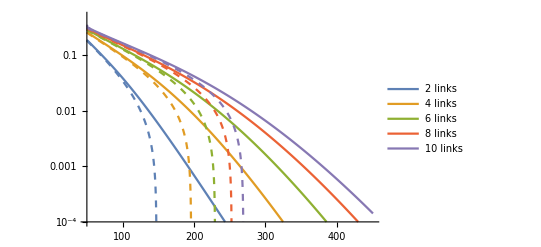
-Graphics-Distance (km)Secret-key rate

```mathematica
rmax=100;
λ=0.99;
Labeled[ListPlot[{SKRBIN2L,SKRBIN4L,SKRBIN6L,SKRBIN8L,SKRBIN10L,
SKRNOBIN2,SKRNOBIN4,SKRNOBIN6,SKRNOBIN8,SKRNOBIN10},Joined->True,ScalingFunctions->"Log",PlotStyle->{{RGBColor[0.368417, 0.506779, 0.709798],Thickness[Large]},{RGBColor[0.880722, 0.611041, 0.142051],Thickness[Large]},{RGBColor[0.560181, 0.691569, 0.194885],Thickness[Large]},{RGBColor[0.922526, 0.385626, 0.209179],Thickness[Large]},{RGBColor[0.528488, 0.470624, 0.701351],Thickness[Large]},
{RGBColor[0.368417, 0.506779, 0.709798],Dashing[{Small,Small}]},{RGBColor[0.880722, 0.611041, 0.142051],Dashing[{Small,Small}]},{RGBColor[0.560181, 0.691569, 0.194885],Dashing[{Small,Small}]},{RGBColor[0.922526, 0.385626, 0.209179],Dashing[{Small,Small}]},{RGBColor[0.528488, 0.470624, 0.701351],Dashing[{Small,Small}]}}, PlotRange->{{50, 450.5}, {10^-4, 0.5}},PlotMarkers->None,PlotLegends->Placed[{{"2 links", "4 links","6 links","8 links", "10 links"}},{0.85, 0.75}]],{"Distance (km)", Rotate["Secret-key rate",Pi/2]}, {Bottom, Left}]
```

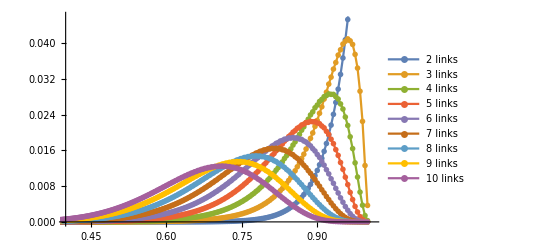
-Graphics-Λ_nProbability

```mathematica
q=0.9;
λ=0.995;
Labeled[ListPlot[Table[distrtolamdistr[distr,λ,200],{distr, {distr2, distr3, distr4, distr5, distr6, distr7, distr8, distr9, distr10}}],Joined->True, PlotRange->{{0.4, 1.01},{0, 0.046}},PlotMarkers->{"●",Scaled[0.015]},PlotLegends->Placed[{{"2 links", "3 links", "4 links", "5 links", "6 links","7 links", "8 links", "9 links", "10 links"}},{0.38, 0.65}]], {"Λ_n", Rotate["Probability",Pi/2]}, {Bottom, Left}]
```